```mathematica
ineqs=Fold[And,Monitor[Flatten[Table[ComposeInEq[key],{key,Keys[newAssoc]}]],key]]//Simplify
```

b09>0&&z>0&&b01>0&&b03>0&&b10>0&&b08>0&&b05>0&&b02>0&&b07>0&&b04>0&&b06>0&&b25>0&&b16>0&&b33>0&&b22>0&&b26>0&&b34>0&&b19>0&&b30>0&&b11>0&&b28>0&&b12>0&&b23>0&&b39>0&&b21>0&&b27>0&&b46>0&&b17>0&&b35>0&&b47>0&&b32>0&&b14>0&&b15>0&&b20>0&&b29>0&&b50>0&&b13>0&&b41>0&&b24>0&&b31>0&&b49>0&&b18>0&&b43>0&&b36>0&&b37>0&&b38>0&&b40>0&&b42>0&&b44>0&&b45>0&&b48>0&&b09<z&&b01<z&&b03<z&&b10<z&&b08<z&&b05<z&&b02<z&&b07<z&&b04<z&&b06<z&&b25<b06&&b16<b06&&b03+b33<b06+b10&&b10+b33<b03+b06&&b22<b06&&b05+b26<b02+b06&&b02+b26<b05+b06&&b07+b34<b04+b06&&b04+b34<b06+b07&&b06+b09<b25+z&&b25<b09&&b01+b06<b16+z&&b16<b01&&b03+b06+b10<b33+2 z&&b06+b33<b03+b10&&b06+b08<b22+z&&b22<b08&&b02+b05+b06<b26+2 z&&b06+b26<b02+b05&&b04+b06+b07<b34+2 z&&b06+b34<b04+b07&&b19<b04&&b01+b30<b04+b10&&b11<b04&&b10+b30<b01+b04&&b08+b28<b02+b04&&b12<b04&&b02+b28<b04+b08&&b07+b19+b25+b39<b04+b06+b23+b34&&2 b03+2 b07+5 b16+2 b30+b46<b01+b04+4 b06+b10+b11+b21+b27+b33+b34&&b01+b06+b07+b10+b11+b21+b27+b33<2 b03+2 b04+5 b16+2 b30+2 b34+b46&&2 b01+2 b07+5 b11+2 b33+b46<b03+4 b04+b06+b10+b16+b21+b27+b30+b34&&b03+b04+b07+b10+b16+b21+b27+b30<2 b01+2 b06+5 b11+2 b33+2 b34+b46&&2 b07+2 b10+2 b30+2 b33+b46<b01+b03+b04+b06+b11+b16+b21+b27+b34&&b01+b03+b07+b11+b16+b21+b27<2 b04+2 b06+2 b10+2 b30+2 b33+2 b34+b46&&2 b05+2 b07+5 b22+2 b28+b47<b02+b04+4 b06+b08+b12+b17+b26+b34+b35&&b02+b06+b07+b08+b12+b17+b26+b35<2 b04+2 b05+5 b22+2 b28+2 b34+b47&&2 b07+2 b08+5 b12+2 b26+b47<b02+4 b04+b05+b06+b17+b22+b28+b34+b35&&b02+b04+b05+b07+b17+b22+b28+b35<2 b06+2 b08+5 b12+2 b26+2 b34+b47&&2 b02+2 b07+2 b26+2 b28+b47<b04+b05+b06+b08+b12+b17+b22+b34+b35&&b05+b07+b08+b12+b17+b22+b35<2 b02+2 b04+2 b06+2 b26+2 b28+2 b34+b47&&b04+b09<b19+z&&b19<b09&&b01+b04+b10<b30+2 z&&b04+b30<b01+b10&&b03+b04<b11+z&&b11<b03&&b02+b04+b08<b28+2 z&&b04+b28<b02+b08&&b04+b05<b12+z&&b12<b05&&b23<b07&&b01+b27<b03+b07&&b03+b27<b01+b07&&b21<b07&&b08+b35<b05+b07&&b05+b35<b07+b08&&b17<b07&&b04+b23+b25+b39<b06+b07+b19+b34&&2 b04+2 b10+5 b16+2 b27+b46<b01+b03+4 b06+b07+b11+b21+b30+b33+b34&&b01+b03+b04+b06+b11+b21+b30+b33<2 b07+2 b10+5 b16+2 b27+2 b34+b46&&2 b03+2 b04+2 b27+2 b33+b46<b01+b06+b07+b10+b11+b16+b21+b30+b34&&b01+b04+b10+b11+b16+b21+b30<2 b03+2 b06+2 b07+2 b27+2 b33+2 b34+b46&&2 b01+2 b04+5 b21+2 b33+b46<b03+b06+4 b07+b10+b11+b16+b27+b30+b34&&b03+b04+b07+b10+b11+b16+b27+b30<2 b01+2 b06+5 b21+2 b33+2 b34+b46&&2 b02+2 b04+5 b22+2 b35+b47<b05+4 b06+b07+b08+b12+b17+b26+b28+b34&&b04+b05+b06+b08+b12+b17+b26+b28<2 b02+2 b07+5 b22+2 b34+2 b35+b47&&2 b04+2 b05+2 b26+2 b35+b47<b02+b06+b07+b08+b12+b17+b22+b28+b34&&b02+b04+b08+b12+b17+b22+b28<2 b05+2 b06+2 b07+2 b26+2 b34+2 b35+b47&&2 b04+2 b08+5 b17+2 b26+b47<b02+b05+b06+4 b07+b12+b22+b28+b34+b35&&b02+b04+b05+b07+b12+b22+b28+b35<2 b06+2 b08+5 b17+2 b26+2 b34+b47&&b06+b19+b23+b39<b04+b07+b25+b34&&2 b01+2 b06+2 b27+2 b30+b46<b03+b04+b07+b10+b11+b16+b21+b33+b34&&b03+b06+b10+b11+b16+b21+b33<2 b01+2 b04+2 b07+2 b27+2 b30+2 b34+b46&&2 b06+2 b10+5 b11+2 b27+b46<b01+b03+4 b04+b07+b16+b21+b30+b33+b34&&b01+b03+b04+b06+b16+b21+b30+b33<2 b07+2 b10+5 b11+2 b27+2 b34+b46&&2 b03+2 b06+5 b21+2 b30+b46<b01+b04+4 b07+b10+b11+b16+b27+b33+b34&&b01+b06+b07+b10+b11+b16+b27+b33<2 b03+2 b04+5 b21+2 b30+2 b34+b46&&2 b06+2 b08+2 b28+2 b35+b47<b02+b04+b05+b07+b12+b17+b22+b26+b34&&b02+b05+b06+b12+b17+b22+b26<2 b04+2 b07+2 b08+2 b28+2 b34+2 b35+b47&&2 b02+2 b06+5 b12+2 b35+b47<4 b04+b05+b07+b08+b17+b22+b26+b28+b34&&b04+b05+b06+b08+b17+b22+b26+b28<2 b02+2 b07+5 b12+2 b34+2 b35+b47&&2 b05+2 b06+5 b17+2 b28+b47<b02+b04+4 b07+b08+b12+b22+b26+b34+b35&&b02+b06+b07+b08+b12+b22+b26+b35<2 b04+2 b05+5 b17+2 b28+2 b34+b47&&b39<b34&&b03+b04+b07+b10+4 b16+b27+b30+2 b46<2 (b01+b06+b11+b21+b33+b34)&&2 (b01+b06+b11+b21+b33)<b03+b04+b07+b10+4 b16+b27+b30+4 b34+2 b46&&b01+b06+b07+b10+4 b11+b27+b33+2 b46<2 (b03+b04+b16+b21+b30+b34)&&2 (b03+b04+b16+b21+b30)<b01+b06+b07+b10+4 b11+b27+b33+4 b34+2 b46&&b01+b03+b04+b06+4 b21+b30+b33+2 b46<2 (b07+b10+b11+b16+b27+b34)&&2 (b07+b10+b11+b16+b27)<b01+b03+b04+b06+4 b21+b30+b33+4 b34+2 b46&&b02+b04+b05+b07+4 b22+b28+b35+2 b47<2 (b06+b08+b12+b17+b26+b34)&&2 (b06+b08+b12+b17+b26)<b02+b04+b05+b07+4 b22+b28+4 b34+b35+2 b47&&b02+b06+b07+b08+4 b12+b26+b35+2 b47<2 (b04+b05+b17+b22+b28+b34)&&2 (b04+b05+b17+b22+b28)<b02+b06+b07+b08+4 b12+b26+4 b34+b35+2 b47&&b04+b05+b06+b08+4 b17+b26+b28+2 b47<2 (b02+b07+b12+b22+b34+b35)&&2 (b02+b07+b12+b22+b35)<b04+b05+b06+b08+4 b17+b26+b28+4 b34+2 b47&&b06+b19+b23+b34<b04+b07+b25+b39&&b25+b39<b19+b23&&4 b01+4 b06+b11+b21+b27+b30+b33+b34<2 b03+2 b04+2 b07+2 b10+5 b16+b46&&2 b03+2 b10+5 b16+2 b34+b46<4 b01+b04+b06+b07+b11+b21+b27+b30+b33&&b03+b06+b10+b11+b16+b21+b27+b30+b34<2 b01+2 b04+2 b07+2 b33+b46&&2 b01+2 b06+2 b33+2 b34+b46<b03+b04+b07+b10+b11+b16+b21+b27+b30&&4 b06+4 b08+b12+b17+b26+b28+b34+b35<2 b02+2 b04+2 b05+2 b07+5 b22+b47&&2 b02+2 b05+5 b22+2 b34+b47<b04+b06+b07+4 b08+b12+b17+b26+b28+b35&&b02+b05+b06+b12+b17+b22+b28+b34+b35<2 b04+2 b07+2 b08+2 b26+b47&&2 b06+2 b08+2 b26+2 b34+b47<b02+b04+b05+b07+b12+b17+b22+b28+b35&&b04+b23+b25+b34<b06+b07+b19+b39&&b19+b39<b23+b25&&b01+b04+b10+b11+b16+b21+b27+b33+b34<2 b03+2 b06+2 b07+2 b30+b46&&2 b03+2 b04+2 b30+2 b34+b46<b01+b06+b07+b10+b11+b16+b21+b27+b33&&4 b03+4 b04+b16+b21+b27+b30+b33+b34<2 b01+2 b06+2 b07+2 b10+5 b11+b46&&2 b01+2 b10+5 b11+2 b34+b46<4 b03+b04+b06+b07+b16+b21+b27+b30+b33&&b02+b04+b08+b12+b17+b22+b26+b34+b35<2 b05+2 b06+2 b07+2 b28+b47&&2 b04+2 b05+2 b28+2 b34+b47<b02+b06+b07+b08+b12+b17+b22+b26+b35&&4 b04+4 b05+b17+b22+b26+b28+b34+b35<2 b02+2 b06+2 b07+2 b08+5 b12+b47&&2 b02+2 b08+5 b12+2 b34+b47<b04+4 b05+b06+b07+b17+b22+b26+b28+b35&&b07+b09<b23+z&&b23<b09&&b01+b03+b07<b27+2 z&&b07+b27<b01+b03&&b07+b10<b21+z&&b21<b10&&b05+b07+b08<b35+2 z&&b07+b35<b05+b08&&b02+b07<b17+z&&b17<b02&&b07+b19+b25+b34<b04+b06+b23+b39&&b23+b39<b19+b25&&b01+b03+b07+b11+b16+b21+b30+b33+b34<2 b04+2 b06+2 b10+2 b27+b46&&2 b07+2 b10+2 b27+2 b34+b46<b01+b03+b04+b06+b11+b16+b21+b30+b33&&4 b07+4 b10+b11+b16+b27+b30+b33+b34<2 b01+2 b03+2 b04+2 b06+5 b21+b46&&2 b01+2 b03+5 b21+2 b34+b46<b04+b06+b07+4 b10+b11+b16+b27+b30+b33&&b05+b07+b08+b12+b17+b22+b26+b28+b34<2 b02+2 b04+2 b06+2 b35+b47&&2 b02+2 b07+2 b34+2 b35+b47<b04+b05+b06+b08+b12+b17+b22+b26+b28&&4 b02+4 b07+b12+b22+b26+b28+b34+b35<2 b04+2 b05+2 b06+2 b08+5 b17+b47&&2 b05+2 b08+5 b17+2 b34+b47<4 b02+b04+b06+b07+b12+b22+b26+b28+b35&&b04+b06+b07+2 b09+b39<b19+b23+b25+b34+2 z&&b19+b23+b25<2 b09+b39&&2 b01+2 b03+2 b04+2 b06+2 b07+2 b10+b46<b11+b16+b21+b27+b30+b33+b34+6 z&&b04+b06+b07+b11+b16+b21+b27+b30+b33<2 b01+2 b03+2 b10+2 b34+b46&&2 b02+2 b04+2 b05+2 b06+2 b07+2 b08+b47<b12+b17+b22+b26+b28+b34+b35+6 z&&b04+b06+b07+b12+b17+b22+b26+b28+b35<2 b02+2 b05+2 b08+2 b34+b47&&b09+b32<b02+b10&&b14<b02&&b15<b02&&b10+b32<b02+b09&&2 b03+2 b05+5 b25+2 b32+b50<b02+4 b06+b09+b10+b15+b20+b26+b29+b33&&b05+b06+b09+b10+b15+b20+b29+b33<2 b02+2 b03+5 b25+2 b26+2 b32+b50&&b05+b14+b16+b41<b02+b06+b13+b26&&2 b05+2 b09+5 b15+2 b33+b50<4 b02+b03+b06+b10+b20+b25+b26+b29+b32&&b02+b03+b05+b10+b20+b25+b29+b32<2 b06+2 b09+5 b15+2 b26+2 b33+b50&&2 b05+2 b10+2 b32+2 b33+b50<b02+b03+b06+b09+b15+b20+b25+b26+b29&&b03+b05+b09+b15+b20+b25+b29<2 b02+2 b06+2 b10+2 b26+2 b32+2 b33+b50&&b04+b05+b06+b08+b12+b17+b34+b35<2 b02+2 b07+5 b22+2 b26+2 b28+b47&&2 b01+2 b08+5 b19+2 b32+b49<b02+4 b04+b09+b10+b14+b24+b28+b30+b31&&b04+b08+b09+b10+b14+b24+b30+b31<2 b01+2 b02+5 b19+2 b28+2 b32+b49&&2 b08+2 b09+5 b14+2 b30+b49<b01+4 b02+b04+b10+b19+b24+b28+b31+b32&&b01+b02+b08+b10+b19+b24+b31+b32<2 b04+2 b09+5 b14+2 b28+2 b30+b49&&b08+b11+b15+b43<b02+b04+b18+b28&&2 b08+2 b10+2 b30+2 b32+b49<b01+b02+b04+b09+b14+b19+b24+b28+b31&&b01+b08+b09+b14+b19+b24+b31<2 b02+2 b04+2 b10+2 b28+2 b30+2 b32+b49&&b04+b05+b06+b08+b17+b22+b34+b35<2 b02+2 b07+5 b12+2 b26+2 b28+b47&&2 b01+2 b03+2 b05+6 b07+2 b08+2 b11+2 b12+2 b13+2 b16+2 b17+2 b18+10 b19+2 b21+2 b22+10 b25+2 b27+6 b32+2 b35+11 b39+3 b49+3 b50<2 b02+10 b04+10 b06+2 b09+2 b10+2 b14+2 b15+2 b20+10 b23+2 b24+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+10 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+2 b20+2 b22+10 b23+2 b24+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b18+10 b19+2 b21+10 b25+6 b26+2 b27+6 b28+6 b32+11 b39+3 b47+3 b49+3 b50&&2 b03+6 b05+2 b07+2 b08+2 b09+2 b12+10 b14+2 b15+10 b16+2 b17+2 b18+2 b20+2 b22+2 b23+2 b25+2 b29+6 b30+2 b35+11 b41+3 b46+3 b49<2 b01+10 b02+2 b04+10 b06+2 b10+2 b11+10 b13+2 b19+2 b21+2 b24+10 b26+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b45+b47+b48+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+10 b13+2 b17+2 b19+2 b21+2 b22+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b48+b50<2 b03+6 b04+2 b05+2 b09+10 b14+2 b15+10 b16+2 b18+2 b20+2 b23+2 b25+6 b28+2 b29+6 b30+6 b34+11 b41+3 b46+3 b47+3 b49&&2 b01+2 b05+2 b07+6 b08+2 b09+10 b11+2 b12+2 b13+2 b14+10 b15+2 b17+2 b19+2 b22+2 b23+2 b24+2 b31+6 b33+2 b35+11 b43+3 b46+3 b50<10 b02+2 b03+10 b04+2 b06+2 b10+2 b16+10 b18+2 b20+2 b21+2 b25+2 b26+2 b27+10 b28+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b44+b45+b47+b48+b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b12+2 b16+2 b17+10 b18+2 b20+2 b21+2 b22+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b48+b49<2 b01+6 b06+2 b08+2 b09+10 b11+2 b13+2 b14+10 b15+2 b19+2 b23+2 b24+6 b26+2 b31+6 b33+6 b34+11 b43+3 b46+3 b47+3 b50&&2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+2 b17+2 b18+2 b22+2 b23+6 b30+6 b32+6 b33+2 b35+3 b46+3 b49+3 b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b14+2 b15+2 b16+2 b19+2 b20+2 b21+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48&&2 b01+2 b03+2 b05+2 b07+2 b08+2 b09+2 b11+2 b12+2 b14+2 b15+2 b16+2 b17+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b48<6 b02+6 b04+6 b06+6 b10+2 b13+2 b18+2 b23+6 b26+6 b28+6 b30+6 b32+6 b33+6 b34+3 b46+3 b47+3 b49+3 b50&&2 (b06+b08+b12+b17+b35)<b02+b04+b05+b07+4 b22+b26+4 b28+b34+2 b47&&2 (b04+b05+b17+b22+b35)<b02+b06+b07+b08+4 b12+4 b26+b28+b34+2 b47&&b23+b37<b17+b21&&b14+b42<b15+b17&&b15+b42<b14+b17&&b21+b37<b17+b23&&b02+b04+b05+b07+b12+b22+b26+b34<2 b06+2 b08+5 b17+2 b28+2 b35+b47&&b02+b06+b07+b08+b12+b22+b28+b34<2 b04+2 b05+5 b17+2 b26+2 b35+b47&&2 b02+2 b03+6 b04+2 b05+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b18+2 b22+2 b23+2 b24+10 b25+2 b27+2 b28+2 b30+2 b31+2 b35+11 b37+11 b39+3 b50<6 b01+10 b06+6 b08+2 b15+10 b17+10 b19+2 b20+10 b21+2 b26+2 b29+2 b32+2 b33+10 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+10 b19+2 b20+10 b21+2 b22+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b38+b40+b41+b42+b43+b44+b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+10 b17+2 b18+2 b23+2 b24+10 b25+6 b26+2 b27+2 b30+2 b31+11 b37+11 b39+3 b47+3 b50&&2 b01+6 b02+2 b03+2 b04+6 b05+2 b07+2 b10+2 b12+2 b14+10 b16+2 b18+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b28+2 b29+2 b31+2 b32+2 b35+11 b41+11 b42+3 b46<10 b06+6 b08+6 b09+2 b11+10 b13+10 b15+10 b17+2 b21+10 b26+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b43+b44+b45+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+10 b13+10 b15+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b14+10 b16+10 b17+2 b18+2 b19+2 b20+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b41+11 b42+3 b46+3 b47&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+10 b15+2 b18+2 b19+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+11 b42+3 b46+3 b50<2 b03+2 b06+6 b08+2 b10+2 b11+10 b14+2 b16+10 b17+2 b20+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b43+b44+b45+b47+b48+b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+10 b14+2 b16+2 b20+2 b21+2 b22+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b48+b49<2 b01+6 b06+2 b08+2 b09+2 b13+10 b15+10 b17+2 b18+2 b19+2 b23+2 b24+6 b26+2 b31+6 b33+6 b34+11 b42+3 b46+3 b47+3 b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+2 b14+2 b18+2 b19+10 b21+2 b22+2 b24+2 b28+2 b31+6 b33+2 b35+11 b37+3 b46+3 b50<2 b03+2 b06+6 b08+2 b10+2 b11+2 b15+2 b16+10 b17+2 b20+10 b23+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b20+2 b22+10 b23+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b48+b49<2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+10 b17+2 b18+2 b19+10 b21+2 b24+6 b26+2 b31+6 b33+6 b34+11 b37+3 b46+3 b47+3 b50&&b12<b17+b22+b47&&2 (b02+b07+b12+b22+b28)<b04+b05+b06+b08+4 b17+4 b26+b34+b35+2 b47&&2 b01+2 b02+6 b06+6 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b18+10 b19+2 b20+2 b22+2 b23+2 b26+2 b27+2 b29+2 b33+2 b35+11 b37+11 b39+3 b49<6 b03+10 b04+6 b05+2 b14+10 b17+10 b21+2 b24+10 b25+2 b28+2 b30+2 b31+2 b32+10 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+10 b21+2 b22+2 b24+10 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b38+b40+b41+b42+b43+b44+b45+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+10 b17+2 b18+10 b19+2 b20+2 b23+2 b27+6 b28+2 b29+2 b33+11 b37+11 b39+3 b47+3 b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+10 b14+2 b18+2 b20+2 b22+2 b23+2 b25+2 b26+2 b29+6 b30+2 b35+11 b42+3 b46+3 b49<2 b01+2 b04+6 b05+2 b10+2 b11+10 b15+2 b16+10 b17+2 b19+2 b21+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b43+b44+b45+b47+b48+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+10 b15+2 b16+2 b19+2 b21+2 b22+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b48+b50<2 b03+6 b04+2 b05+2 b09+2 b13+10 b14+10 b17+2 b18+2 b20+2 b23+2 b25+6 b28+2 b29+6 b30+6 b34+11 b42+3 b46+3 b47+3 b49&&2 b01+6 b02+2 b03+2 b06+2 b07+6 b08+2 b10+10 b11+2 b12+2 b13+2 b15+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b26+2 b29+2 b31+2 b32+2 b35+11 b42+11 b43+3 b46<10 b04+6 b05+6 b09+10 b14+2 b16+10 b17+10 b18+2 b21+2 b27+10 b28+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b44+b45+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b12+10 b14+2 b16+10 b18+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b11+2 b13+2 b15+10 b17+2 b19+2 b20+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b42+11 b43+3 b46+3 b47&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b18+2 b20+10 b21+2 b22+2 b25+2 b26+2 b29+6 b30+2 b35+11 b37+3 b46+3 b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+10 b17+2 b19+10 b23+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b19+2 b22+10 b23+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b48+b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b17+2 b18+2 b20+10 b21+2 b25+6 b28+2 b29+6 b30+6 b34+11 b37+3 b46+3 b47+3 b49&&2 (b02+b07+b12+b22+b26)<b04+b05+b06+b08+4 b17+4 b28+b34+b35+2 b47&&b22<b12+b17+b47&&2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b16+2 b18+2 b22+2 b27+2 b35+5 b37+11 b39+b49+b50<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+4 b17+4 b21+4 b23+2 b32+10 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48&&2 b01+2 b02+2 b03+2 b12+4 b21+2 b22+4 b23+2 b32+2 b34+2 b35+b36+b38+b40+b41+b42+b43+b44+b45+b46+b48<2 b07+2 b09+2 b10+2 b11+2 b13+2 b16+4 b17+2 b18+2 b26+2 b27+2 b28+5 b37+11 b39+3 b47+b49+b50&&4 b02+2 b03+2 b07+2 b12+4 b16+2 b18+2 b20+2 b22+2 b23+2 b25+2 b29+2 b30+2 b35+5 b41+5 b42+3 b46+b49<4 b06+2 b08+2 b09+2 b11+4 b13+4 b15+4 b17+2 b21+4 b26+2 b27+2 b33+2 b34+b36+b37+b38+b39+b40+b43+b44+b45+b47+b48+b50&&2 b06+2 b07+2 b09+2 b11+2 b12+4 b13+4 b15+2 b21+2 b22+2 b26+2 b27+2 b33+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b48+b50<2 b03+2 b04+2 b05+4 b16+4 b17+2 b18+2 b20+2 b23+2 b25+2 b28+2 b29+2 b30+6 b34+5 b41+5 b42+3 b46+3 b47+b49&&2 b01+4 b02+2 b07+4 b11+2 b12+2 b13+2 b19+2 b22+2 b23+2 b24+2 b31+2 b33+2 b35+5 b42+5 b43+3 b46+b50<4 b04+2 b05+2 b09+4 b14+2 b16+4 b17+4 b18+2 b21+2 b27+4 b28+2 b30+2 b34+b36+b37+b38+b39+b40+b41+b44+b45+b47+b48+b49&&2 b04+2 b07+2 b09+2 b12+4 b14+2 b16+4 b18+2 b21+2 b22+2 b27+2 b28+2 b30+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b48+b49<2 b01+2 b06+2 b08+4 b11+2 b13+4 b17+2 b19+2 b23+2 b24+2 b26+2 b31+2 b33+6 b34+5 b42+5 b43+3 b46+3 b47+b50&&2 b02+2 b07+2 b09+2 b12+2 b13+2 b18+4 b21+2 b22+2 b30+2 b33+2 b35+5 b37+3 b46+b49+b50<2 b05+2 b08+2 b10+2 b11+2 b16+4 b17+4 b23+2 b27+2 b32+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48&&2 b02+2 b07+2 b10+2 b11+2 b12+2 b16+2 b22+4 b23+2 b27+2 b32+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b48<2 b04+2 b06+2 b09+2 b13+4 b17+2 b18+4 b21+2 b26+2 b28+2 b30+2 b33+6 b34+5 b37+3 b46+3 b47+b49+b50&&b09+b17+b21+b32<b02+b10+b23+b37&&b10+b17+b23+b37<b02+b09+b21+b32&&b14+b15+b17<2 b02+b42&&b17+b42<b14+b15&&b10+b17+b23+b32<b02+b09+b21+b37&&b09+b17+b21+b37<b02+b10+b23+b32&&2 b04+2 b06+5 b17+2 b35+b47<4 b02+b05+b07+b08+b12+b22+b26+b28+b34&&6 b01+6 b03+6 b05+6 b08+10 b17+10 b19+10 b21+10 b25+10 b32+10 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50<6 b02+6 b04+6 b06+6 b07+6 b09+6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b18+2 b20+2 b22+2 b23+2 b24+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b33+2 b35+11 b37+11 b39&&2 b04+2 b05+2 b06+2 b07+2 b08+6 b09+6 b10+2 b11+2 b13+2 b14+2 b15+2 b16+10 b17+2 b18+2 b20+2 b23+2 b24+2 b27+2 b29+2 b30+2 b31+2 b33+11 b37+11 b39+3 b47<6 b01+10 b02+6 b03+2 b12+10 b19+10 b21+2 b22+10 b25+2 b26+2 b28+10 b32+2 b34+2 b35+b36+b38+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50&&6 b05+6 b08+6 b09+2 b11+10 b14+10 b15+2 b16+10 b17+2 b21+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b43+b44+b45+b47+b48+b49+b50<2 b01+18 b02+2 b03+2 b04+2 b06+2 b07+2 b10+2 b12+2 b13+2 b18+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+2 b35+11 b42+3 b46&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+10 b17+2 b18+2 b19+2 b20+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b42+3 b46+3 b47<2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+10 b14+10 b15+2 b16+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b48+b49+b50&&6 b05+6 b08+10 b10+2 b11+2 b16+10 b17+10 b23+2 b27+2 b30+10 b32+2 b33+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49+b50<2 b01+6 b02+2 b03+2 b04+2 b06+2 b07+6 b09+2 b12+2 b13+2 b14+2 b15+2 b18+2 b19+2 b20+10 b21+2 b22+2 b24+2 b25+2 b26+2 b28+2 b29+2 b31+2 b35+11 b37+3 b46&&2 b01+2 b03+2 b05+2 b08+6 b09+2 b13+2 b14+2 b15+10 b17+2 b18+2 b19+2 b20+10 b21+2 b24+2 b25+2 b29+2 b31+6 b34+11 b37+3 b46+3 b47<10 b02+2 b04+2 b06+2 b07+10 b10+2 b11+2 b12+2 b16+2 b22+10 b23+2 b26+2 b27+2 b28+2 b30+10 b32+2 b33+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b48+b49+b50&&b04+b05+b06+b08+4 b17+b34+b35+2 b47<2 (b02+b07+b12+b22+b26+b28)&&b02+b09+b10<b32+2 z&&b02+b32<b09+b10&&b01+b02<b14+z&&b14<b01&&b02+b03<b15+z&&b15<b03&&b17+b21+b23<2 b07+b37&&b17+b37<b21+b23&&b01+b15+b17+b27<b03+b07+b14+b42&&b03+b14+b17+b42<b01+b07+b15+b27&&b03+b14+b17+b27<b01+b07+b15+b42&&b01+b15+b17+b42<b03+b07+b14+b27&&b02+2 b07+b09+b10+b37<b17+b21+b23+b32+2 z&&b02+b21+b23+b32<b09+b10+b17+b37&&b01+2 b02+b03+b07+b42<b14+b15+b17+b27+2 z&&b07+b14+b15+b27<b01+b03+b17+b42&&b09+b29<b03+b05&&b13<b05&&b03+b29<b05+b09&&b20<b05&&2 b02+2 b10+5 b25+2 b29+b50<b03+b05+4 b06+b09+b15+b20+b26+b32+b33&&b02+b03+b06+b09+b15+b20+b32+b33<2 b05+2 b10+5 b25+2 b26+2 b29+b50&&b02+b13+b16+b41<b05+b06+b14+b26&&2 b02+2 b03+2 b29+2 b33+b50<b05+b06+b09+b10+b15+b20+b25+b26+b32&&b02+b09+b10+b15+b20+b25+b32<2 b03+2 b05+2 b06+2 b26+2 b29+2 b33+b50&&2 b02+2 b09+5 b20+2 b33+b50<b03+4 b05+b06+b10+b15+b25+b26+b29+b32&&b02+b03+b05+b10+b15+b25+b29+b32<2 b06+2 b09+5 b20+2 b26+2 b33+b50&&b02+b06+b07+b08+b12+b17+b28+b34<2 b04+2 b05+5 b22+2 b26+2 b35+b47&&b19+b44<b11+b12&&b13+b45<b12+b20&&b11+b44<b12+b19&&b20+b45<b12+b13&&b02+b04+b05+b07+b17+b22+b26+b34<2 b06+2 b08+5 b12+2 b28+2 b35+b47&&2 b02+2 b03+6 b04+2 b05+6 b07+2 b09+2 b10+2 b13+2 b14+2 b16+2 b17+2 b18+2 b19+2 b21+2 b22+2 b24+10 b25+2 b27+2 b28+2 b30+2 b31+2 b35+11 b39+11 b44+3 b50<6 b01+10 b06+6 b08+10 b11+10 b12+2 b15+2 b20+10 b23+2 b26+2 b29+2 b32+2 b33+10 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+10 b11+2 b15+2 b17+2 b20+2 b22+10 b23+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+10 b12+2 b13+2 b14+2 b16+2 b18+2 b19+2 b21+2 b24+10 b25+6 b26+2 b27+2 b30+2 b31+11 b39+11 b44+3 b47+3 b50&&2 b01+6 b02+2 b03+2 b04+6 b05+2 b07+2 b10+2 b13+2 b15+10 b16+2 b17+2 b18+2 b19+2 b22+2 b23+2 b24+2 b25+2 b28+2 b29+2 b31+2 b32+2 b35+11 b41+11 b45+3 b46<10 b06+6 b08+6 b09+2 b11+10 b12+10 b14+10 b20+2 b21+10 b26+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b11+10 b14+2 b17+10 b20+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b12+2 b13+2 b15+10 b16+2 b18+2 b19+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b41+11 b45+3 b46+3 b47&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+10 b11+2 b13+2 b14+2 b17+2 b18+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+11 b44+3 b46+3 b50<2 b03+2 b06+6 b08+2 b10+10 b12+2 b15+2 b16+10 b19+2 b20+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b47+b48+b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b15+2 b16+2 b17+10 b19+2 b20+2 b21+2 b22+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b48+b49<2 b01+6 b06+2 b08+2 b09+10 b11+10 b12+2 b13+2 b14+2 b18+2 b23+2 b24+6 b26+2 b31+6 b33+6 b34+11 b44+3 b46+3 b47+3 b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b14+2 b17+2 b18+2 b19+10 b20+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+11 b45+3 b46+3 b50<2 b03+2 b06+6 b08+2 b10+2 b11+10 b12+10 b13+2 b15+2 b16+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b47+b48+b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+10 b13+2 b15+2 b16+2 b17+2 b21+2 b22+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b48+b49<2 b01+6 b06+2 b08+2 b09+10 b12+2 b14+2 b18+2 b19+10 b20+2 b23+2 b24+6 b26+2 b31+6 b33+6 b34+11 b45+3 b46+3 b47+3 b50&&b17<b12+b22+b47&&b09+b11+b12+b29<b03+b05+b19+b44&&b03+b12+b19+b44<b05+b09+b11+b29&&b12+b13+b20<2 b05+b45&&b12+b45<b13+b20&&b03+b12+b19+b29<b05+b09+b11+b44&&b09+b11+b12+b44<b03+b05+b19+b29&&2 b06+2 b07+5 b12+2 b28+b47<b02+b04+4 b05+b08+b17+b22+b26+b34+b35&&2 b01+2 b08+5 b23+2 b29+b48<b03+b05+4 b07+b09+b13+b18+b27+b31+b35&&b03+b07+b08+b09+b13+b18+b27+b31<2 b01+2 b05+5 b23+2 b29+2 b35+b48&&2 b08+2 b09+5 b13+2 b27+b48<b01+b03+4 b05+b07+b18+b23+b29+b31+b35&&b01+b03+b05+b08+b18+b23+b29+b31<2 b07+2 b09+5 b13+2 b27+2 b35+b48&&2 b03+2 b08+2 b27+2 b29+b48<b01+b05+b07+b09+b13+b18+b23+b31+b35&&b01+b08+b09+b13+b18+b23+b31<2 b03+2 b05+2 b07+2 b27+2 b29+2 b35+b48&&b08+b20+b21+b40<b05+b07+b24+b35&&2 b01+2 b02+6 b04+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+2 b21+2 b22+10 b23+2 b24+10 b25+2 b28+6 b29+2 b30+11 b39+3 b48+3 b50<2 b03+2 b05+10 b06+10 b07+2 b09+2 b13+2 b15+2 b18+10 b19+2 b20+2 b26+2 b27+2 b31+2 b32+2 b33+10 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b17+2 b18+10 b19+2 b20+2 b22+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+2 b21+10 b23+2 b24+10 b25+6 b26+6 b29+2 b30+6 b35+11 b39+3 b47+3 b48+3 b50&&6 b02+2 b04+2 b08+2 b09+2 b10+2 b12+10 b13+2 b15+10 b16+2 b17+2 b19+2 b20+2 b22+2 b24+2 b25+6 b27+2 b28+2 b32+11 b41+3 b46+3 b48<2 b01+2 b03+10 b05+10 b06+2 b07+2 b11+10 b14+2 b18+2 b21+2 b23+10 b26+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b47+b49+b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+10 b14+2 b17+2 b18+2 b21+2 b22+2 b23+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b42+b43+b44+b45+b49+b50<2 b02+6 b07+2 b09+2 b10+10 b13+2 b15+10 b16+2 b19+2 b20+2 b24+2 b25+6 b27+2 b32+6 b34+6 b35+11 b41+3 b46+3 b47+3 b48&&2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b17+2 b19+2 b22+2 b24+6 b27+2 b28+6 b29+6 b33+3 b46+3 b48+3 b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+2 b18+2 b20+2 b21+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b49&&2 b01+2 b02+2 b04+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b17+2 b18+2 b20+2 b21+2 b22+2 b23+2 b25+2 b28+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b49<6 b03+6 b05+6 b06+6 b07+2 b14+2 b19+2 b24+6 b26+6 b27+6 b29+6 b33+6 b34+6 b35+3 b46+3 b47+3 b48+3 b50&&2 b01+2 b02+2 b04+6 b08+2 b09+2 b12+2 b13+2 b14+2 b17+2 b18+2 b19+10 b20+10 b21+2 b22+2 b23+2 b28+2 b31+6 b33+11 b40+3 b46+3 b50<2 b03+10 b05+2 b06+10 b07+2 b10+2 b11+2 b15+2 b16+10 b24+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b47+b48+b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b17+2 b22+10 b24+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b48+b49<2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+2 b18+2 b19+10 b20+10 b21+2 b23+6 b26+2 b31+6 b33+6 b34+11 b40+3 b46+3 b47+3 b50&&2 (b06+b08+b12+b17+b28)<b02+b04+b05+b07+4 b22+b26+b34+4 b35+2 b47&&2 b01+2 b03+6 b04+2 b05+6 b06+2 b08+2 b09+2 b14+2 b15+2 b16+2 b17+2 b19+2 b20+2 b21+2 b22+10 b23+2 b24+2 b26+2 b28+2 b30+2 b32+2 b33+11 b39+11 b44+3 b48<6 b02+10 b07+6 b10+10 b11+10 b12+2 b13+2 b18+10 b25+2 b27+2 b29+2 b31+10 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+10 b11+2 b13+2 b17+2 b18+2 b22+10 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+10 b12+2 b14+2 b15+2 b16+2 b19+2 b20+2 b21+10 b23+2 b24+2 b30+2 b32+2 b33+6 b35+11 b39+11 b44+3 b47+3 b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b13+2 b14+2 b15+2 b17+2 b19+2 b22+2 b24+2 b25+2 b26+6 b27+2 b28+2 b32+11 b45+3 b46+3 b48<2 b01+6 b02+2 b03+2 b07+2 b11+10 b12+2 b16+2 b18+10 b20+2 b21+2 b23+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b47+b49+b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b16+2 b17+2 b18+10 b20+2 b21+2 b22+2 b23+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b49+b50<2 b02+6 b07+2 b09+2 b10+10 b12+10 b13+2 b14+2 b15+2 b19+2 b24+2 b25+6 b27+2 b32+6 b34+6 b35+11 b45+3 b46+3 b47+3 b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b11+2 b14+2 b15+2 b17+2 b20+2 b22+2 b24+2 b25+2 b26+6 b27+2 b28+2 b32+11 b44+3 b46+3 b48<2 b01+6 b02+2 b03+2 b07+10 b12+2 b13+2 b16+2 b18+10 b19+2 b21+2 b23+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b47+b49+b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b13+2 b16+2 b17+2 b18+10 b19+2 b21+2 b22+2 b23+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b45+b49+b50<2 b02+6 b07+2 b09+2 b10+10 b11+10 b12+2 b14+2 b15+2 b20+2 b24+2 b25+6 b27+2 b32+6 b34+6 b35+11 b44+3 b46+3 b47+3 b48&&2 b01+2 b03+2 b04+6 b05+2 b06+6 b08+2 b10+2 b14+2 b15+2 b17+2 b18+2 b19+2 b20+10 b21+2 b22+2 b23+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+11 b40+11 b45+3 b46<6 b02+10 b07+6 b09+2 b11+10 b12+10 b13+2 b16+10 b24+2 b27+2 b30+2 b33+2 b34+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b11+10 b13+2 b16+2 b17+2 b22+10 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b12+2 b14+2 b15+2 b18+2 b19+2 b20+10 b21+2 b23+2 b25+2 b29+2 b31+2 b32+6 b34+11 b40+11 b45+3 b46+3 b47&&2 (b04+b05+b17+b22+b26)<b02+b06+b07+b08+4 b12+b28+b34+4 b35+2 b47&&2 b03+6 b04+2 b05+2 b09+2 b14+2 b16+2 b17+2 b21+2 b22+2 b24+2 b28+2 b30+11 b39+5 b44+b48+b50<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+4 b11+4 b12+4 b19+2 b29+10 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b49&&2 b01+2 b05+2 b10+4 b11+2 b17+4 b19+2 b22+2 b28+2 b29+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b49<2 b03+2 b04+2 b09+4 b12+2 b14+2 b16+2 b21+2 b24+2 b26+2 b30+2 b35+11 b39+5 b44+3 b47+b48+b50&&2 b04+4 b05+2 b10+2 b15+4 b16+2 b17+2 b19+2 b22+2 b24+2 b25+2 b27+2 b28+2 b32+5 b41+5 b45+3 b46+b48<4 b06+2 b08+2 b09+2 b11+4 b12+4 b14+4 b20+2 b21+4 b26+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b47+b49+b50&&2 b04+2 b06+2 b09+2 b11+4 b14+2 b17+4 b20+2 b21+2 b22+2 b26+2 b28+2 b30+2 b33+b36+b37+b38+b39+b40+b42+b43+b44+b49+b50<2 b02+2 b07+2 b10+4 b12+2 b15+4 b16+2 b19+2 b24+2 b25+2 b27+2 b32+6 b34+2 b35+5 b41+5 b45+3 b46+3 b47+b48&&2 b04+2 b05+2 b09+4 b11+2 b14+2 b17+2 b22+2 b24+2 b27+2 b28+2 b33+5 b44+3 b46+b48+b50<2 b02+2 b03+2 b08+4 b12+2 b16+4 b19+2 b21+2 b29+2 b30+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b47+b49&&2 b03+2 b04+2 b05+2 b16+2 b17+4 b19+2 b21+2 b22+2 b28+2 b29+2 b30+b36+b37+b38+b39+b40+b41+b42+b43+b45+b49<2 b06+2 b07+2 b09+4 b11+4 b12+2 b14+2 b24+2 b26+2 b27+2 b33+6 b34+2 b35+5 b44+3 b46+3 b47+b48+b50&&2 b01+2 b04+4 b05+2 b14+2 b17+2 b18+2 b19+4 b21+2 b22+2 b23+2 b28+2 b31+2 b33+5 b40+5 b45+3 b46+b50<2 b02+4 b07+2 b09+2 b11+4 b12+4 b13+2 b16+4 b24+2 b27+2 b30+2 b34+4 b35+b36+b37+b38+b39+b41+b42+b43+b44+b47+b48+b49&&2 b04+2 b07+2 b09+2 b11+4 b13+2 b16+2 b17+2 b22+4 b24+2 b27+2 b28+2 b30+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b48+b49<2 b01+2 b06+2 b08+4 b12+2 b14+2 b18+2 b19+4 b21+2 b23+2 b26+2 b31+2 b33+6 b34+5 b40+5 b45+3 b46+3 b47+b50&&6 b01+6 b02+6 b08+6 b10+10 b11+10 b12+10 b23+10 b25+10 b29+10 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b48+b49+b50<6 b03+6 b04+6 b05+6 b06+6 b07+6 b09+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b24+2 b26+2 b27+2 b28+2 b30+2 b31+2 b32+2 b33+2 b35+11 b39+11 b44&&2 b02+6 b03+2 b04+2 b06+2 b07+2 b08+6 b09+10 b12+2 b13+2 b14+2 b15+2 b16+2 b18+2 b19+2 b20+2 b21+2 b24+2 b27+2 b30+2 b31+2 b32+2 b33+11 b39+11 b44+3 b47<6 b01+10 b05+6 b10+10 b11+2 b17+2 b22+10 b23+10 b25+2 b26+2 b28+10 b29+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b46+b48+b49+b50&&6 b02+6 b08+6 b09+2 b11+10 b12+10 b13+2 b16+10 b20+2 b21+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b47+b48+b49+b50<2 b01+2 b03+2 b04+18 b05+2 b06+2 b07+2 b10+2 b14+2 b15+2 b17+2 b18+2 b19+2 b22+2 b23+2 b24+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+2 b35+11 b45+3 b46&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b12+2 b14+2 b15+2 b18+2 b19+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b45+3 b46+3 b47<2 b04+2 b06+2 b07+6 b09+2 b11+10 b13+2 b16+2 b17+10 b20+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b48+b49+b50&&6 b02+10 b03+6 b08+10 b12+2 b16+10 b19+2 b21+2 b27+10 b29+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b47+b48+b49+b50<2 b01+2 b04+6 b05+2 b06+2 b07+6 b09+2 b10+10 b11+2 b13+2 b14+2 b15+2 b17+2 b18+2 b20+2 b22+2 b23+2 b24+2 b25+2 b26+2 b28+2 b31+2 b32+2 b35+11 b44+3 b46&&2 b01+2 b02+2 b08+6 b09+2 b10+10 b11+10 b12+2 b13+2 b14+2 b15+2 b18+2 b20+2 b23+2 b24+2 b25+2 b31+2 b32+6 b34+11 b44+3 b46+3 b47<10 b03+2 b04+10 b05+2 b06+2 b07+2 b16+2 b17+10 b19+2 b21+2 b22+2 b26+2 b27+2 b28+10 b29+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b48+b49+b50&&b02+b06+b07+b08+4 b12+b28+b34+2 b47<2 (b04+b05+b17+b22+b26+b35)&&2 b06+2 b09+2 b29+2 b32+b50<b02+b03+b05+b10+b15+b20+b25+b26+b33&&b03+b06+b10+b15+b20+b25+b33<2 b02+2 b05+2 b09+2 b26+2 b29+2 b32+b50&&b06+b13+b14+b41<b02+b05+b16+b26&&2 b06+2 b10+5 b15+2 b29+b50<4 b02+b03+b05+b09+b20+b25+b26+b32+b33&&b02+b03+b06+b09+b20+b25+b32+b33<2 b05+2 b10+5 b15+2 b26+2 b29+b50&&2 b03+2 b06+5 b20+2 b32+b50<b02+4 b05+b09+b10+b15+b25+b26+b29+b33&&b05+b06+b09+b10+b15+b25+b29+b33<2 b02+2 b03+5 b20+2 b26+2 b32+b50&&b04+b06+b07+b12+b17+b22+b34<2 b02+2 b05+2 b08+2 b26+2 b28+2 b35+b47&&b02+b03+b05+b10+4 b25+b29+b32+2 b50<2 (b06+b09+b15+b20+b26+b33)&&2 (b06+b09+b15+b20+b33)<b02+b03+b05+b10+4 b25+4 b26+b29+b32+2 b50&&b41<b26&&b05+b06+b09+b10+4 b15+b29+b33+2 b50<2 (b02+b03+b20+b25+b26+b32)&&2 (b02+b03+b20+b25+b32)<b05+b06+b09+b10+4 b15+4 b26+b29+b33+2 b50&&b02+b03+b06+b09+4 b20+b32+b33+2 b50<2 (b05+b10+b15+b25+b26+b29)&&2 (b05+b10+b15+b25+b29)<b02+b03+b06+b09+4 b20+4 b26+b32+b33+2 b50&&2 (b06+b08+b12+b17+b34)<b02+b04+b05+b07+4 b22+4 b26+b28+b35+2 b47&&4 b06+4 b09+b15+b20+b26+b29+b32+b33<2 b02+2 b03+2 b05+2 b10+5 b25+b50&&2 b03+2 b10+5 b25+2 b26+b50<b02+b05+b06+4 b09+b15+b20+b29+b32+b33&&b06+b13+b14+b26<b02+b05+b16+b41&&b16+b41<b13+b14&&b03+b06+b10+b15+b20+b25+b26+b29+b32<2 b02+2 b05+2 b09+2 b33+b50&&2 b06+2 b09+2 b26+2 b33+b50<b02+b03+b05+b10+b15+b20+b25+b29+b32&&2 b04+2 b07+5 b22+2 b26+b47<b02+b05+b06+4 b08+b12+b17+b28+b34+b35&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b13+2 b16+2 b17+2 b18+10 b19+2 b21+2 b22+2 b23+2 b27+6 b32+2 b34+2 b35+11 b44+3 b49+3 b50<2 b02+6 b07+2 b09+2 b10+10 b11+10 b12+2 b14+2 b15+2 b20+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b11+2 b14+2 b15+2 b17+2 b20+2 b22+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b48<2 b01+6 b02+2 b03+2 b07+10 b12+2 b13+2 b16+2 b18+10 b19+2 b21+2 b23+6 b26+2 b27+6 b28+6 b32+11 b44+3 b47+3 b49+3 b50&&2 b01+2 b04+6 b05+6 b06+2 b08+2 b09+2 b10+2 b11+2 b13+10 b14+2 b15+2 b17+2 b18+2 b21+2 b22+2 b23+2 b25+2 b27+2 b29+2 b33+2 b34+2 b35+11 b41+11 b45+3 b49<10 b02+6 b03+6 b07+10 b12+10 b16+2 b19+10 b20+2 b24+10 b26+2 b28+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b42+b43+b44+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+10 b16+2 b17+2 b19+10 b20+2 b22+2 b24+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b46+b48+b50≤2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+10 b12+2 b13+10 b14+2 b15+2 b18+2 b21+2 b23+2 b25+2 b27+6 b28+2 b29+2 b33+11 b41+11 b45+3 b47+3 b49&&2 b03+6 b04+2 b05+2 b06+6 b08+2 b09+2 b10+2 b11+2 b13+2 b14+10 b15+2 b16+2 b17+2 b21+2 b22+2 b23+2 b24+2 b27+2 b30+2 b31+2 b34+2 b35+11 b43+11 b44+3 b50<6 b01+10 b02+6 b07+10 b12+10 b18+10 b19+2 b20+2 b25+2 b26+10 b28+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b17+10 b18+10 b19+2 b20+2 b22+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b46+b48+b49≤2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+10 b12+2 b13+2 b14+10 b15+2 b16+2 b21+2 b23+2 b24+6 b26+2 b27+2 b30+2 b31+11 b43+11 b44+3 b47+3 b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b16+2 b17+2 b18+10 b20+2 b21+2 b22+2 b23+2 b27+6 b32+2 b34+2 b35+11 b45+3 b49+3 b50<2 b02+6 b07+2 b09+2 b10+10 b12+10 b13+2 b14+2 b15+2 b19+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b47+b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b13+2 b14+2 b15+2 b17+2 b19+2 b22+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b48<2 b01+6 b02+2 b03+2 b07+2 b11+10 b12+2 b16+2 b18+10 b20+2 b21+2 b23+6 b26+2 b27+6 b28+6 b32+11 b45+3 b47+3 b49+3 b50&&2 (b04+b05+b17+b22+b34)<b02+b06+b07+b08+4 b12+b26+4 b28+b35+2 b47&&2 b03+4 b04+2 b05+2 b13+2 b16+2 b17+2 b18+2 b21+2 b22+4 b25+2 b27+2 b32+2 b35+5 b39+5 b44+b49+3 b50<2 b01+4 b06+2 b08+4 b11+4 b12+2 b15+2 b20+4 b23+2 b26+2 b29+2 b33+4 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b48&&2 b01+2 b05+2 b06+4 b11+2 b15+2 b17+2 b20+2 b22+4 b23+2 b29+2 b33+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b46+b48<2 b02+2 b03+2 b07+4 b12+2 b13+2 b16+2 b18+2 b21+4 b25+6 b26+2 b27+2 b28+2 b32+5 b39+5 b44+3 b47+b49+3 b50&&2 b01+2 b04+6 b05+2 b10+2 b15+2 b17+2 b18+2 b22+2 b23+2 b25+2 b29+2 b35+11 b41+5 b45+b46+b49<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+4 b12+4 b13+4 b20+10 b26+2 b30+b36+b37+b38+b39+b40+b42+b43+b44+b47+b48+b50&&2 b03+2 b04+2 b09+4 b13+2 b17+4 b20+2 b22+2 b26+2 b30+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b48+b50<2 b01+2 b05+2 b10+4 b12+2 b15+2 b18+2 b23+2 b25+2 b28+2 b29+2 b34+11 b41+5 b45+b46+3 b47+b49&&4 b04+2 b05+2 b09+2 b13+2 b14+4 b15+2 b17+2 b22+2 b23+2 b24+2 b31+2 b33+2 b35+5 b43+5 b44+b46+3 b50<2 b01+4 b02+2 b07+4 b12+4 b18+4 b19+2 b20+2 b25+2 b26+4 b28+2 b29+2 b32+b36+b37+b38+b39+b40+b41+b42+b45+b47+b48+b49&&2 b01+2 b02+2 b05+2 b17+4 b18+4 b19+2 b20+2 b22+2 b25+2 b28+2 b29+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b48+b49≤2 b06+2 b08+2 b09+4 b12+2 b13+2 b14+4 b15+2 b23+2 b24+6 b26+2 b31+2 b33+2 b34+5 b43+5 b44+b46+3 b47+3 b50&&2 b01+2 b04+2 b05+2 b17+2 b18+4 b20+2 b22+2 b23+2 b32+2 b33+2 b35+5 b45+b46+b49+3 b50<2 b07+2 b08+2 b10+4 b12+4 b13+2 b15+2 b25+2 b26+2 b29+2 b30+b36+b37+b38+b39+b40+b41+b42+b43+b44+b47+b48&&2 b04+2 b05+2 b10+4 b13+2 b15+2 b17+2 b22+2 b25+2 b29+2 b30+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b48<2 b01+2 b02+2 b06+4 b12+2 b18+4 b20+2 b23+6 b26+2 b28+2 b32+2 b33+2 b34+5 b45+b46+3 b47+b49+3 b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b19+2 b22+10 b23+2 b24+2 b28+6 b29+2 b30+2 b34+11 b37+3 b48+3 b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b17+2 b18+2 b20+10 b21+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b18+2 b20+10 b21+2 b22+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+10 b17+2 b19+10 b23+2 b24+6 b26+6 b29+2 b30+6 b35+11 b37+3 b47+3 b48+3 b50&&2 b01+6 b02+2 b03+6 b06+2 b07+2 b08+2 b09+2 b11+2 b12+10 b13+2 b14+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b28+2 b30+2 b32+2 b33+2 b34+11 b41+11 b42+3 b48<6 b04+10 b05+6 b10+10 b15+10 b16+10 b17+2 b18+2 b23+10 b26+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+2 b12+10 b15+10 b16+2 b18+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b43+b44+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+10 b13+2 b14+10 b17+2 b19+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b41+11 b42+3 b47+3 b48&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+10 b15+2 b16+2 b19+2 b21+2 b22+2 b24+2 b28+6 b29+2 b30+2 b34+11 b42+3 b48+3 b50<2 b03+6 b04+2 b05+2 b09+2 b13+10 b14+10 b17+2 b18+2 b20+2 b23+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b47+b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+10 b14+2 b18+2 b20+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b49<2 b01+2 b04+6 b05+2 b10+2 b11+10 b15+2 b16+10 b17+2 b19+2 b21+2 b24+6 b26+6 b29+2 b30+6 b35+11 b42+3 b47+3 b48+3 b50&&2 b02+2 b03+2 b06+6 b07+6 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b18+2 b19+10 b20+2 b21+2 b22+2 b27+2 b28+2 b30+2 b31+2 b34+11 b37+11 b40+3 b50<6 b01+6 b04+10 b05+2 b15+10 b17+10 b23+10 b24+2 b25+2 b26+2 b29+2 b32+2 b33+10 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b22+10 b23+10 b24+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+10 b17+2 b18+2 b19+10 b20+2 b21+6 b26+2 b27+2 b30+2 b31+11 b37+11 b40+3 b47+3 b50&&2 (b02+b07+b12+b22+b34)<b04+b05+b06+b08+4 b17+b26+b28+4 b35+2 b47&&2 b02+4 b07+2 b10+2 b11+2 b12+2 b14+2 b16+2 b22+2 b24+4 b25+2 b28+2 b29+2 b30+5 b37+5 b39+b48+3 b50<2 b01+4 b06+2 b08+2 b15+4 b17+4 b19+2 b20+4 b21+2 b26+2 b32+2 b33+4 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b49&&2 b01+2 b02+2 b06+2 b12+2 b15+4 b19+2 b20+4 b21+2 b22+2 b28+2 b32+2 b33+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b49<2 b04+2 b05+2 b10+2 b11+2 b14+2 b16+4 b17+2 b24+4 b25+6 b26+2 b29+2 b30+2 b35+5 b37+5 b39+3 b47+b48+3 b50&&2 b01+6 b02+2 b03+2 b07+2 b12+2 b19+2 b20+2 b22+2 b24+2 b25+2 b28+2 b32+11 b41+5 b42+b46+b48<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+4 b14+4 b15+4 b17+10 b26+2 b27+b36+b37+b38+b39+b40+b43+b44+b45+b47+b49+b50&&2 b07+2 b09+2 b10+2 b12+4 b14+4 b15+2 b22+2 b26+2 b27+2 b28+b36+b37+b38+b39+b40+b43+b44+b45+b49+b50<2 b01+2 b02+2 b03+4 b17+2 b19+2 b20+2 b24+2 b25+2 b32+2 b34+2 b35+11 b41+5 b42+b46+3 b47+b48&&2 b01+2 b02+2 b07+2 b12+4 b15+2 b19+2 b22+2 b24+2 b28+2 b29+2 b33+5 b42+b46+b48+3 b50<2 b03+2 b04+2 b08+4 b14+4 b17+2 b20+2 b25+2 b26+2 b27+2 b32+b36+b37+b38+b39+b40+b41+b43+b44+b45+b47+b49&&2 b02+2 b03+2 b07+2 b12+4 b14+2 b20+2 b22+2 b25+2 b27+2 b28+2 b32+b36+b37+b38+b39+b40+b41+b43+b44+b45+b49<2 b01+2 b05+2 b06+4 b15+4 b17+2 b19+2 b24+6 b26+2 b29+2 b33+2 b34+2 b35+5 b42+b46+3 b47+b48+3 b50&&2 b02+4 b07+2 b09+2 b12+2 b13+2 b14+2 b18+2 b19+4 b20+2 b22+2 b28+2 b31+2 b33+5 b37+5 b40+b46+3 b50<2 b01+2 b04+4 b05+2 b15+4 b17+4 b23+4 b24+2 b25+2 b26+2 b29+2 b32+4 b35+b36+b38+b39+b41+b42+b43+b44+b45+b47+b48+b49&&2 b01+2 b02+2 b05+2 b12+2 b15+2 b22+4 b23+4 b24+2 b25+2 b28+2 b29+2 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b48+b49<2 b06+2 b08+2 b09+2 b13+2 b14+4 b17+2 b18+2 b19+4 b20+6 b26+2 b31+2 b33+2 b34+5 b37+5 b40+b46+3 b47+3 b50&&2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+6 b16+2 b18+2 b19+2 b20+6 b22+2 b23+2 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+9 b37+9 b39+9 b44+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+6 b11+6 b12+6 b17+6 b21+10 b25+2 b29+2 b31+2 b32+6 b34+3 b36+3 b38+3 b40+3 b41+3 b42+3 b43+3 b45+3 b46+3 b47&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+6 b11+6 b21+6 b22+10 b25+2 b29+2 b31+2 b32+6 b34+3 b36+3 b38+3 b40+3 b41+3 b42+3 b43+3 b45+3 b46<2 b04+2 b06+2 b07+6 b09+6 b12+2 b13+2 b14+2 b15+6 b16+6 b17+2 b18+2 b19+2 b20+2 b23+2 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+9 b37+9 b39+9 b44+9 b47+b48+b49+b50&&6 b01+2 b02+2 b05+2 b06+2 b11+2 b13+2 b14+2 b18+2 b19+2 b21+6 b22+2 b23+2 b24+6 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+9 b41+9 b42+9 b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+6 b12+6 b15+10 b16+6 b17+6 b20+6 b26+2 b27+2 b30+2 b31+3 b36+3 b37+3 b38+3 b39+3 b40+3 b43+3 b44+3 b47+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+6 b15+10 b16+6 b20+6 b22+6 b26+2 b27+2 b30+2 b31+3 b36+3 b37+3 b38+3 b39+3 b40+3 b43+3 b44+3 b50≤6 b01+2 b02+2 b05+2 b06+2 b11+6 b12+2 b13+2 b14+6 b17+2 b18+2 b19+2 b21+2 b23+2 b24+6 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+9 b41+9 b42+9 b45+b46+9 b47+b48+b49&&2 b02+6 b03+2 b04+2 b08+2 b11+2 b13+2 b15+2 b16+2 b20+2 b21+6 b22+2 b23+6 b24+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+9 b42+9 b43+9 b44+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+6 b12+6 b14+6 b17+10 b18+6 b19+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b38+3 b39+3 b40+3 b41+3 b45+3 b47+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+6 b14+10 b18+6 b19+6 b22+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b38+3 b39+3 b40+3 b41+3 b45+3 b49≤2 b02+6 b03+2 b04+2 b08+2 b11+6 b12+2 b13+2 b15+2 b16+6 b17+2 b20+2 b21+2 b23+6 b24+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+9 b42+9 b43+9 b44+b46+9 b47+b48+b50&&2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+6 b18+2 b19+2 b20+2 b21+6 b22+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+9 b37+9 b40+9 b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+6 b12+6 b13+6 b17+6 b23+10 b24+2 b30+2 b32+2 b33+6 b35+3 b36+3 b38+3 b39+3 b41+3 b42+3 b43+3 b44+3 b47+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+6 b13+6 b22+6 b23+10 b24+2 b30+2 b32+2 b33+6 b35+3 b36+3 b38+3 b39+3 b41+3 b42+3 b43+3 b44+3 b48<2 b05+2 b07+2 b08+6 b10+2 b11+6 b12+2 b14+2 b15+2 b16+6 b17+6 b18+2 b19+2 b20+2 b21+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+9 b37+9 b40+9 b45+b46+9 b47+b49+b50&&2 b04+2 b07+2 b09+b13+b14+2 b16+b18+2 b22+b24+b27+b28+b30+b35+2 b37+5 b39+2 b44+b50<2 b01+2 b06+2 b08+b11+b12+b17+2 b19+b21+2 b23+b29+b32+4 b34+b36+b38+b40+b41+b42+b43+b45+b46+b47&&2 b01+b02+b05+b11+2 b19+b21+2 b22+2 b23+b29+b32+2 b34+b36+b38+b40+b41+b42+b43+b45+b46<b04+b07+2 b09+b12+b13+b14+2 b16+b17+b18+b24+2 b26+b27+b30+2 b37+5 b39+2 b44+3 b47+b50&&2 b01+2 b02+2 b05+b18+b19+2 b22+b23+b24+2 b25+b28+b29+b32+b35+5 b41+2 b42+2 b45+b46<2 b06+2 b08+2 b09+b12+2 b13+2 b14+b15+b17+b20+4 b26+b27+b30+b36+b37+b38+b39+b40+b43+b44+b47+b50&&b04+b07+2 b09+2 b13+2 b14+b15+b20+2 b22+2 b26+b27+b30+b36+b37+b38+b39+b40+b43+b44+b50≤2 b01+b02+b05+b12+b17+b18+b19+b23+b24+2 b25+b29+b32+2 b34+5 b41+2 b42+2 b45+b46+3 b47&&b02+b03+b04+b13+2 b22+b23+2 b24+b31+b33+b35+2 b42+2 b43+2 b44+b46+b50<b06+b08+b10+b12+b14+b17+2 b18+b19+b27+b28+b29+b36+b37+b38+b39+b40+b41+b45+b47+b49&&b05+b07+b10+b14+2 b18+b19+2 b22+b27+2 b28+b29+b36+b37+b38+b39+b40+b41+b45+b49≤b03+b06+b08+b12+b13+b17+b23+2 b24+2 b26+b31+b33+2 b34+2 b42+2 b43+2 b44+b46+3 b47+b50&&b05+b07+b10+b14+2 b18+b19+2 b22+b28+b31+b33+2 b37+2 b40+2 b45+b46+b50<b03+b06+b08+b12+b13+b17+b23+2 b24+b30+b32+b35+b36+b38+b39+b41+b42+b43+b44+b47+b48&&b02+b03+b04+b13+2 b22+b23+2 b24+b30+b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b48<b06+b08+b10+b12+b14+b17+2 b18+b19+2 b26+b31+b33+2 b34+2 b37+2 b40+2 b45+b46+3 b47+b50&&6 b01+10 b06+6 b08+2 b15+10 b19+2 b20+10 b23+2 b26+2 b29+2 b32+2 b33+10 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49<2 b02+2 b03+6 b04+2 b05+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b17+2 b18+2 b21+2 b22+2 b24+10 b25+2 b27+2 b28+2 b30+2 b31+2 b35+11 b39+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b18+2 b21+2 b24+10 b25+6 b26+2 b27+2 b30+2 b31+11 b39+3 b47+3 b50<6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+10 b19+2 b20+2 b22+10 b23+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48+b49&&10 b06+6 b08+6 b09+2 b11+10 b13+10 b14+2 b21+10 b26+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b45+b47+b48+b49+b50<2 b01+6 b02+2 b03+2 b04+6 b05+2 b07+2 b10+2 b12+2 b15+10 b16+2 b17+2 b18+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b28+2 b29+2 b31+2 b32+2 b35+11 b41+3 b46&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b15+10 b16+2 b18+2 b19+2 b20+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b41+3 b46+3 b47<2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+10 b13+10 b14+2 b17+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b48+b49+b50&&2 b03+2 b06+6 b08+2 b10+2 b11+2 b15+2 b16+2 b20+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+2 b14+2 b17+2 b18+2 b19+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+3 b46+3 b50&&2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+2 b18+2 b19+2 b23+2 b24+6 b26+2 b31+6 b33+6 b34+3 b46+3 b47+3 b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b48+b49&&b02+b04+b05+b07+4 b22+b26+b34+2 b47<2 (b06+b08+b12+b17+b28+b35)&&b02+b09+b10+b15+b20+b25+b26+b29+b33<2 b03+2 b05+2 b06+2 b32+b50&&2 b02+2 b03+2 b26+2 b32+b50<b05+b06+b09+b10+b15+b20+b25+b29+b33&&b02+b13+b16+b26<b05+b06+b14+b41&&b14+b41<b13+b16&&4 b02+4 b03+b20+b25+b26+b29+b32+b33<2 b05+2 b06+2 b09+2 b10+5 b15+b50&&2 b09+2 b10+5 b15+2 b26+b50<b02+4 b03+b05+b06+b20+b25+b29+b32+b33&&6 b01+6 b04+6 b08+2 b15+10 b17+2 b20+10 b21+10 b23+2 b25+2 b26+2 b29+2 b32+2 b33+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49<2 b02+2 b03+2 b05+2 b06+18 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b18+2 b19+2 b22+2 b24+2 b27+2 b28+2 b30+2 b31+2 b34+2 b35+11 b37+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+10 b17+2 b18+2 b19+2 b24+6 b26+2 b27+2 b30+2 b31+11 b37+3 b47+3 b50<6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b20+10 b21+2 b22+10 b23+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49&&6 b04+6 b08+6 b09+6 b10+10 b13+10 b15+10 b16+10 b17+10 b26+10 b27+b36+b37+b38+b39+b40+b43+b44+b45+b46+b47+b48+b49+b50<6 b01+6 b02+6 b03+6 b05+6 b06+6 b07+2 b11+2 b12+2 b14+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b41+11 b42&&6 b01+2 b02+6 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b14+10 b17+2 b18+2 b19+2 b20+2 b21+2 b23+2 b24+2 b25+2 b29+2 b30+2 b31+2 b32+2 b33+11 b41+11 b42+3 b47<10 b07+6 b09+6 b10+2 b12+10 b13+10 b15+10 b16+2 b22+2 b26+10 b27+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b46+b48+b49+b50&&10 b03+6 b04+6 b08+10 b14+10 b17+2 b20+2 b25+2 b26+10 b27+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b47+b48+b49<6 b01+2 b02+2 b05+2 b06+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+10 b15+2 b16+2 b18+2 b19+2 b21+2 b22+2 b23+2 b24+2 b28+2 b30+2 b31+2 b34+2 b35+11 b42+3 b50&&6 b01+2 b04+2 b08+2 b09+2 b10+2 b11+2 b13+10 b15+2 b16+10 b17+2 b18+2 b19+2 b21+2 b23+2 b24+6 b26+2 b30+2 b31+11 b42+3 b47+3 b50<2 b02+10 b03+2 b05+2 b06+10 b07+2 b12+10 b14+2 b20+2 b22+2 b25+10 b27+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b48+b49&&b03+b05+b09<b29+2 z&&b05+b29<b03+b09&&b01+b05<b13+z&&b13<b01&&b05+b10<b20+z&&b20<b10&&b11+b12+b19<2 b04+b44&&b12+b44<b11+b19&&b01+b12+b20+b30<b04+b10+b13+b45&&b10+b12+b13+b45<b01+b04+b20+b30&&b10+b12+b13+b30<b01+b04+b20+b45&&b01+b12+b20+b45<b04+b10+b13+b30&&b03+2 b04+b05+b09+b44<b11+b12+b19+b29+2 z&&b05+b11+b19+b29<b03+b09+b12+b44&&b01+b04+2 b05+b10+b45<b12+b13+b20+b30+2 z&&b04+b13+b20+b30<b01+b10+b12+b45&&b03+b05+b09+b15+b20+b25+b26+b32+b33<2 b02+2 b06+2 b10+2 b29+b50&&2 b05+2 b10+2 b26+2 b29+b50<b02+b03+b06+b09+b15+b20+b25+b32+b33&&b05+b14+b16+b26<b02+b06+b13+b41&&b13+b41<b14+b16&&4 b05+4 b10+b15+b25+b26+b29+b32+b33<2 b02+2 b03+2 b06+2 b09+5 b20+b50&&2 b03+2 b09+5 b20+2 b26+b50<b02+b05+b06+4 b10+b15+b25+b29+b32+b33&&6 b01+6 b07+6 b08+10 b11+10 b12+2 b15+10 b19+2 b20+2 b25+2 b26+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b48+b49<2 b02+2 b03+18 b04+2 b05+2 b06+2 b09+2 b10+2 b13+2 b14+2 b16+2 b17+2 b18+2 b21+2 b22+2 b23+2 b24+2 b27+2 b28+2 b30+2 b31+2 b34+2 b35+11 b44+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+10 b12+2 b13+2 b14+2 b16+2 b18+2 b21+2 b23+2 b24+6 b26+2 b27+2 b30+2 b31+11 b44+3 b47+3 b50<6 b01+2 b02+2 b05+2 b06+10 b11+2 b15+2 b17+10 b19+2 b20+2 b22+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b48+b49&&6 b03+6 b07+6 b08+6 b09+10 b12+10 b14+10 b16+10 b20+10 b26+10 b30+b36+b37+b38+b39+b40+b42+b43+b44+b46+b47+b48+b49+b50<6 b01+6 b02+6 b04+6 b05+6 b06+6 b10+2 b11+2 b13+2 b15+2 b17+2 b18+2 b19+2 b21+2 b22+2 b23+2 b24+2 b25+2 b27+2 b28+2 b29+2 b31+2 b32+2 b33+2 b34+2 b35+11 b41+11 b45&&6 b01+2 b02+2 b05+2 b06+2 b07+2 b08+6 b10+2 b11+10 b12+2 b13+2 b15+2 b18+2 b19+2 b21+2 b23+2 b24+2 b25+2 b27+2 b29+2 b31+2 b32+2 b33+11 b41+11 b45+3 b47<6 b03+10 b04+6 b09+10 b14+10 b16+2 b17+10 b20+2 b22+2 b26+2 b28+10 b30+2 b34+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b46+b48+b49+b50&&6 b07+6 b08+10 b10+10 b12+10 b13+2 b15+2 b25+2 b26+2 b29+10 b30+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b47+b48+b49<6 b01+2 b02+2 b03+6 b04+2 b05+2 b06+2 b09+2 b11+2 b14+2 b16+2 b17+2 b18+2 b19+10 b20+2 b21+2 b22+2 b23+2 b24+2 b27+2 b28+2 b31+2 b34+2 b35+11 b45+3 b50&&6 b01+2 b03+2 b07+2 b08+2 b09+2 b11+10 b12+2 b14+2 b16+2 b18+2 b19+10 b20+2 b21+2 b23+2 b24+6 b26+2 b27+2 b31+11 b45+3 b47+3 b50<2 b02+10 b04+2 b05+2 b06+10 b10+10 b13+2 b15+2 b17+2 b22+2 b25+2 b28+2 b29+10 b30+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b48+b49&&2 b02+2 b03+2 b05+2 b06+2 b09+2 b10+b50<b15+b20+b25+b26+b29+b32+b33+6 z&&b02+b05+b06+b15+b20+b25+b29+b32+b33<2 b03+2 b09+2 b10+2 b26+b50&&2 b01+b02+b05+b06+b41<b13+b14+b16+b26+2 z&&b13+b14+b16<2 b01+b41&&b09+b31<b01+b08&&b01+b31<b08+b09&&b18<b08&&b24<b08&&b25+b36<b16+b22&&b16+b36<b22+b25&&b18+b38<b22+b24&&b24+b38<b18+b22&&b09+b16+b22+b31<b01+b08+b25+b36&&b01+b22+b25+b36<b08+b09+b16+b31&&b01+b22+b25+b31<b08+b09+b16+b36&&b09+b16+b22+b36<b01+b08+b25+b31&&b18+b22+b24<2 b08+b38&&b22+b38<b18+b24&&2 b02+2 b10+5 b19+2 b31+b49<b01+4 b04+b08+b09+b14+b24+b28+b30+b32&&b01+b02+b04+b09+b14+b24+b30+b32<2 b08+2 b10+5 b19+2 b28+2 b31+b49&&2 b01+2 b02+2 b30+2 b31+b49<b04+b08+b09+b10+b14+b19+b24+b28+b32&&b02+b09+b10+b14+b19+b24+b32<2 b01+2 b04+2 b08+2 b28+2 b30+2 b31+b49&&b02+b11+b18+b43<b04+b08+b15+b28&&2 b02+2 b09+5 b24+2 b30+b49<b01+b04+4 b08+b10+b14+b19+b28+b31+b32&&b01+b02+b08+b10+b14+b19+b31+b32<2 b04+2 b09+5 b24+2 b28+2 b30+b49&&2 b01+2 b02+6 b06+6 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b17+2 b18+10 b19+2 b20+2 b21+2 b25+2 b26+2 b27+2 b29+2 b33+2 b35+11 b36+11 b39+3 b49<6 b03+10 b04+6 b05+2 b14+10 b16+10 b22+10 b23+2 b24+2 b28+2 b30+2 b31+2 b32+10 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+10 b16+2 b17+10 b23+2 b24+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b18+10 b19+2 b20+2 b21+10 b22+2 b25+2 b27+6 b28+2 b29+2 b33+11 b36+11 b39+3 b47+3 b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+10 b16+2 b17+2 b18+2 b20+2 b23+2 b26+2 b29+6 b30+2 b35+11 b36+3 b46+3 b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b19+2 b21+10 b22+2 b24+10 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b17+2 b19+2 b21+2 b24+10 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b48+b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b16+2 b18+2 b20+10 b22+2 b23+6 b28+2 b29+6 b30+6 b34+11 b36+3 b46+3 b47+3 b49&&2 b01+6 b02+2 b03+2 b06+2 b07+6 b08+2 b10+10 b11+2 b12+2 b13+2 b14+2 b17+2 b18+2 b19+2 b20+2 b23+2 b25+2 b26+2 b29+2 b31+2 b32+2 b35+11 b38+11 b43+3 b46<10 b04+6 b05+6 b09+10 b15+2 b16+2 b21+10 b22+10 b24+2 b27+10 b28+2 b30+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b44+b45+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b12+10 b15+2 b16+2 b17+2 b21+10 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b44+b45+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b11+2 b13+2 b14+2 b18+2 b19+2 b20+10 b22+2 b23+2 b25+2 b29+2 b31+2 b32+6 b34+11 b38+11 b43+3 b46+3 b47&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b17+2 b20+2 b23+10 b24+2 b25+2 b26+2 b29+6 b30+2 b35+11 b38+3 b46+3 b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+10 b18+2 b19+2 b21+10 b22+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b43+b44+b45+b47+b48+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+10 b18+2 b19+2 b21+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b48+b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b20+10 b22+2 b23+10 b24+2 b25+6 b28+2 b29+6 b30+6 b34+11 b38+3 b46+3 b47+3 b49&&2 b03+2 b05+5 b23+2 b31+b48<b01+4 b07+b08+b09+b13+b18+b27+b29+b35&&b01+b05+b07+b09+b13+b18+b27+b29<2 b03+2 b08+5 b23+2 b31+2 b35+b48&&2 b01+2 b05+2 b27+2 b31+b48<b03+b07+b08+b09+b13+b18+b23+b29+b35&&b03+b05+b09+b13+b18+b23+b29<2 b01+2 b07+2 b08+2 b27+2 b31+2 b35+b48&&2 b05+2 b09+5 b18+2 b27+b48<b01+b03+b07+4 b08+b13+b23+b29+b31+b35&&b01+b03+b05+b08+b13+b23+b29+b31<2 b07+2 b09+5 b18+2 b27+2 b35+b48&&b05+b21+b24+b40<b07+b08+b20+b35&&2 b01+2 b03+6 b04+2 b05+6 b06+2 b08+2 b09+2 b11+2 b12+2 b14+2 b15+2 b17+2 b20+2 b21+10 b23+2 b24+2 b25+2 b26+2 b28+2 b30+2 b32+2 b33+11 b36+11 b39+3 b48<6 b02+10 b07+6 b10+2 b13+10 b16+2 b18+10 b19+10 b22+2 b27+2 b29+2 b31+10 b34+2 b35+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+10 b16+2 b17+2 b18+10 b19+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b14+2 b15+2 b20+2 b21+10 b22+10 b23+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b36+11 b39+3 b47+3 b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+10 b16+2 b17+2 b19+2 b20+2 b24+2 b26+6 b27+2 b28+2 b32+11 b36+3 b46+3 b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b18+2 b21+10 b22+2 b23+10 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b49+b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b17+2 b18+2 b21+2 b23+10 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b37+b38+b39+b40+b41+b42+b43+b44+b45+b49+b50<2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+10 b16+2 b19+2 b20+10 b22+2 b24+6 b27+2 b32+6 b34+6 b35+11 b36+3 b46+3 b47+3 b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+10 b18+2 b19+2 b20+2 b25+2 b26+6 b27+2 b28+2 b32+11 b38+3 b46+3 b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b21+10 b22+2 b23+10 b24+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b47+b49+b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b16+2 b17+2 b21+2 b23+10 b24+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b49+b50<2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+10 b18+2 b19+2 b20+10 b22+2 b25+6 b27+2 b32+6 b34+6 b35+11 b38+3 b46+3 b47+3 b48&&2 b01+2 b03+2 b04+6 b05+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+2 b15+2 b17+2 b19+10 b21+2 b23+2 b24+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+11 b38+11 b40+3 b46<6 b02+10 b07+6 b09+2 b11+2 b16+10 b18+10 b20+10 b22+2 b27+2 b30+2 b33+2 b34+10 b35+b36+b37+b39+b41+b42+b43+b44+b45+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+2 b16+2 b17+10 b18+10 b20+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+2 b14+2 b15+2 b19+10 b21+10 b22+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b38+11 b40+3 b46+3 b47&&2 b02+2 b03+2 b05+6 b06+2 b10+2 b11+2 b12+2 b15+2 b16+2 b17+10 b19+2 b20+2 b21+2 b22+10 b23+2 b26+6 b31+2 b33+11 b39+3 b48+3 b49<2 b01+10 b04+10 b07+2 b08+2 b09+2 b13+2 b14+2 b18+2 b24+10 b25+2 b27+2 b28+2 b29+2 b30+2 b32+10 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+2 b14+2 b17+2 b18+2 b22+2 b24+10 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b50<2 b03+2 b06+6 b08+2 b10+2 b11+2 b15+2 b16+10 b19+2 b20+2 b21+10 b23+6 b28+6 b31+2 b33+6 b35+11 b39+3 b47+3 b48+3 b49&&6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+2 b20+2 b22+2 b25+2 b26+6 b27+6 b30+6 b31+3 b46+3 b48+3 b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b18+2 b19+2 b21+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b50&&2 b02+2 b03+2 b05+2 b06+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b17+2 b18+2 b19+2 b21+2 b22+2 b23+2 b24+2 b26+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b50<6 b01+6 b04+6 b07+6 b08+2 b15+2 b20+2 b25+6 b27+6 b28+6 b30+6 b31+6 b34+6 b35+3 b46+3 b47+3 b48+3 b49&&6 b02+2 b05+2 b06+2 b09+2 b10+10 b11+2 b12+2 b14+2 b17+10 b18+2 b19+2 b20+2 b22+2 b24+2 b25+2 b26+6 b27+2 b32+11 b43+3 b46+3 b48<2 b01+2 b03+10 b04+2 b07+10 b08+2 b13+10 b15+2 b16+2 b21+2 b23+10 b28+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b47+b49+b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b12+2 b13+10 b15+2 b16+2 b17+2 b21+2 b22+2 b23+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b44+b45+b49+b50<2 b02+6 b07+2 b09+2 b10+10 b11+2 b14+10 b18+2 b19+2 b20+2 b24+2 b25+6 b27+2 b32+6 b34+6 b35+11 b43+3 b46+3 b47+3 b48&&2 b02+2 b03+6 b05+2 b06+2 b09+2 b12+2 b13+2 b15+2 b17+2 b18+10 b21+2 b22+2 b23+10 b24+2 b25+2 b26+2 b29+6 b30+11 b40+3 b46+3 b49<2 b01+2 b04+10 b07+10 b08+2 b10+2 b11+2 b14+2 b16+2 b19+10 b20+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b47+b48+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+2 b19+10 b20+2 b22+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b48+b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b18+10 b21+2 b23+10 b24+2 b25+6 b28+2 b29+6 b30+6 b34+11 b40+3 b46+3 b47+3 b49&&2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+2 b15+2 b17+2 b20+2 b21+2 b26+2 b33+5 b36+11 b39+b48+b49<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+4 b16+4 b22+4 b25+2 b31+10 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b50&&2 b03+2 b08+2 b10+2 b12+4 b16+2 b17+4 b25+2 b26+2 b31+2 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b50<2 b01+2 b06+2 b09+2 b11+2 b15+2 b20+2 b21+4 b22+2 b28+2 b33+2 b35+5 b36+11 b39+3 b47+b48+b49&&2 b06+2 b08+2 b09+2 b12+2 b15+4 b16+2 b17+2 b20+2 b26+2 b27+2 b30+5 b36+3 b46+b48+b49<2 b01+2 b02+2 b05+2 b11+2 b21+4 b22+4 b25+2 b31+2 b33+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b50&&2 b01+2 b06+2 b08+2 b11+2 b12+2 b17+2 b21+4 b25+2 b26+2 b31+2 b33+b37+b38+b39+b40+b41+b42+b43+b44+b45+b50<2 b04+2 b07+2 b09+2 b15+4 b16+2 b20+4 b22+2 b27+2 b28+2 b30+6 b34+2 b35+5 b36+3 b46+3 b47+b48+b49&&2 b06+4 b08+2 b10+4 b11+2 b12+2 b14+2 b17+2 b19+2 b20+2 b25+2 b26+2 b27+2 b32+5 b38+5 b43+3 b46+b48<4 b04+2 b05+2 b09+4 b15+2 b16+2 b21+4 b22+4 b24+4 b28+2 b30+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b44+b45+b47+b49+b50&&2 b04+2 b06+2 b09+2 b12+4 b15+2 b16+2 b17+2 b21+4 b24+2 b26+2 b28+2 b30+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b49+b50<2 b02+2 b07+2 b10+4 b11+2 b14+2 b19+2 b20+4 b22+2 b25+2 b27+2 b32+6 b34+2 b35+5 b38+5 b43+3 b46+3 b47+b48&&2 b03+2 b06+4 b08+2 b12+2 b13+2 b15+2 b17+4 b21+2 b23+2 b25+2 b26+2 b29+2 b30+5 b38+5 b40+3 b46+b49<2 b02+4 b07+2 b09+2 b11+2 b16+4 b18+4 b20+4 b22+2 b27+2 b33+2 b34+4 b35+b36+b37+b39+b41+b42+b43+b44+b45+b47+b48+b50&&2 b06+2 b07+2 b09+2 b11+2 b12+2 b16+2 b17+4 b18+4 b20+2 b26+2 b27+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b48+b50<2 b03+2 b04+2 b05+2 b13+2 b15+4 b21+4 b22+2 b23+2 b25+2 b28+2 b29+2 b30+6 b34+5 b38+5 b40+3 b46+3 b47+b49&&6 b02+6 b03+6 b05+6 b10+10 b16+10 b19+10 b22+10 b23+10 b31+10 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50<6 b01+6 b04+6 b06+6 b07+6 b08+6 b09+2 b11+2 b12+2 b13+2 b14+2 b15+2 b17+2 b18+2 b20+2 b21+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b32+2 b33+2 b35+11 b36+11 b39&&6 b01+2 b02+2 b04+2 b05+2 b06+2 b07+6 b09+2 b11+2 b13+2 b14+2 b15+2 b18+2 b20+2 b21+10 b22+2 b24+2 b25+2 b27+2 b29+2 b30+2 b32+2 b33+11 b36+11 b39+3 b47<6 b03+10 b08+6 b10+2 b12+10 b16+2 b17+10 b19+10 b23+2 b26+2 b28+10 b31+2 b34+2 b35+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50&&10 b01+6 b02+6 b05+2 b11+2 b21+10 b22+10 b25+2 b27+2 b30+10 b31+2 b33+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49+b50<2 b03+2 b04+2 b06+2 b07+6 b08+6 b09+2 b10+2 b12+2 b13+2 b14+2 b15+10 b16+2 b17+2 b18+2 b19+2 b20+2 b23+2 b24+2 b26+2 b28+2 b29+2 b32+2 b35+11 b36+3 b46&&2 b02+2 b03+2 b05+6 b09+2 b10+2 b13+2 b14+2 b15+10 b16+2 b18+2 b19+2 b20+10 b22+2 b23+2 b24+2 b29+2 b32+6 b34+11 b36+3 b46+3 b47<10 b01+2 b04+2 b06+2 b07+10 b08+2 b11+2 b12+2 b17+2 b21+10 b25+2 b26+2 b27+2 b28+2 b30+10 b31+2 b33+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b48+b49+b50&&6 b02+6 b05+6 b09+2 b11+2 b16+10 b18+2 b21+10 b22+10 b24+2 b27+2 b30+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49+b50<2 b01+2 b03+2 b04+2 b06+2 b07+18 b08+2 b10+2 b12+2 b13+2 b14+2 b15+2 b17+2 b19+2 b20+2 b23+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+2 b35+11 b38+3 b46&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+2 b14+2 b15+2 b19+2 b20+10 b22+2 b23+2 b25+2 b29+2 b31+2 b32+6 b34+11 b38+3 b46+3 b47<2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+2 b16+2 b17+10 b18+2 b21+10 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b48+b49+b50&&2 b04+2 b09+2 b31+2 b32+b49<b01+b02+b08+b10+b14+b19+b24+b28+b30&&b01+b04+b10+b14+b19+b24+b30<2 b02+2 b08+2 b09+2 b28+2 b31+2 b32+b49&&2 b04+2 b10+5 b14+2 b31+b49<b01+4 b02+b08+b09+b19+b24+b28+b30+b32&&b01+b02+b04+b09+b19+b24+b30+b32<2 b08+2 b10+5 b14+2 b28+2 b31+b49&&b04+b15+b18+b43<b02+b08+b11+b28&&2 b01+2 b04+5 b24+2 b32+b49<b02+4 b08+b09+b10+b14+b19+b28+b30+b31&&b04+b08+b09+b10+b14+b19+b30+b31<2 b01+2 b02+5 b24+2 b28+2 b32+b49&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b17+2 b18+2 b21+2 b23+10 b25+2 b27+6 b32+2 b34+2 b35+11 b36+3 b49+3 b50<2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+10 b16+2 b19+2 b20+10 b22+2 b24+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+10 b16+2 b17+2 b19+2 b20+2 b24+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b18+2 b21+10 b22+2 b23+10 b25+6 b26+2 b27+6 b28+6 b32+11 b36+3 b47+3 b49+3 b50&&2 b01+2 b04+6 b05+6 b06+2 b08+2 b09+2 b10+2 b11+2 b12+10 b14+2 b15+2 b16+2 b17+2 b18+2 b20+2 b21+2 b23+2 b27+2 b29+2 b33+2 b34+2 b35+11 b36+11 b41+3 b49<10 b02+6 b03+6 b07+10 b13+2 b19+10 b22+2 b24+10 b25+10 b26+2 b28+2 b30+2 b31+2 b32+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+2 b12+10 b13+2 b17+2 b19+2 b24+10 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b37+b38+b39+b40+b42+b43+b44+b45+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+10 b14+2 b15+2 b16+2 b18+2 b20+2 b21+10 b22+2 b23+2 b27+6 b28+2 b29+2 b33+11 b36+11 b41+3 b47+3 b49&&2 b03+6 b04+2 b05+2 b06+6 b08+2 b09+2 b10+2 b12+2 b13+2 b14+10 b15+2 b16+2 b17+2 b18+2 b19+2 b21+2 b23+2 b27+2 b30+2 b31+2 b34+2 b35+11 b38+11 b43+3 b50<6 b01+10 b02+6 b07+10 b11+2 b20+10 b22+10 b24+2 b25+2 b26+10 b28+2 b29+2 b32+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+10 b11+2 b12+2 b17+2 b20+10 b24+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b44+b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b13+2 b14+10 b15+2 b16+2 b18+2 b19+2 b21+10 b22+2 b23+6 b26+2 b27+2 b30+2 b31+11 b38+11 b43+3 b47+3 b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b16+2 b17+2 b21+2 b23+10 b24+2 b27+6 b32+2 b34+2 b35+11 b38+3 b49+3 b50<2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+10 b18+2 b19+2 b20+10 b22+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+10 b18+2 b19+2 b20+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b21+10 b22+2 b23+10 b24+6 b26+2 b27+6 b28+6 b32+11 b38+3 b47+3 b49+3 b50&&b01+b02+b08+b10+4 b19+b31+b32+2 b49<2 (b04+b09+b14+b24+b28+b30)&&2 (b04+b09+b14+b24+b30)<b01+b02+b08+b10+4 b19+4 b28+b31+b32+2 b49&&b04+b08+b09+b10+4 b14+b30+b31+2 b49<2 (b01+b02+b19+b24+b28+b32)&&2 (b01+b02+b19+b24+b32)<b04+b08+b09+b10+4 b14+4 b28+b30+b31+2 b49&&b43<b28&&b01+b02+b04+b09+4 b24+b30+b32+2 b49<2 (b08+b10+b14+b19+b28+b31)&&2 (b08+b10+b14+b19+b31)<b01+b02+b04+b09+4 b24+4 b28+b30+b32+2 b49&&2 b01+4 b06+2 b08+2 b11+2 b12+2 b13+2 b17+2 b18+4 b19+2 b21+2 b27+2 b32+2 b35+5 b36+5 b39+3 b49+b50<2 b03+4 b04+2 b05+2 b14+4 b16+4 b22+4 b23+2 b24+2 b28+2 b30+2 b31+4 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48&&2 b03+2 b04+2 b08+2 b12+2 b14+4 b16+2 b17+4 b23+2 b24+2 b30+2 b31+2 b34+2 b35+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48<2 b01+2 b02+2 b07+2 b11+2 b13+2 b18+4 b19+2 b21+4 b22+2 b26+2 b27+6 b28+2 b32+5 b36+5 b39+3 b47+3 b49+b50&&4 b06+2 b08+2 b09+2 b12+4 b14+2 b15+2 b17+2 b18+2 b20+2 b23+2 b29+2 b30+2 b35+5 b36+5 b41+b46+3 b49<4 b02+2 b03+2 b07+4 b13+2 b19+4 b22+2 b24+4 b25+4 b26+2 b28+2 b31+2 b32+b37+b38+b39+b40+b42+b43+b44+b45+b47+b48+b50&&2 b02+2 b03+2 b08+2 b12+4 b13+2 b17+2 b19+2 b24+4 b25+2 b26+2 b31+2 b32+2 b35+b37+b38+b39+b40+b42+b43+b44+b45+b48+b50<2 b04+2 b05+2 b09+4 b14+2 b15+2 b18+2 b20+4 b22+2 b23+6 b28+2 b29+2 b30+2 b34+5 b36+5 b41+b46+3 b47+3 b49&&2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+2 b17+2 b19+2 b23+2 b31+2 b35+5 b38+11 b43+b46+b50<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+4 b18+4 b22+4 b24+10 b28+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b47+b48+b49&&2 b01+2 b06+2 b09+2 b12+2 b17+4 b18+4 b24+2 b28+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b44+b45+b48+b49<2 b03+2 b08+2 b10+2 b13+2 b14+2 b19+4 b22+2 b23+2 b26+2 b31+2 b34+5 b38+11 b43+b46+3 b47+b50&&2 b03+2 b06+2 b08+2 b12+2 b13+2 b17+2 b23+4 b24+2 b30+2 b32+2 b35+5 b38+b46+3 b49+b50<2 b05+2 b07+2 b10+2 b14+4 b18+2 b19+4 b22+2 b28+2 b31+2 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b47+b48&&2 b06+2 b08+2 b10+2 b12+2 b14+2 b17+4 b18+2 b19+2 b31+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b48<2 b02+2 b03+2 b04+2 b13+4 b22+2 b23+4 b24+2 b26+6 b28+2 b30+2 b32+2 b34+5 b38+b46+3 b47+3 b49+b50&&4 b04+4 b09+b14+b24+b28+b30+b31+b32<2 b01+2 b02+2 b08+2 b10+5 b19+b49&&2 b01+2 b10+5 b19+2 b28+b49<b02+b04+b08+4 b09+b14+b24+b30+b31+b32&&b01+b04+b10+b14+b19+b24+b28+b31+b32<2 b02+2 b08+2 b09+2 b30+b49&&2 b04+2 b09+2 b28+2 b30+b49<b01+b02+b08+b10+b14+b19+b24+b31+b32&&b04+b15+b18+b28<b02+b08+b11+b43&&b11+b43<b15+b18&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b20+2 b22+10 b23+2 b25+2 b26+6 b31+2 b33+2 b34+11 b37+3 b48+3 b49<2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+10 b17+2 b18+2 b19+10 b21+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+2 b14+2 b18+2 b19+10 b21+2 b22+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b50<2 b03+2 b06+6 b08+2 b10+2 b11+2 b15+2 b16+10 b17+2 b20+10 b23+2 b25+6 b28+6 b31+2 b33+6 b35+11 b37+3 b47+3 b48+3 b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+10 b14+2 b16+2 b20+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+11 b42+3 b48+3 b49<2 b01+6 b06+2 b08+2 b09+2 b13+10 b15+10 b17+2 b18+2 b19+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b47+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+10 b15+2 b18+2 b19+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b50<2 b03+2 b06+6 b08+2 b10+2 b11+10 b14+2 b16+10 b17+2 b20+2 b21+2 b25+6 b28+6 b31+2 b33+6 b35+11 b42+3 b47+3 b48+3 b49&&2 b01+6 b02+2 b03+6 b04+2 b05+2 b07+2 b09+2 b12+2 b15+2 b16+10 b18+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b26+2 b30+2 b32+2 b33+2 b34+11 b42+11 b43+3 b48<6 b06+10 b08+6 b10+10 b11+2 b13+10 b14+10 b17+2 b23+2 b27+10 b28+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+10 b11+2 b12+2 b13+10 b14+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b44+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b15+2 b16+10 b17+10 b18+2 b19+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b42+11 b43+3 b47+3 b48&&2 b01+2 b02+2 b04+6 b05+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b18+2 b21+2 b22+10 b24+2 b25+2 b26+2 b27+2 b29+2 b33+2 b34+11 b37+11 b40+3 b49<6 b03+6 b06+10 b08+2 b14+10 b17+2 b19+10 b20+10 b23+2 b28+2 b30+2 b31+2 b32+10 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b19+10 b20+2 b22+10 b23+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+10 b17+2 b18+2 b21+10 b24+2 b25+2 b27+6 b28+2 b29+2 b33+11 b37+11 b40+3 b47+3 b49&&2 b04+2 b06+2 b07+6 b09+6 b11+6 b12+2 b13+2 b14+2 b15+2 b18+2 b20+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+9 b36+9 b37+9 b39+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+6 b16+6 b17+10 b19+6 b21+6 b22+2 b29+2 b31+2 b32+6 b34+3 b38+3 b40+3 b41+3 b42+3 b43+3 b44+3 b45+3 b46+3 b47&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+6 b12+6 b16+10 b19+6 b21+2 b29+2 b31+2 b32+6 b34+3 b38+3 b40+3 b41+3 b42+3 b43+3 b44+3 b45+3 b46<2 b04+2 b06+2 b07+6 b09+6 b11+2 b13+2 b14+2 b15+6 b17+2 b18+2 b20+6 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+9 b36+9 b37+9 b39+9 b47+b48+b49+b50&&6 b01+2 b02+2 b05+2 b06+2 b11+6 b12+2 b14+2 b16+2 b18+2 b19+6 b20+2 b21+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+9 b36+9 b41+9 b42+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+10 b13+6 b15+6 b17+6 b22+6 b25+6 b26+2 b27+2 b30+2 b31+3 b37+3 b38+3 b39+3 b40+3 b43+3 b44+3 b45+3 b47+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+6 b12+10 b13+6 b15+6 b25+6 b26+2 b27+2 b30+2 b31+3 b37+3 b38+3 b39+3 b40+3 b43+3 b44+3 b45+3 b50<6 b01+2 b02+2 b05+2 b06+2 b11+2 b14+2 b16+6 b17+2 b18+2 b19+6 b20+2 b21+6 b22+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+9 b36+9 b41+9 b42+b46+9 b47+b48+b49&&2 b02+6 b03+2 b04+2 b08+6 b12+2 b13+2 b15+2 b16+2 b18+6 b19+2 b20+2 b21+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+9 b38+9 b42+9 b43+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+10 b11+6 b14+6 b17+6 b22+6 b24+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b40+3 b41+3 b44+3 b45+3 b47+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+10 b11+6 b12+6 b14+6 b24+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b40+3 b41+3 b44+3 b45+3 b49<2 b02+6 b03+2 b04+2 b08+2 b13+2 b15+2 b16+6 b17+2 b18+6 b19+2 b20+2 b21+6 b22+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+9 b38+9 b42+9 b43+b46+9 b47+b48+b50&&2 b05+2 b07+2 b08+6 b10+2 b11+6 b12+6 b13+2 b14+2 b15+2 b16+2 b19+2 b21+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+9 b37+9 b38+9 b40+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+6 b17+6 b18+10 b20+6 b22+6 b23+2 b30+2 b32+2 b33+6 b35+3 b36+3 b39+3 b41+3 b42+3 b43+3 b44+3 b45+3 b47+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+6 b12+6 b18+10 b20+6 b23+2 b30+2 b32+2 b33+6 b35+3 b36+3 b39+3 b41+3 b42+3 b43+3 b44+3 b45+3 b48<2 b05+2 b07+2 b08+6 b10+2 b11+6 b13+2 b14+2 b15+2 b16+6 b17+2 b19+2 b21+6 b22+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+9 b37+9 b38+9 b40+b46+9 b47+b49+b50&&2 b02+4 b07+2 b10+2 b11+2 b12+2 b15+2 b16+4 b19+2 b20+2 b22+2 b26+2 b31+2 b33+5 b37+5 b39+b48+3 b49<2 b03+4 b04+2 b05+2 b14+4 b17+4 b21+2 b24+4 b25+2 b28+2 b30+2 b32+4 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b50&&2 b02+2 b03+2 b04+2 b12+2 b14+4 b21+2 b22+2 b24+4 b25+2 b26+2 b30+2 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b50<2 b06+2 b08+2 b10+2 b11+2 b15+2 b16+4 b17+4 b19+2 b20+6 b28+2 b31+2 b33+2 b35+5 b37+5 b39+3 b47+b48+3 b49&&2 b02+2 b03+2 b07+2 b12+4 b14+2 b20+2 b22+2 b25+2 b26+2 b30+2 b31+5 b42+b46+b48+3 b49<2 b01+2 b05+2 b06+4 b15+4 b17+2 b19+2 b24+2 b27+2 b28+2 b32+b36+b37+b38+b39+b40+b41+b43+b44+b45+b47+b50&&2 b01+2 b02+2 b07+2 b12+4 b15+2 b19+2 b22+2 b24+2 b26+2 b27+2 b32+b36+b37+b38+b39+b40+b41+b43+b44+b45+b50<2 b03+2 b04+2 b08+4 b14+4 b17+2 b20+2 b25+6 b28+2 b30+2 b31+2 b34+2 b35+5 b42+b46+3 b47+b48+3 b49&&2 b01+6 b02+2 b03+2 b07+2 b12+2 b19+2 b20+2 b22+2 b24+2 b25+2 b26+2 b32+5 b42+11 b43+b46+b48<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+4 b14+4 b15+4 b17+2 b27+10 b28+b36+b37+b38+b39+b40+b41+b44+b45+b47+b49+b50&&2 b07+2 b09+2 b10+2 b12+4 b14+4 b15+2 b22+2 b26+2 b27+2 b28+b36+b37+b38+b39+b40+b41+b44+b45+b49+b50<2 b01+2 b02+2 b03+4 b17+2 b19+2 b20+2 b24+2 b25+2 b32+2 b34+2 b35+5 b42+11 b43+b46+3 b47+b48&&2 b02+4 b07+2 b09+2 b12+2 b13+2 b15+2 b18+2 b22+4 b24+2 b25+2 b26+2 b29+2 b30+5 b37+5 b40+b46+3 b49<2 b03+2 b06+4 b08+2 b14+4 b17+2 b19+4 b20+4 b23+2 b28+2 b31+2 b32+4 b35+b36+b38+b39+b41+b42+b43+b44+b45+b47+b48+b50&&2 b02+2 b03+2 b08+2 b12+2 b14+2 b19+4 b20+2 b22+4 b23+2 b26+2 b31+2 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b48+b50<2 b04+2 b05+2 b09+2 b13+2 b15+4 b17+2 b18+4 b24+2 b25+6 b28+2 b29+2 b30+2 b34+5 b37+5 b40+b46+3 b47+3 b49&&2 b06+2 b07+2 b09+2 b11+2 b12+b13+b15+b18+b20+b26+b27+b33+b35+2 b36+2 b37+5 b39+b49<2 b03+2 b04+2 b05+b16+b17+b21+b22+2 b23+2 b25+b31+b32+4 b34+b38+b40+b41+b42+b43+b44+b45+b46+b47&&b02+2 b03+b08+2 b12+b16+b21+2 b23+2 b25+b31+b32+2 b34+b38+b40+b41+b42+b43+b44+b45+b46<b06+b07+2 b09+2 b11+b13+b15+b17+b18+b20+b22+b27+2 b28+b33+2 b36+2 b37+5 b39+3 b47+b49&&b01+b02+b06+2 b12+b18+2 b20+b23+b29+b30+b35+2 b36+2 b41+2 b42+b46+b49<b04+b05+b10+2 b13+b15+b17+b22+b25+b26+b27+b31+b37+b38+b39+b40+b43+b44+b45+b47+b50&&b07+b08+b10+2 b12+2 b13+b15+b25+2 b26+b27+b31+b37+b38+b39+b40+b43+b44+b45+b50<b01+b04+b05+b17+b18+2 b20+b22+b23+2 b28+b29+b30+2 b34+2 b36+2 b41+2 b42+b46+3 b47+b49&&2 b02+2 b03+2 b08+2 b12+b13+2 b19+b20+b23+b25+b26+b31+b32+b35+2 b38+2 b42+5 b43+b46<2 b04+2 b05+2 b09+b14+2 b15+b17+2 b18+b22+b24+b27+4 b28+b33+b36+b37+b39+b40+b41+b44+b45+b47+b49&&b06+b07+2 b09+2 b12+b14+2 b15+2 b18+b24+b27+2 b28+b33+b36+b37+b39+b40+b41+b44+b45+b49<b02+2 b03+b08+b13+b17+2 b19+b20+b22+b23+b25+b31+b32+2 b34+2 b38+2 b42+5 b43+b46+3 b47&&b07+b08+b10+2 b12+2 b13+b15+b25+b26+b29+b30+2 b37+2 b38+2 b40+b46+b49<b01+b04+b05+b17+b18+2 b20+b22+b23+b32+b33+b35+b36+b39+b41+b42+b43+b44+b45+b47+b48&&b01+b02+b06+2 b12+b18+2 b20+b23+b32+b33+2 b35+b36+b39+b41+b42+b43+b44+b45+b48<b04+b05+b10+2 b13+b15+b17+b22+b25+2 b28+b29+b30+2 b34+2 b37+2 b38+2 b40+b46+3 b47+b49&&6 b03+10 b04+6 b05+2 b14+10 b23+2 b24+10 b25+2 b28+2 b30+2 b31+2 b32+10 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50<2 b01+2 b02+6 b06+6 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b17+2 b18+10 b19+2 b20+2 b21+2 b22+2 b26+2 b27+2 b29+2 b33+2 b35+11 b39+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+2 b18+10 b19+2 b20+2 b21+2 b27+6 b28+2 b29+2 b33+11 b39+3 b47+3 b49<2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b17+2 b22+10 b23+2 b24+10 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48+b50&&2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+2 b19+2 b21+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b17+2 b18+2 b20+2 b22+2 b23+2 b25+2 b26+2 b29+6 b30+2 b35+3 b46+3 b49&&2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b18+2 b20+2 b23+2 b25+6 b28+2 b29+6 b30+6 b34+3 b46+3 b47+3 b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+2 b19+2 b21+2 b22+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b48+b50&&10 b04+6 b05+6 b09+10 b15+2 b16+10 b18+2 b21+2 b27+10 b28+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b44+b45+b47+b48+b49+b50<2 b01+6 b02+2 b03+2 b06+2 b07+6 b08+2 b10+10 b11+2 b12+2 b13+2 b14+2 b17+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b26+2 b29+2 b31+2 b32+2 b35+11 b43+3 b46&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b11+2 b13+2 b14+2 b19+2 b20+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+11 b43+3 b46+3 b47<2 b04+2 b06+2 b07+6 b09+2 b12+10 b15+2 b16+2 b17+10 b18+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b48+b49+b50&&b02+b09+b10+b14+b19+b24+b28+b30+b31<2 b01+2 b04+2 b08+2 b32+b49&&2 b01+2 b02+2 b28+2 b32+b49<b04+b08+b09+b10+b14+b19+b24+b30+b31&&4 b01+4 b02+b19+b24+b28+b30+b31+b32<2 b04+2 b08+2 b09+2 b10+5 b14+b49&&2 b09+2 b10+5 b14+2 b28+b49<4 b01+b02+b04+b08+b19+b24+b30+b31+b32&&b02+b11+b18+b28<b04+b08+b15+b43&&b15+b43<b11+b18&&6 b03+6 b05+6 b06+2 b14+10 b17+2 b19+10 b21+10 b23+2 b24+2 b28+2 b30+2 b31+2 b32+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50<2 b01+2 b02+2 b04+18 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b18+2 b20+2 b22+2 b25+2 b26+2 b27+2 b29+2 b33+2 b34+2 b35+11 b37+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+10 b17+2 b18+2 b20+2 b25+2 b27+6 b28+2 b29+2 b33+11 b37+3 b47+3 b49<2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b19+10 b21+2 b22+10 b23+2 b24+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b50&&10 b01+6 b05+6 b06+10 b15+10 b17+2 b19+2 b24+10 b27+2 b28+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b47+b48+b50<2 b02+6 b03+2 b04+6 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+10 b14+2 b16+2 b18+2 b20+2 b21+2 b22+2 b23+2 b25+2 b26+2 b29+2 b33+2 b34+2 b35+11 b42+3 b49&&6 b03+2 b05+2 b06+2 b09+2 b10+2 b11+2 b13+10 b14+2 b16+10 b17+2 b18+2 b20+2 b21+2 b23+2 b25+6 b28+2 b29+2 b33+11 b42+3 b47+3 b49<10 b01+2 b02+2 b04+10 b07+2 b08+2 b12+10 b15+2 b19+2 b22+2 b24+2 b26+10 b27+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b48+b50&&6 b05+6 b06+6 b09+6 b10+10 b11+10 b14+10 b17+10 b18+10 b27+10 b28+b36+b37+b38+b39+b40+b41+b44+b45+b46+b47+b48+b49+b50<6 b01+6 b02+6 b03+6 b04+6 b07+6 b08+2 b12+2 b13+2 b15+2 b16+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b42+11 b43&&6 b01+2 b02+6 b03+2 b04+2 b05+2 b06+2 b08+2 b13+2 b15+2 b16+10 b17+2 b19+2 b20+2 b21+2 b23+2 b24+2 b25+2 b29+2 b30+2 b31+2 b32+2 b33+11 b42+11 b43+3 b47<10 b07+6 b09+6 b10+10 b11+2 b12+10 b14+10 b18+2 b22+2 b26+10 b27+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b46+b48+b49+b50&&2 b07+2 b09+2 b29+2 b31+b48<b01+b03+b05+b08+b13+b18+b23+b27+b35&&b01+b03+b07+b13+b18+b23+b27<2 b05+2 b08+2 b09+2 b29+2 b31+2 b35+b48&&2 b03+2 b07+5 b13+2 b31+b48<b01+4 b05+b08+b09+b18+b23+b27+b29+b35&&b01+b05+b07+b09+b18+b23+b27+b29<2 b03+2 b08+5 b13+2 b31+2 b35+b48&&2 b01+2 b07+5 b18+2 b29+b48<b03+b05+4 b08+b09+b13+b23+b27+b31+b35&&b03+b07+b08+b09+b13+b23+b27+b31<2 b01+2 b05+5 b18+2 b29+2 b35+b48&&b07+b20+b24+b40<b05+b08+b21+b35&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b17+2 b19+2 b21+2 b24+10 b25+2 b28+6 b29+2 b30+2 b34+11 b36+3 b48+3 b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b16+2 b18+2 b20+10 b22+2 b23+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+10 b16+2 b17+2 b18+2 b20+2 b23+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b19+2 b21+10 b22+2 b24+10 b25+6 b26+6 b29+2 b30+6 b35+11 b36+3 b47+3 b48+3 b50&&2 b01+6 b02+2 b03+6 b06+2 b07+2 b08+2 b09+2 b11+2 b12+10 b13+2 b15+2 b16+2 b17+2 b19+2 b20+2 b21+2 b24+2 b28+2 b30+2 b32+2 b33+2 b34+11 b36+11 b41+3 b48<6 b04+10 b05+6 b10+10 b14+2 b18+10 b22+2 b23+10 b25+10 b26+2 b27+2 b29+2 b31+2 b35+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+2 b12+10 b14+2 b17+2 b18+2 b23+10 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b37+b38+b39+b40+b42+b43+b44+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+10 b13+2 b15+2 b16+2 b19+2 b20+2 b21+10 b22+2 b24+2 b30+2 b32+2 b33+6 b35+11 b36+11 b41+3 b47+3 b48&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+10 b18+2 b19+2 b21+2 b28+6 b29+2 b30+2 b34+11 b38+3 b48+3 b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b20+10 b22+2 b23+10 b24+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b17+2 b20+2 b23+10 b24+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b49<2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+10 b18+2 b19+2 b21+10 b22+6 b26+6 b29+2 b30+6 b35+11 b38+3 b47+3 b48+3 b50&&2 b02+2 b03+2 b06+6 b07+6 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b17+2 b19+10 b20+2 b23+2 b24+2 b27+2 b28+2 b30+2 b31+2 b34+11 b38+11 b40+3 b50<6 b01+6 b04+10 b05+2 b15+10 b18+10 b21+10 b22+2 b25+2 b26+2 b29+2 b32+2 b33+10 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+10 b18+10 b21+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b19+10 b20+10 b22+2 b23+2 b24+6 b26+2 b27+2 b30+2 b31+11 b38+11 b40+3 b47+3 b50&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b15+2 b16+2 b17+10 b19+2 b20+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+11 b44+3 b48+3 b49<2 b01+6 b06+2 b08+2 b09+10 b11+10 b12+2 b13+2 b14+2 b18+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+10 b11+2 b13+2 b14+2 b17+2 b18+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b50<2 b03+2 b06+6 b08+2 b10+10 b12+2 b15+2 b16+10 b19+2 b20+2 b21+2 b25+6 b28+6 b31+2 b33+6 b35+11 b44+3 b47+3 b48+3 b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+10 b13+2 b15+2 b16+2 b17+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+11 b45+3 b48+3 b49<2 b01+6 b06+2 b08+2 b09+10 b12+2 b14+2 b18+2 b19+10 b20+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b47+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b14+2 b17+2 b18+2 b19+10 b20+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b50<2 b03+2 b06+6 b08+2 b10+2 b11+10 b12+10 b13+2 b15+2 b16+2 b21+2 b25+6 b28+6 b31+2 b33+6 b35+11 b45+3 b47+3 b48+3 b49&&2 b01+6 b02+2 b03+6 b04+2 b05+2 b07+2 b09+2 b11+2 b14+2 b16+2 b17+10 b18+2 b20+2 b21+2 b22+2 b24+2 b25+2 b26+2 b30+2 b32+2 b33+2 b34+11 b43+11 b44+3 b48<6 b06+10 b08+6 b10+10 b12+2 b13+10 b15+10 b19+2 b23+2 b27+10 b28+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+2 b13+10 b15+2 b17+10 b19+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+10 b12+2 b14+2 b16+10 b18+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b43+11 b44+3 b47+3 b48&&2 b01+2 b02+2 b04+6 b05+6 b07+2 b09+2 b10+2 b11+2 b15+2 b16+2 b17+2 b18+2 b20+2 b22+2 b23+10 b24+2 b25+2 b26+2 b27+2 b29+2 b33+2 b34+11 b40+11 b45+3 b49<6 b03+6 b06+10 b08+10 b12+10 b13+2 b14+2 b19+10 b21+2 b28+2 b30+2 b31+2 b32+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+10 b13+2 b14+2 b17+2 b19+10 b21+2 b22+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+10 b12+2 b15+2 b16+2 b18+2 b20+2 b23+10 b24+2 b25+2 b27+6 b28+2 b29+2 b33+11 b40+11 b45+3 b47+3 b49&&2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+6 b17+2 b18+2 b19+2 b20+6 b21+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+9 b36+9 b39+9 b44+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+6 b11+6 b12+6 b16+6 b22+10 b23+2 b29+2 b31+2 b32+6 b34+3 b37+3 b38+3 b40+3 b41+3 b42+3 b43+3 b45+3 b46+3 b47&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+6 b11+6 b16+6 b17+10 b23+2 b29+2 b31+2 b32+6 b34+3 b37+3 b38+3 b40+3 b41+3 b42+3 b43+3 b45+3 b46<2 b04+2 b06+2 b07+6 b09+6 b12+2 b13+2 b14+2 b15+2 b18+2 b19+2 b20+6 b21+6 b22+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+9 b36+9 b39+9 b44+9 b47+b48+b49+b50&&6 b01+2 b02+2 b05+2 b06+2 b11+2 b13+6 b15+2 b16+6 b17+2 b18+2 b19+2 b21+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+9 b36+9 b41+9 b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+6 b12+10 b14+6 b20+6 b22+6 b25+6 b26+2 b27+2 b30+2 b31+3 b37+3 b38+3 b39+3 b40+3 b42+3 b43+3 b44+3 b47+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+10 b14+6 b17+6 b20+6 b25+6 b26+2 b27+2 b30+2 b31+3 b37+3 b38+3 b39+3 b40+3 b42+3 b43+3 b44+3 b50<6 b01+2 b02+2 b05+2 b06+2 b11+6 b12+2 b13+6 b15+2 b16+2 b18+2 b19+2 b21+6 b22+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+9 b36+9 b41+9 b45+b46+9 b47+b48+b49&&2 b02+6 b03+2 b04+2 b08+2 b11+2 b13+6 b14+2 b16+6 b17+2 b18+2 b20+2 b21+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+9 b38+9 b43+9 b44+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+6 b12+10 b15+6 b19+6 b22+6 b24+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b40+3 b41+3 b42+3 b45+3 b47+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+10 b15+6 b17+6 b19+6 b24+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b40+3 b41+3 b42+3 b45+3 b49<2 b02+6 b03+2 b04+2 b08+2 b11+6 b12+2 b13+6 b14+2 b16+2 b18+2 b20+2 b21+6 b22+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+9 b38+9 b43+9 b44+b46+9 b47+b48+b50&&2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+6 b17+2 b19+2 b20+6 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+9 b38+9 b40+9 b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+6 b12+6 b13+6 b18+10 b21+6 b22+2 b30+2 b32+2 b33+6 b35+3 b36+3 b37+3 b39+3 b41+3 b42+3 b43+3 b44+3 b47+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+6 b13+6 b17+6 b18+10 b21+2 b30+2 b32+2 b33+6 b35+3 b36+3 b37+3 b39+3 b41+3 b42+3 b43+3 b44+3 b48<2 b05+2 b07+2 b08+6 b10+2 b11+6 b12+2 b14+2 b15+2 b16+2 b19+2 b20+6 b22+6 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+9 b38+9 b40+9 b45+b46+9 b47+b49+b50&&b01+b03+b05+b08+4 b23+b29+b31+2 b48<2 (b07+b09+b13+b18+b27+b35)&&2 (b07+b09+b13+b18+b27)<b01+b03+b05+b08+4 b23+b29+b31+4 b35+2 b48&&b03+b07+b08+b09+4 b13+b27+b31+2 b48<2 (b01+b05+b18+b23+b29+b35)&&2 (b01+b05+b18+b23+b29)<b03+b07+b08+b09+4 b13+b27+b31+4 b35+2 b48&&b01+b05+b07+b09+4 b18+b27+b29+2 b48<2 (b03+b08+b13+b23+b31+b35)&&2 (b03+b08+b13+b23+b31)<b01+b05+b07+b09+4 b18+b27+b29+4 b35+2 b48&&b40<b35&&2 b01+4 b06+2 b08+2 b11+2 b12+2 b14+2 b17+2 b21+4 b23+2 b24+2 b28+2 b29+2 b30+5 b36+5 b39+3 b48+b50<2 b02+4 b07+2 b10+2 b13+4 b16+2 b18+4 b19+4 b22+2 b27+2 b31+4 b34+2 b35+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b49&&2 b07+2 b08+2 b10+2 b12+2 b13+4 b16+2 b17+2 b18+4 b19+2 b27+2 b28+2 b31+2 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b49<2 b01+2 b04+2 b05+2 b11+2 b14+2 b21+4 b22+4 b23+2 b24+2 b26+2 b29+2 b30+6 b35+5 b36+5 b39+3 b47+3 b48+b50&&4 b06+2 b08+2 b09+2 b12+4 b13+2 b15+2 b17+2 b19+2 b20+2 b24+2 b27+2 b28+2 b32+5 b36+5 b41+b46+3 b48<2 b04+4 b05+2 b10+4 b14+2 b18+4 b22+2 b23+4 b25+4 b26+2 b29+2 b31+2 b35+b37+b38+b39+b40+b42+b43+b44+b45+b47+b49+b50&&2 b05+2 b08+2 b10+2 b12+4 b14+2 b17+2 b18+2 b23+4 b25+2 b26+2 b28+2 b29+2 b31+b37+b38+b39+b40+b42+b43+b44+b45+b49+b50<2 b02+2 b07+2 b09+4 b13+2 b15+2 b19+2 b20+4 b22+2 b24+2 b27+2 b32+2 b34+6 b35+5 b36+5 b41+b46+3 b47+3 b48&&2 b06+2 b08+2 b10+2 b12+2 b14+2 b17+4 b18+2 b19+2 b27+2 b28+2 b29+5 b38+b46+3 b48+b50<2 b02+2 b03+2 b04+2 b13+4 b22+2 b23+4 b24+2 b31+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b47+b49&&2 b03+2 b06+2 b08+2 b12+2 b13+2 b17+2 b23+4 b24+2 b28+2 b31+2 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b49<2 b05+2 b07+2 b10+2 b14+4 b18+2 b19+4 b22+2 b26+2 b27+2 b29+2 b34+6 b35+5 b38+b46+3 b47+3 b48+b50&&2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+2 b17+2 b19+2 b23+2 b28+2 b31+5 b38+11 b40+b46+b50<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+4 b18+4 b22+4 b24+2 b33+10 b35+b36+b37+b39+b41+b42+b43+b44+b45+b47+b48+b49&&2 b01+2 b06+2 b09+2 b12+2 b17+4 b18+4 b24+2 b28+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b48+b49<2 b03+2 b08+2 b10+2 b13+2 b14+2 b19+4 b22+2 b23+2 b26+2 b31+2 b34+5 b38+11 b40+b46+3 b47+b50&&2 b03+4 b04+2 b05+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+4 b23+2 b26+2 b31+2 b33+5 b39+5 b44+3 b48+b49<2 b02+4 b07+2 b10+4 b11+4 b12+2 b13+2 b18+4 b25+2 b27+2 b29+4 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b50&&2 b05+2 b07+2 b10+4 b11+2 b13+2 b17+2 b18+2 b22+4 b25+2 b26+2 b27+2 b29+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b50<2 b03+2 b06+2 b08+4 b12+2 b15+2 b16+2 b20+2 b21+4 b23+2 b28+2 b31+2 b33+6 b35+5 b39+5 b44+3 b47+3 b48+b49&&2 b04+2 b05+2 b10+4 b13+2 b15+2 b17+2 b22+2 b25+2 b26+2 b27+2 b31+5 b45+b46+3 b48+b49<2 b01+2 b02+2 b06+4 b12+2 b18+4 b20+2 b23+2 b29+2 b30+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b47+b50&&2 b01+2 b04+2 b05+2 b17+2 b18+4 b20+2 b22+2 b23+2 b26+2 b29+2 b30+b36+b37+b38+b39+b40+b41+b42+b43+b44+b50<2 b07+2 b08+2 b10+4 b12+4 b13+2 b15+2 b25+2 b27+2 b28+2 b31+2 b34+6 b35+5 b45+b46+3 b47+3 b48+b49&&4 b04+2 b05+2 b09+2 b14+2 b17+4 b18+2 b20+2 b22+2 b24+2 b25+2 b26+2 b27+2 b32+5 b43+5 b44+b46+3 b48<2 b06+4 b08+2 b10+4 b12+2 b13+4 b15+4 b19+2 b23+4 b28+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b47+b49+b50&&2 b05+2 b08+2 b10+2 b13+4 b15+2 b17+4 b19+2 b22+2 b23+2 b26+2 b28+2 b29+2 b31+b36+b37+b38+b39+b40+b41+b42+b45+b49+b50<2 b02+2 b07+2 b09+4 b12+2 b14+4 b18+2 b20+2 b24+2 b25+2 b27+2 b32+2 b34+6 b35+5 b43+5 b44+b46+3 b47+3 b48&&2 b01+2 b04+6 b05+2 b10+2 b15+2 b17+2 b18+2 b22+2 b23+2 b25+2 b26+2 b29+11 b40+5 b45+b46+b49<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+4 b12+4 b13+4 b20+2 b30+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b47+b48+b50&&2 b03+2 b04+2 b09+4 b13+2 b17+4 b20+2 b22+2 b26+2 b30+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b48+b50<2 b01+2 b05+2 b10+4 b12+2 b15+2 b18+2 b23+2 b25+2 b28+2 b29+2 b34+11 b40+5 b45+b46+3 b47+b49&&2 b04+2 b06+2 b09+b14+b15+2 b17+b20+2 b21+b24+b26+b28+b30+b33+2 b36+5 b39+2 b44+b48<2 b02+2 b07+2 b10+b11+b12+b16+2 b19+b22+2 b25+b29+b31+4 b34+b37+b38+b40+b41+b42+b43+b45+b46+b47&&b05+b08+2 b10+b11+b16+2 b17+2 b19+2 b25+b29+b31+2 b34+b37+b38+b40+b41+b42+b43+b45+b46<b04+b06+2 b09+b12+b14+b15+b20+2 b21+b22+b24+b30+b33+2 b35+2 b36+5 b39+2 b44+3 b47+b48&&b01+b05+b06+2 b15+2 b17+b19+b24+b27+b28+b32+2 b36+2 b41+2 b45+b46+b48<b02+b03+b07+b12+2 b14+b20+b22+b25+b26+b30+b31+b37+b38+b39+b40+b42+b43+b44+b47+b50&&b03+b04+b08+2 b14+2 b17+b20+b25+2 b26+b30+b31+b37+b38+b39+b40+b42+b43+b44+b50<b01+b02+b07+b12+2 b15+b19+b22+b24+b27+b32+2 b34+2 b35+2 b36+2 b41+2 b45+b46+3 b47+b48&&b03+b04+b08+2 b14+2 b17+b20+b25+b26+b27+b32+2 b38+2 b43+2 b44+b46+b48<b01+b02+b07+b12+2 b15+b19+b22+b24+b28+b29+b33+b36+b37+b39+b40+b41+b42+b45+b47+b49&&b01+b05+b06+2 b15+2 b17+b19+b24+2 b28+b29+b33+b36+b37+b39+b40+b41+b42+b45+b49<b02+b03+b07+b12+2 b14+b20+b22+b25+b27+b32+2 b34+2 b35+2 b38+2 b43+2 b44+b46+3 b47+b48&&2 b05+2 b08+2 b10+b14+b15+2 b17+b19+2 b23+b25+b26+b28+b29+b31+2 b38+5 b40+2 b45+b46<2 b02+2 b07+2 b09+b12+b13+b18+2 b20+b22+2 b24+b30+b33+4 b35+b36+b37+b39+b41+b42+b43+b44+b47+b48&&b04+b06+2 b09+b13+2 b17+b18+2 b20+2 b24+b30+b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b48<b05+b08+2 b10+b12+b14+b15+b19+b22+2 b23+b25+b29+b31+2 b34+2 b38+5 b40+2 b45+b46+3 b47&&4 b07+4 b09+b13+b18+b27+b29+b31+b35<2 b01+2 b03+2 b05+2 b08+5 b23+b48&&2 b01+2 b03+5 b23+2 b35+b48<b05+b07+b08+4 b09+b13+b18+b27+b29+b31&&b01+b03+b07+b13+b18+b23+b29+b31+b35<2 b05+2 b08+2 b09+2 b27+b48&&2 b07+2 b09+2 b27+2 b35+b48<b01+b03+b05+b08+b13+b18+b23+b29+b31&&b07+b20+b24+b35<b05+b08+b21+b40&&b21+b40<b20+b24&&6 b02+10 b07+6 b10+2 b13+2 b18+10 b19+10 b25+2 b27+2 b29+2 b31+10 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50<2 b01+2 b03+6 b04+2 b05+6 b06+2 b08+2 b09+2 b11+2 b12+2 b14+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+10 b23+2 b24+2 b26+2 b28+2 b30+2 b32+2 b33+11 b39+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b14+2 b15+2 b16+2 b20+2 b21+10 b23+2 b24+2 b30+2 b32+2 b33+6 b35+11 b39+3 b47+3 b48<2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+2 b17+2 b18+10 b19+2 b22+10 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b49+b50&&2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b18+2 b21+2 b23+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b49+b50<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+2 b19+2 b20+2 b22+2 b24+2 b25+2 b26+6 b27+2 b28+2 b32+3 b46+3 b48&&2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+2 b19+2 b20+2 b24+2 b25+6 b27+2 b32+6 b34+6 b35+3 b46+3 b47+3 b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b16+2 b17+2 b18+2 b21+2 b22+2 b23+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b49+b50&&6 b02+10 b07+6 b09+2 b11+2 b16+10 b20+10 b24+2 b27+2 b30+2 b33+2 b34+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b47+b48+b49+b50<2 b01+2 b03+2 b04+6 b05+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+2 b15+2 b17+2 b18+2 b19+10 b21+2 b22+2 b23+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+11 b40+3 b46&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+2 b14+2 b15+2 b18+2 b19+10 b21+2 b23+2 b25+2 b29+2 b31+2 b32+6 b34+11 b40+3 b46+3 b47<2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+2 b16+2 b17+10 b20+2 b22+10 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+2 b16+2 b17+2 b21+2 b22+6 b29+6 b31+6 b32+2 b34+3 b48+3 b49+3 b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+2 b14+2 b15+2 b18+2 b19+2 b20+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47&&2 b01+2 b03+2 b04+2 b06+2 b07+2 b10+2 b12+2 b13+2 b14+2 b15+2 b17+2 b18+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46<6 b02+6 b05+6 b08+6 b09+2 b11+2 b16+2 b21+6 b26+6 b28+6 b29+6 b31+6 b32+6 b35+3 b47+3 b48+3 b49+3 b50&&2 b03+2 b04+6 b06+2 b07+2 b10+2 b11+2 b12+10 b13+10 b14+2 b15+2 b17+2 b20+2 b21+2 b22+2 b25+6 b31+2 b33+2 b34+11 b41+3 b48+3 b49<2 b01+10 b02+10 b05+2 b08+2 b09+10 b16+2 b18+2 b19+2 b23+2 b24+10 b26+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+10 b16+2 b17+2 b18+2 b19+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b50<2 b03+2 b06+6 b08+2 b10+2 b11+10 b13+10 b14+2 b15+2 b20+2 b21+2 b25+6 b28+6 b31+2 b33+6 b35+11 b41+3 b47+3 b48+3 b49&&2 b01+6 b04+2 b06+2 b07+2 b10+2 b12+2 b14+10 b15+2 b16+2 b17+10 b18+2 b19+2 b21+2 b22+2 b24+6 b29+2 b30+2 b34+11 b43+3 b48+3 b50<10 b02+2 b03+2 b05+10 b08+2 b09+10 b11+2 b13+2 b20+2 b23+2 b25+2 b26+2 b27+10 b28+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b47+b49&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b11+2 b12+2 b13+2 b17+2 b20+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b49<2 b01+2 b04+6 b05+2 b10+2 b14+10 b15+2 b16+10 b18+2 b19+2 b21+2 b24+6 b26+6 b29+2 b30+6 b35+11 b43+3 b47+3 b48+3 b50&&2 b01+2 b03+2 b04+2 b06+6 b07+2 b11+2 b12+2 b13+2 b16+2 b17+2 b18+10 b20+2 b22+2 b23+10 b24+2 b27+6 b32+2 b34+11 b40+3 b49+3 b50<2 b02+10 b05+10 b08+2 b09+2 b10+2 b14+2 b15+2 b19+10 b21+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+2 b19+10 b21+2 b22+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b18+10 b20+2 b23+10 b24+6 b26+2 b27+6 b28+6 b32+11 b40+3 b47+3 b49+3 b50&&2 b01+2 b06+2 b08+2 b11+2 b12+2 b17+2 b21+4 b25+2 b29+2 b32+2 b34+5 b36+b48+b49+3 b50<2 b04+2 b07+2 b09+2 b15+4 b16+2 b20+4 b22+2 b26+2 b31+2 b33+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47&&2 b06+2 b08+2 b09+2 b12+2 b15+4 b16+2 b17+2 b20+2 b31+2 b33+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46<2 b01+2 b02+2 b05+2 b11+2 b21+4 b22+4 b25+6 b26+2 b28+2 b29+2 b32+2 b35+5 b36+3 b47+b48+b49+3 b50&&2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+2 b15+2 b17+2 b20+2 b21+2 b33+2 b34+5 b36+11 b41+b48+b49<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+4 b16+4 b22+4 b25+10 b26+2 b31+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b50&&2 b03+2 b08+2 b10+2 b12+4 b16+2 b17+4 b25+2 b26+2 b31+2 b34+b37+b38+b39+b40+b42+b43+b44+b45+b46+b50<2 b01+2 b06+2 b09+2 b11+2 b15+2 b20+2 b21+4 b22+2 b28+2 b33+2 b35+5 b36+11 b41+3 b47+b48+b49&&2 b06+4 b08+2 b10+2 b12+2 b14+4 b15+2 b16+2 b17+2 b19+2 b21+2 b29+2 b30+2 b34+5 b38+5 b43+b48+3 b50<2 b01+4 b02+2 b07+4 b11+2 b20+4 b22+4 b24+2 b25+2 b26+4 b28+2 b32+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b47+b49&&2 b01+2 b02+2 b06+4 b11+2 b12+2 b17+2 b20+4 b24+2 b25+2 b28+2 b32+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b44+b45+b46+b49<2 b04+2 b05+2 b10+2 b14+4 b15+2 b16+2 b19+2 b21+4 b22+6 b26+2 b29+2 b30+2 b35+5 b38+5 b43+3 b47+b48+3 b50&&2 b03+2 b06+4 b08+2 b11+2 b12+2 b13+2 b16+2 b17+4 b20+2 b23+2 b27+2 b32+2 b34+5 b38+5 b40+b49+3 b50<2 b01+2 b04+4 b05+2 b15+4 b18+4 b21+4 b22+2 b25+2 b26+2 b29+2 b33+4 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b47+b48&&2 b01+2 b05+2 b06+2 b12+2 b15+2 b17+4 b18+4 b21+2 b25+2 b29+2 b33+2 b34+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b48<2 b02+2 b03+2 b07+2 b11+2 b13+2 b16+4 b20+4 b22+2 b23+6 b26+2 b27+2 b28+2 b32+5 b38+5 b40+3 b47+b49+3 b50&&6 b04+6 b07+10 b09+2 b15+10 b16+2 b20+10 b22+2 b26+2 b29+10 b31+2 b32+2 b33+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49<6 b01+2 b02+2 b03+2 b05+2 b06+6 b08+2 b10+2 b11+2 b12+2 b13+2 b14+2 b17+2 b18+2 b19+2 b21+2 b23+2 b24+10 b25+2 b27+2 b28+2 b30+2 b34+2 b35+11 b36+3 b50&&6 b01+2 b03+2 b04+2 b07+2 b10+2 b11+2 b13+2 b14+2 b18+2 b19+2 b21+10 b22+2 b23+2 b24+10 b25+6 b26+2 b27+2 b30+11 b36+3 b47+3 b50<2 b02+2 b05+2 b06+10 b08+10 b09+2 b12+2 b15+10 b16+2 b17+2 b20+2 b28+2 b29+10 b31+2 b32+2 b33+2 b34+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49&&6 b03+6 b04+6 b07+6 b10+10 b13+10 b14+10 b22+10 b25+10 b26+10 b31+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b48+b49+b50<6 b01+6 b02+6 b05+6 b06+6 b08+6 b09+2 b11+2 b12+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b33+2 b34+2 b35+11 b36+11 b41&&6 b01+2 b02+2 b04+2 b05+2 b06+2 b07+6 b09+2 b11+2 b15+2 b16+2 b18+2 b19+2 b20+2 b21+10 b22+2 b23+2 b24+2 b27+2 b29+2 b30+2 b32+2 b33+11 b36+11 b41+3 b47<6 b03+10 b08+6 b10+2 b12+10 b13+10 b14+2 b17+10 b25+2 b26+2 b28+10 b31+2 b34+2 b35+b37+b38+b39+b40+b42+b43+b44+b45+b46+b48+b49+b50&&6 b01+6 b04+6 b07+2 b15+10 b18+2 b20+10 b22+10 b24+2 b25+2 b26+2 b29+2 b32+2 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49<2 b02+2 b03+2 b05+2 b06+18 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b17+2 b19+2 b21+2 b23+2 b27+2 b28+2 b30+2 b31+2 b34+2 b35+11 b38+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b19+2 b21+10 b22+2 b23+6 b26+2 b27+2 b30+2 b31+11 b38+3 b47+3 b50<6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+10 b18+2 b20+10 b24+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49&&2 b03+2 b04+2 b05+2 b16+2 b17+4 b19+2 b21+2 b22+2 b31+2 b32+2 b34+5 b44+b48+3 b49+b50<2 b06+2 b07+2 b09+4 b11+4 b12+2 b14+2 b24+2 b28+2 b29+2 b30+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47&&2 b04+2 b05+2 b09+4 b11+2 b14+2 b17+2 b22+2 b24+2 b29+2 b30+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46<2 b02+2 b03+2 b08+4 b12+2 b16+4 b19+2 b21+2 b26+6 b28+2 b31+2 b32+2 b35+5 b44+3 b47+b48+3 b49+b50&&2 b04+4 b05+2 b10+2 b11+4 b14+2 b15+2 b17+2 b21+2 b22+2 b25+2 b31+2 b33+2 b34+5 b41+5 b45+b48+3 b49<4 b02+2 b03+2 b07+4 b12+4 b16+2 b19+4 b20+2 b24+4 b26+2 b28+2 b30+2 b32+b36+b37+b38+b39+b40+b42+b43+b44+b46+b47+b50&&2 b02+2 b03+2 b04+4 b16+2 b17+2 b19+4 b20+2 b22+2 b24+2 b26+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b46+b50≤2 b06+2 b08+2 b10+2 b11+4 b12+4 b14+2 b15+2 b21+2 b25+6 b28+2 b31+2 b33+2 b35+5 b41+5 b45+3 b47+b48+3 b49&&2 b03+6 b04+2 b05+2 b09+2 b14+2 b16+2 b17+2 b21+2 b22+2 b24+2 b30+2 b34+11 b43+5 b44+b48+b50<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+4 b11+4 b12+4 b19+10 b28+2 b29+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b49&&2 b01+2 b05+2 b10+4 b11+2 b17+4 b19+2 b22+2 b28+2 b29+2 b34+b36+b37+b38+b39+b40+b41+b42+b45+b46+b49<2 b03+2 b04+2 b09+4 b12+2 b14+2 b16+2 b21+2 b24+2 b26+2 b30+2 b35+11 b43+5 b44+3 b47+b48+b50&&2 b01+2 b04+4 b05+2 b11+2 b16+2 b17+2 b18+2 b22+2 b23+4 b24+2 b27+2 b32+2 b34+5 b40+5 b45+3 b49+b50<2 b03+2 b06+4 b08+4 b12+4 b13+2 b14+2 b19+4 b21+2 b28+2 b30+2 b31+4 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b47+b48&&2 b03+2 b04+2 b08+4 b13+2 b14+2 b17+2 b19+4 b21+2 b22+2 b30+2 b31+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b48<2 b01+2 b02+2 b07+2 b11+4 b12+2 b16+2 b18+2 b23+4 b24+2 b26+2 b27+6 b28+2 b32+5 b40+5 b45+3 b47+3 b49+b50&&b04+b06+b09+b13+2 b17+b18+2 b21+b27+b32+b35+2 b36+2 b39+2 b44+b49+b50<b02+b07+b10+b11+b12+b16+b22+2 b23+b29+b31+b34+b37+b38+b40+b41+b42+b43+b45+b46+b47&&b05+b08+b10+b11+b16+2 b17+2 b23+b29+b31+2 b34+b37+b38+b40+b41+b42+b43+b45+b46<b02+b07+b09+b12+b13+b18+2 b21+b22+2 b26+b27+2 b28+b32+2 b36+2 b39+2 b44+3 b47+b49+b50&&2 b01+2 b05+2 b06+b11+2 b15+2 b17+b18+b21+b23+b29+b33+b34+b35+2 b36+5 b41+2 b45+b49<2 b02+2 b03+2 b07+b12+2 b13+2 b16+b20+b22+b25+4 b26+b30+b31+b37+b38+b39+b40+b42+b43+b44+b47+b50&&2 b03+b04+b08+2 b13+2 b16+2 b17+b20+b25+2 b26+b30+b31+b37+b38+b39+b40+b42+b43+b44+b50≤2 b01+b05+b06+b11+b12+2 b15+b18+b21+b22+b23+2 b28+b29+b33+2 b36+5 b41+2 b45+3 b47+b49&&2 b03+2 b04+2 b08+b13+2 b14+b16+2 b17+b21+b23+b30+b31+b34+b35+2 b38+5 b43+2 b44+b50<2 b01+2 b02+2 b07+2 b11+b12+2 b18+b19+b22+b24+4 b28+b29+b33+b36+b37+b39+b40+b41+b42+b45+b47+b49&&2 b01+b05+b06+2 b11+2 b17+2 b18+b19+b24+2 b28+b29+b33+b36+b37+b39+b40+b41+b42+b45+b49≤2 b03+b04+b08+b12+b13+2 b14+b16+b21+b22+b23+2 b26+b30+b31+2 b38+5 b43+2 b44+3 b47+b50&&b05+b08+b10+b11+b16+2 b17+2 b23+b27+b32+b34+2 b38+2 b40+2 b45+b49+b50<b02+b07+b09+b12+b13+b18+2 b21+b22+b30+b33+b35+b36+b37+b39+b41+b42+b43+b44+b47+b48&&b04+b06+b09+b13+2 b17+b18+2 b21+b30+b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b48<b02+b07+b10+b11+b12+b16+b22+2 b23+2 b26+b27+2 b28+b32+2 b38+2 b40+2 b45+3 b47+b49+b50&&6 b06+6 b07+10 b09+10 b11+10 b12+2 b14+2 b24+2 b28+10 b29+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b48+b50<2 b01+2 b02+6 b03+2 b04+6 b05+2 b08+2 b10+2 b13+2 b15+2 b16+2 b17+2 b18+10 b19+2 b20+2 b21+2 b22+2 b23+2 b25+2 b26+2 b27+2 b33+2 b34+2 b35+11 b44+3 b49&&2 b01+6 b03+2 b06+2 b07+2 b10+10 b12+2 b13+2 b15+2 b16+2 b18+10 b19+2 b20+2 b21+2 b23+2 b25+2 b27+6 b28+2 b33+11 b44+3 b47+3 b49<2 b02+2 b04+10 b05+2 b08+10 b09+10 b11+2 b14+2 b17+2 b22+2 b24+2 b26+10 b29+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b48+b50&&6 b03+6 b06+6 b07+10 b12+10 b13+2 b14+2 b19+10 b20+2 b24+2 b28+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b47+b48+b50<2 b01+2 b02+2 b04+18 b05+2 b08+2 b09+2 b10+2 b11+2 b15+2 b16+2 b17+2 b18+2 b21+2 b22+2 b23+2 b25+2 b26+2 b27+2 b29+2 b33+2 b34+2 b35+11 b45+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+10 b12+2 b15+2 b16+2 b18+2 b21+2 b23+2 b25+2 b27+6 b28+2 b29+2 b33+11 b45+3 b47+3 b49<2 b02+6 b03+2 b04+2 b08+10 b13+2 b14+2 b17+2 b19+10 b20+2 b22+2 b24+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b48+b50&&6 b01+6 b06+6 b07+6 b10+10 b12+10 b15+10 b18+10 b19+10 b28+10 b29+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b48+b49+b50<6 b02+6 b03+6 b04+6 b05+6 b08+6 b09+2 b11+2 b13+2 b14+2 b16+2 b17+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b43+11 b44&&2 b02+6 b03+2 b04+2 b06+2 b07+2 b08+6 b09+2 b11+10 b12+2 b13+2 b14+2 b16+2 b20+2 b21+2 b23+2 b24+2 b25+2 b27+2 b30+2 b31+2 b32+2 b33+11 b43+11 b44+3 b47<6 b01+10 b05+6 b10+10 b15+2 b17+10 b18+10 b19+2 b22+2 b26+2 b28+10 b29+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b46+b48+b49+b50&&2 b02+2 b07+2 b10+2 b11+2 b12+2 b16+2 b22+4 b23+2 b29+2 b31+2 b34+5 b37+3 b48+b49+b50<2 b04+2 b06+2 b09+2 b13+4 b17+2 b18+4 b21+2 b27+2 b32+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47&&2 b02+2 b07+2 b09+2 b12+2 b13+2 b18+4 b21+2 b22+2 b27+2 b32+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46<2 b05+2 b08+2 b10+2 b11+2 b16+4 b17+4 b23+2 b26+2 b28+2 b29+2 b31+6 b35+5 b37+3 b47+3 b48+b49+b50&&4 b02+2 b03+2 b07+2 b11+2 b12+4 b13+2 b20+2 b21+2 b22+2 b25+2 b31+2 b33+2 b34+5 b41+5 b42+3 b48+b49<2 b04+4 b05+2 b10+4 b15+4 b16+4 b17+2 b18+2 b23+4 b26+2 b27+2 b29+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b46+b47+b50&&2 b05+2 b07+2 b10+2 b12+4 b15+4 b16+2 b18+2 b22+2 b23+2 b26+2 b27+2 b29+2 b34+b36+b37+b38+b39+b40+b43+b44+b45+b46+b50<2 b03+2 b06+2 b08+2 b11+4 b13+4 b17+2 b20+2 b21+2 b25+2 b28+2 b31+2 b33+6 b35+5 b41+5 b42+3 b47+3 b48+b49&&2 b01+4 b02+2 b07+2 b12+2 b16+4 b18+2 b19+2 b21+2 b22+2 b24+2 b29+2 b30+2 b34+5 b42+5 b43+3 b48+b50<2 b06+4 b08+2 b10+4 b11+2 b13+4 b14+4 b17+2 b23+2 b27+4 b28+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b46+b47+b49&&2 b07+2 b08+2 b10+4 b11+2 b12+2 b13+4 b14+2 b22+2 b23+2 b27+2 b28+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b44+b45+b46+b49<2 b01+2 b04+2 b05+2 b16+4 b17+4 b18+2 b19+2 b21+2 b24+2 b26+2 b29+2 b30+6 b35+5 b42+5 b43+3 b47+3 b48+b50&&2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b16+2 b18+2 b22+2 b27+2 b34+5 b37+11 b40+b49+b50<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+4 b17+4 b21+4 b23+2 b32+10 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48&&2 b01+2 b02+2 b03+2 b12+4 b21+2 b22+4 b23+2 b32+2 b34+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b48<2 b07+2 b09+2 b10+2 b11+2 b13+2 b16+4 b17+2 b18+2 b26+2 b27+2 b28+5 b37+11 b40+3 b47+b49+b50&&b06+b07+b09+2 b11+2 b12+b14+b24+b28+b29+b30+2 b36+2 b37+2 b39+b48+b50<b03+b04+b05+b16+b17+2 b19+b21+b22+b31+b32+b34+b38+b40+b41+b42+b43+b44+b45+b46+b47&&b02+b03+b08+2 b12+b16+2 b19+b21+b31+b32+2 b34+b38+b40+b41+b42+b43+b44+b45+b46<b04+b05+b09+2 b11+b14+b17+b22+b24+2 b26+b29+b30+2 b35+2 b36+2 b37+2 b39+3 b47+b48+b50&&2 b01+2 b02+2 b06+b11+2 b12+b19+2 b20+b21+b24+b28+b32+b33+b34+2 b36+5 b41+2 b42+b48<2 b04+2 b05+2 b10+2 b14+b15+2 b16+b17+b22+b25+4 b26+b27+b31+b37+b38+b39+b40+b43+b44+b45+b47+b50&&b07+b08+2 b10+2 b12+2 b14+b15+2 b16+b25+2 b26+b27+b31+b37+b38+b39+b40+b43+b44+b45+b50<2 b01+b02+b06+b11+b17+b19+2 b20+b21+b22+b24+b32+b33+2 b35+2 b36+5 b41+2 b42+3 b47+b48&&b02+b03+b08+2 b12+b16+2 b19+b21+b29+b30+b34+2 b38+2 b42+2 b43+b48+b50<b04+b05+b09+2 b11+b14+b17+b22+b24+b27+b28+b33+b36+b37+b39+b40+b41+b44+b45+b47+b49&&b06+b07+b09+2 b11+2 b12+b14+b24+b27+2 b28+b33+b36+b37+b39+b40+b41+b44+b45+b49<b03+b04+b05+b16+b17+2 b19+b21+b22+2 b26+b29+b30+2 b35+2 b38+2 b42+2 b43+3 b47+b48+b50&&2 b07+2 b08+2 b10+b11+2 b12+2 b13+b14+b16+b19+b27+b28+b31+b34+2 b37+2 b38+5 b40+b50<2 b01+2 b04+2 b05+b17+b18+2 b21+b22+b23+2 b24+b32+b33+4 b35+b36+b39+b41+b42+b43+b44+b45+b47+b48&&2 b01+b02+b06+2 b12+b18+2 b21+b23+2 b24+b32+b33+2 b35+b36+b39+b41+b42+b43+b44+b45+b48<b07+b08+2 b10+b11+2 b13+b14+b16+b17+b19+b22+2 b26+b27+b31+2 b37+2 b38+5 b40+3 b47+b50&&b04+b07+b09+b15+2 b16+b20+2 b22+b26+b31+b33+2 b37+2 b39+2 b44+b48+b49<b01+b06+b08+b11+b12+b17+b21+2 b25+b29+b32+b34+b36+b38+b40+b41+b42+b43+b45+b46+b47&&b01+b02+b05+b11+b21+2 b22+2 b25+b29+b32+2 b34+b36+b38+b40+b41+b42+b43+b45+b46<b06+b08+b09+b12+b15+2 b16+b17+b20+2 b28+b31+b33+2 b35+2 b37+2 b39+2 b44+3 b47+b48+b49&&b01+b02+b05+b11+b21+2 b22+2 b25+b31+b33+b34+2 b41+2 b42+2 b45+b48+b49<b06+b08+b09+b12+b15+2 b16+b17+b20+b26+b27+b30+b36+b37+b38+b39+b40+b43+b44+b47+b50&&b04+b07+b09+b15+2 b16+b20+2 b22+2 b26+b27+b30+b36+b37+b38+b39+b40+b43+b44+b50≤b01+b06+b08+b11+b12+b17+b21+2 b25+2 b28+b31+b33+2 b35+2 b41+2 b42+2 b45+3 b47+b48+b49&&2 b02+2 b03+2 b04+b16+b20+b21+2 b22+2 b24+b25+b26+b30+b32+b34+2 b42+5 b43+2 b44+b48<2 b06+2 b08+2 b10+2 b11+b12+b14+2 b15+b17+b19+b27+4 b28+b29+b36+b37+b38+b39+b40+b41+b45+b47+b49&&b05+b07+2 b10+2 b11+b14+2 b15+b19+2 b22+b27+2 b28+b29+b36+b37+b38+b39+b40+b41+b45+b49≤b02+2 b03+b04+b12+b16+b17+b20+b21+2 b24+b25+b30+b32+2 b35+2 b42+5 b43+2 b44+3 b47+b48&&2 b05+2 b07+2 b10+b11+b15+b16+2 b18+2 b22+b25+b26+b27+b29+b34+2 b37+5 b40+2 b45+b49<2 b03+2 b06+2 b08+b12+b13+b17+2 b20+2 b21+b23+b30+b32+4 b35+b36+b38+b39+b41+b42+b43+b44+b47+b48&&b02+2 b03+b04+b13+2 b20+2 b21+2 b22+b23+b30+b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b48<b05+b07+2 b10+b11+b12+b15+b16+b17+2 b18+b25+b27+2 b28+b29+2 b37+5 b40+2 b45+3 b47+b49&&2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+2 b18+2 b20+2 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+3 b36+3 b37+9 b39+3 b44+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+4 b19+4 b23+4 b25+2 b29+2 b31+2 b32+6 b34+3 b38+3 b40+3 b41+3 b42+3 b43+3 b45+3 b46+3 b47&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+4 b19+4 b23+4 b25+2 b29+2 b31+2 b32+6 b34+3 b38+3 b40+3 b41+3 b42+3 b43+3 b45+3 b46<2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+2 b18+2 b20+2 b24+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+3 b36+3 b37+9 b39+3 b44+9 b47+b48+b49+b50&&6 b01+2 b02+2 b05+2 b06+2 b11+2 b18+2 b19+2 b21+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+3 b36+9 b41+3 b42+3 b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+4 b13+4 b14+4 b16+6 b26+2 b27+2 b30+2 b31+3 b37+3 b38+3 b39+3 b40+3 b43+3 b44+3 b47+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+4 b13+4 b14+4 b16+6 b26+2 b27+2 b30+2 b31+3 b37+3 b38+3 b39+3 b40+3 b43+3 b44+3 b50≤6 b01+2 b02+2 b05+2 b06+2 b11+2 b18+2 b19+2 b21+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+3 b36+9 b41+3 b42+3 b45+b46+9 b47+b48+b49&&2 b02+6 b03+2 b04+2 b08+2 b13+2 b16+2 b20+2 b21+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+3 b38+3 b42+9 b43+3 b44+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+4 b11+4 b15+4 b18+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b40+3 b41+3 b45+3 b47+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+4 b11+4 b15+4 b18+2 b27+6 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b40+3 b41+3 b45+3 b49≤2 b02+6 b03+2 b04+2 b08+2 b13+2 b16+2 b20+2 b21+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+3 b38+3 b42+9 b43+3 b44+b46+9 b47+b48+b50&&2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b19+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+3 b37+3 b38+9 b40+3 b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+4 b20+4 b21+4 b24+2 b30+2 b32+2 b33+6 b35+3 b36+3 b39+3 b41+3 b42+3 b43+3 b44+3 b47+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+4 b20+4 b21+4 b24+2 b30+2 b32+2 b33+6 b35+3 b36+3 b39+3 b41+3 b42+3 b43+3 b44+3 b48<2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b19+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+3 b37+3 b38+9 b40+3 b45+b46+9 b47+b49+b50&&2 b02+2 b03+2 b05+2 b10+4 b16+4 b19+4 b22+4 b23+4 b31+4 b34+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49<4 b06+4 b09+2 b11+2 b12+2 b13+2 b14+2 b17+2 b18+2 b21+2 b24+2 b27+2 b28+2 b30+2 b35+5 b36+5 b39+b50&&2 b04+2 b07+4 b09+2 b11+2 b13+2 b14+2 b18+2 b21+4 b22+2 b24+2 b26+2 b27+2 b30+5 b36+5 b39+3 b47+b50<2 b03+4 b08+2 b10+2 b12+4 b16+2 b17+4 b19+4 b23+2 b28+4 b31+2 b34+2 b35+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48+b49&&2 b03+2 b04+2 b07+2 b10+4 b13+4 b14+4 b22+4 b25+4 b26+4 b31+b37+b38+b39+b40+b42+b43+b44+b45+b47+b48+b49+b50<4 b01+4 b06+2 b12+2 b15+2 b17+2 b18+2 b19+2 b20+2 b23+2 b24+2 b28+2 b29+2 b32+2 b35+5 b36+5 b41+b46&&4 b01+2 b02+2 b05+2 b15+2 b18+2 b19+2 b20+4 b22+2 b23+2 b24+2 b29+2 b32+2 b34+5 b36+5 b41+b46+3 b47<2 b03+4 b08+2 b10+2 b12+4 b13+4 b14+2 b17+4 b25+2 b26+2 b28+4 b31+2 b35+b37+b38+b39+b40+b42+b43+b44+b45+b48+b49+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+4 b18+4 b22+4 b24+2 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49<2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+2 b17+2 b19+2 b23+2 b28+2 b31+2 b35+5 b38+b46+b50&&2 b03+2 b08+2 b10+2 b13+2 b14+2 b19+4 b22+2 b23+2 b26+2 b31+2 b34+5 b38+b46+3 b47+b50<2 b01+2 b06+2 b09+2 b12+2 b17+4 b18+4 b24+2 b28+2 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b48+b49&&2 b01+2 b02+2 b08+2 b10+4 b11+4 b12+4 b23+4 b25+4 b29+4 b34+b36+b37+b38+b40+b41+b42+b43+b45+b46+b47+b48+b50<4 b04+4 b09+2 b13+2 b15+2 b16+2 b17+2 b18+2 b20+2 b21+2 b22+2 b26+2 b27+2 b33+2 b35+5 b39+5 b44+b49&&2 b06+2 b07+4 b09+4 b12+2 b13+2 b15+2 b16+2 b18+2 b20+2 b21+2 b27+2 b28+2 b33+5 b39+5 b44+3 b47+b49<2 b01+4 b05+2 b10+4 b11+2 b17+2 b22+4 b23+4 b25+2 b26+4 b29+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b46+b48+b50&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+4 b12+4 b13+4 b20+2 b30+b36+b37+b38+b39+b40+b41+b42+b43+b44+b47+b48+b50<2 b01+2 b04+6 b05+2 b10+2 b15+2 b17+2 b18+2 b22+2 b23+2 b25+2 b26+2 b29+2 b35+5 b45+b46+b49&&2 b01+2 b05+2 b10+4 b12+2 b15+2 b18+2 b23+2 b25+2 b28+2 b29+2 b34+5 b45+b46+3 b47+b49<2 b03+2 b04+2 b09+4 b13+2 b17+4 b20+2 b22+2 b26+2 b30+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b48+b50&&2 b01+2 b06+2 b07+2 b10+4 b12+4 b15+4 b18+4 b19+4 b28+4 b29+b36+b37+b38+b39+b40+b41+b42+b45+b47+b48+b49+b50<4 b03+4 b04+2 b13+2 b14+2 b17+2 b20+2 b22+2 b23+2 b24+2 b25+2 b26+2 b31+2 b32+2 b35+5 b43+5 b44+b46&&2 b02+4 b03+2 b08+4 b12+2 b13+2 b14+2 b20+2 b23+2 b24+2 b25+2 b31+2 b32+2 b34+5 b43+5 b44+b46+3 b47<2 b01+4 b05+2 b10+4 b15+2 b17+4 b18+4 b19+2 b22+2 b26+2 b28+4 b29+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b48+b49+b50&&6 b04+6 b06+10 b09+2 b13+10 b17+2 b18+10 b21+2 b27+2 b29+2 b31+10 b32+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50<2 b01+6 b02+2 b03+2 b05+2 b07+2 b08+6 b10+2 b11+2 b12+2 b14+2 b15+2 b16+2 b19+2 b20+2 b22+10 b23+2 b24+2 b25+2 b26+2 b28+2 b30+2 b33+2 b34+11 b37+3 b48&&2 b01+2 b03+2 b04+2 b06+6 b10+2 b11+2 b14+2 b15+2 b16+10 b17+2 b19+2 b20+10 b23+2 b24+2 b25+2 b30+2 b33+6 b35+11 b37+3 b47+3 b48<10 b02+2 b05+2 b07+2 b08+10 b09+2 b12+2 b13+2 b18+10 b21+2 b22+2 b26+2 b27+2 b28+2 b29+2 b31+10 b32+2 b34+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b49+b50&&6 b04+6 b06+6 b10+2 b13+10 b14+10 b15+10 b17+2 b18+2 b23+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b47+b49+b50<2 b01+18 b02+2 b03+2 b05+2 b07+2 b08+2 b09+2 b11+2 b12+2 b16+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b26+2 b28+2 b30+2 b32+2 b33+2 b34+11 b42+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b16+10 b17+2 b19+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b42+3 b47+3 b48<2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+10 b14+10 b15+2 b18+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b49+b50&&6 b01+6 b03+6 b04+6 b06+10 b17+10 b20+10 b23+10 b24+10 b32+10 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50<6 b02+6 b05+6 b07+6 b08+6 b09+6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b18+2 b19+2 b21+2 b22+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b33+2 b34+11 b37+11 b40&&2 b04+2 b05+2 b06+2 b07+2 b08+6 b09+6 b10+2 b11+2 b13+2 b14+2 b15+2 b16+10 b17+2 b18+2 b19+2 b21+2 b25+2 b27+2 b29+2 b30+2 b31+2 b33+11 b37+11 b40+3 b47<6 b01+10 b02+6 b03+2 b12+10 b20+2 b22+10 b23+10 b24+2 b26+2 b28+10 b32+2 b34+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b48+b49+b50&&2 b01+2 b03+2 b05+2 b08+4 b17+4 b19+4 b21+4 b25+4 b32+4 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50<4 b07+4 b09+2 b11+2 b12+2 b14+2 b15+2 b16+2 b20+2 b22+2 b24+2 b26+2 b28+2 b30+2 b33+5 b37+5 b39+b48&&2 b04+2 b06+4 b09+2 b11+2 b14+2 b15+2 b16+4 b17+2 b20+2 b24+2 b30+2 b33+2 b35+5 b37+5 b39+3 b47+b48<2 b01+4 b02+2 b03+2 b12+4 b19+4 b21+2 b22+4 b25+2 b26+2 b28+4 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b46+b49+b50&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+4 b14+4 b15+4 b17+2 b27+b36+b37+b38+b39+b40+b41+b43+b44+b45+b47+b49+b50<2 b01+6 b02+2 b03+2 b07+2 b12+2 b19+2 b20+2 b22+2 b24+2 b25+2 b26+2 b28+2 b32+5 b42+b46+b48&&2 b01+2 b02+2 b03+4 b17+2 b19+2 b20+2 b24+2 b25+2 b32+2 b34+2 b35+5 b42+b46+3 b47+b48<2 b07+2 b09+2 b10+2 b12+4 b14+4 b15+2 b22+2 b26+2 b27+2 b28+b36+b37+b38+b39+b40+b41+b43+b44+b45+b49+b50&&2 b01+2 b03+2 b04+2 b06+4 b17+4 b20+4 b23+4 b24+4 b32+4 b35+b36+b38+b39+b41+b42+b43+b44+b45+b47+b48+b49+b50<4 b07+4 b10+2 b12+2 b13+2 b14+2 b15+2 b18+2 b19+2 b22+2 b25+2 b26+2 b28+2 b29+2 b31+5 b37+5 b40+b46&&2 b05+2 b08+4 b10+2 b13+2 b14+2 b15+4 b17+2 b18+2 b19+2 b25+2 b29+2 b31+2 b34+5 b37+5 b40+b46+3 b47<2 b01+4 b02+2 b03+2 b12+4 b20+2 b22+4 b23+4 b24+2 b26+2 b28+4 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b48+b49+b50&&6 b04+6 b06+6 b07+18 b09+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b20+2 b21+2 b22+2 b24+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b35+11 b39<6 b01+6 b02+6 b03+6 b05+6 b08+6 b10+10 b19+10 b23+10 b25+10 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50&&6 b01+6 b03+6 b10+2 b12+2 b17+10 b19+2 b22+10 b23+10 b25+2 b26+2 b28+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50<2 b02+2 b04+2 b05+2 b06+2 b07+2 b08+18 b09+2 b11+2 b13+2 b14+2 b15+2 b16+2 b18+2 b20+2 b21+2 b24+2 b27+2 b29+2 b30+2 b31+2 b32+2 b33+11 b39+3 b47&&2 b01+2 b03+2 b04+2 b06+2 b07+2 b10+2 b12+2 b13+2 b14+2 b15+2 b17+2 b18+2 b19+2 b20+2 b22+2 b23+2 b24+2 b25+2 b26+2 b28+2 b29+2 b31+2 b32+2 b35+3 b46<6 b02+6 b05+6 b08+6 b09+2 b11+2 b16+2 b21+2 b27+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+2 b16+2 b17+2 b21+2 b22+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b48+b49+b50<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+2 b14+2 b15+2 b18+2 b19+2 b20+2 b23+2 b24+2 b25+2 b29+2 b31+2 b32+6 b34+3 b46+3 b47&&2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+2 b19+2 b20+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b16+2 b17+2 b18+2 b21+2 b22+2 b23+2 b27+6 b32+2 b34+2 b35+3 b49+3 b50&&2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b18+2 b21+2 b23+6 b26+2 b27+6 b28+6 b32+3 b47+3 b49+3 b50<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+2 b19+2 b20+2 b22+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48&&10 b02+6 b03+6 b07+10 b13+10 b16+2 b19+2 b24+10 b26+2 b28+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b48+b50<2 b01+2 b04+6 b05+6 b06+2 b08+2 b09+2 b10+2 b11+2 b12+10 b14+2 b15+2 b17+2 b18+2 b20+2 b21+2 b22+2 b23+2 b25+2 b27+2 b29+2 b33+2 b34+2 b35+11 b41+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+10 b14+2 b15+2 b18+2 b20+2 b21+2 b23+2 b25+2 b27+6 b28+2 b29+2 b33+11 b41+3 b47+3 b49<2 b02+6 b03+2 b04+2 b08+2 b12+10 b13+10 b16+2 b17+2 b19+2 b22+2 b24+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b48+b50&&6 b01+10 b02+6 b07+10 b11+10 b18+2 b20+2 b25+2 b26+10 b28+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b47+b48+b49<2 b03+6 b04+2 b05+2 b06+6 b08+2 b09+2 b10+2 b12+2 b13+2 b14+10 b15+2 b16+2 b17+2 b19+2 b21+2 b22+2 b23+2 b24+2 b27+2 b30+2 b31+2 b34+2 b35+11 b43+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b13+2 b14+10 b15+2 b16+2 b19+2 b21+2 b23+2 b24+6 b26+2 b27+2 b30+2 b31+11 b43+3 b47+3 b50<6 b01+2 b02+2 b05+2 b06+10 b11+2 b12+2 b17+10 b18+2 b20+2 b22+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b48+b49&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+4 b17+4 b21+4 b23+2 b32+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48<2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b16+2 b18+2 b22+2 b27+2 b34+2 b35+5 b37+b49+b50&&2 b07+2 b09+2 b10+2 b11+2 b13+2 b16+4 b17+2 b18+2 b26+2 b27+2 b28+5 b37+3 b47+b49+b50<2 b01+2 b02+2 b03+2 b12+4 b21+2 b22+4 b23+2 b32+2 b34+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48&&2 b04+2 b08+2 b09+2 b10+4 b13+4 b15+4 b16+4 b17+4 b26+4 b27+b36+b37+b38+b39+b40+b43+b44+b45+b46+b47+b48+b50<4 b01+4 b02+2 b11+2 b12+2 b18+2 b20+2 b21+2 b22+2 b23+2 b25+2 b29+2 b33+2 b34+2 b35+5 b41+5 b42+b49&&4 b01+2 b05+2 b06+2 b11+4 b17+2 b18+2 b20+2 b21+2 b23+2 b25+2 b28+2 b29+2 b33+5 b41+5 b42+3 b47+b49<4 b07+2 b09+2 b10+2 b12+4 b13+4 b15+4 b16+2 b22+2 b26+4 b27+2 b34+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b46+b48+b50&&2 b05+2 b06+2 b09+2 b10+4 b11+4 b14+4 b17+4 b18+4 b27+4 b28+b36+b37+b38+b39+b40+b41+b44+b45+b46+b47+b48+b49<4 b02+4 b03+2 b12+2 b13+2 b16+2 b19+2 b21+2 b22+2 b23+2 b24+2 b30+2 b31+2 b34+2 b35+5 b42+5 b43+b50&&4 b03+2 b04+2 b08+2 b13+2 b16+4 b17+2 b19+2 b21+2 b23+2 b24+2 b26+2 b30+2 b31+5 b42+5 b43+3 b47+b50<4 b07+2 b09+2 b10+4 b11+2 b12+4 b14+4 b18+2 b22+4 b27+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b46+b48+b49&&6 b02+18 b07+6 b09+6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b18+2 b19+2 b20+2 b22+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+11 b37<6 b01+6 b03+6 b04+6 b05+6 b06+6 b08+10 b17+10 b21+10 b23+10 b32+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50&&6 b01+10 b02+6 b03+2 b12+10 b21+2 b22+10 b23+2 b26+2 b28+10 b32+2 b34+2 b35+b36+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50<2 b04+2 b05+2 b06+2 b07+2 b08+6 b09+6 b10+2 b11+2 b13+2 b14+2 b15+2 b16+10 b17+2 b18+2 b19+2 b20+2 b24+2 b25+2 b27+2 b29+2 b30+2 b31+2 b33+11 b37+3 b47&&6 b01+18 b02+6 b03+6 b07+2 b11+2 b12+2 b13+2 b16+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b42<6 b04+6 b05+6 b06+6 b08+6 b09+6 b10+10 b14+10 b15+10 b17+10 b27+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b47+b48+b49+b50&&10 b07+6 b09+6 b10+2 b12+10 b14+10 b15+2 b22+2 b26+10 b27+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b43+b44+b45+b46+b48+b49+b50<6 b01+2 b02+6 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b13+2 b16+10 b17+2 b18+2 b19+2 b20+2 b21+2 b23+2 b24+2 b25+2 b29+2 b30+2 b31+2 b32+2 b33+11 b42+3 b47&&b03+b05+b09+b13+b18+b23+b27+b31+b35<2 b01+2 b07+2 b08+2 b29+b48&&2 b01+2 b05+2 b29+2 b35+b48<b03+b07+b08+b09+b13+b18+b23+b27+b31&&4 b01+4 b05+b18+b23+b27+b29+b31+b35<2 b03+2 b07+2 b08+2 b09+5 b13+b48&&2 b03+2 b09+5 b13+2 b35+b48<4 b01+b05+b07+b08+b18+b23+b27+b29+b31&&b05+b21+b24+b35<b07+b08+b20+b40&&b20+b40<b21+b24&&6 b02+6 b06+6 b10+10 b11+10 b12+2 b13+2 b18+10 b19+2 b23+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b49+b50<2 b01+2 b03+18 b04+2 b05+2 b07+2 b08+2 b09+2 b14+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+2 b24+2 b25+2 b26+2 b28+2 b30+2 b32+2 b33+2 b34+11 b44+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+10 b12+2 b14+2 b15+2 b16+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b44+3 b47+3 b48<2 b05+2 b07+2 b08+6 b10+10 b11+2 b13+2 b17+2 b18+10 b19+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b49+b50&&10 b01+6 b02+6 b06+10 b12+2 b18+10 b20+2 b23+2 b27+2 b29+10 b30+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b47+b49+b50<2 b03+6 b04+2 b05+2 b07+2 b08+2 b09+6 b10+2 b11+10 b13+2 b14+2 b15+2 b16+2 b17+2 b19+2 b21+2 b22+2 b24+2 b25+2 b26+2 b28+2 b32+2 b33+2 b34+11 b45+3 b48&&2 b02+2 b03+2 b06+2 b09+6 b10+2 b11+10 b12+10 b13+2 b14+2 b15+2 b16+2 b19+2 b21+2 b24+2 b25+2 b32+2 b33+6 b35+11 b45+3 b47+3 b48<10 b01+10 b04+2 b05+2 b07+2 b08+2 b17+2 b18+10 b20+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+10 b30+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b49+b50&&6 b02+6 b03+6 b06+6 b09+10 b12+10 b13+10 b21+10 b24+10 b30+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b47+b48+b49+b50<6 b01+6 b04+6 b05+6 b07+6 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b22+2 b23+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b32+2 b33+2 b34+11 b40+11 b45&&6 b01+2 b02+2 b05+2 b06+2 b07+2 b08+6 b10+2 b11+10 b12+2 b14+2 b15+2 b16+2 b18+2 b19+2 b20+2 b23+2 b25+2 b27+2 b29+2 b31+2 b32+2 b33+11 b40+11 b45+3 b47<6 b03+10 b04+6 b09+10 b13+2 b17+10 b21+2 b22+10 b24+2 b26+2 b28+10 b30+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b48+b49+b50&&2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b18+2 b20+2 b23+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+2 b19+2 b21+2 b22+2 b24+2 b28+6 b29+2 b30+2 b34+3 b48+3 b50&&2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+2 b19+2 b21+2 b24+6 b26+6 b29+2 b30+6 b35+3 b47+3 b48+3 b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b17+2 b18+2 b20+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b49&&6 b04+10 b05+6 b10+10 b14+10 b16+2 b18+2 b23+10 b26+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b49+b50<2 b01+6 b02+2 b03+6 b06+2 b07+2 b08+2 b09+2 b11+2 b12+10 b13+2 b15+2 b17+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b28+2 b30+2 b32+2 b33+2 b34+11 b41+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+10 b13+2 b15+2 b19+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b41+3 b47+3 b48<2 b05+2 b07+2 b08+6 b10+2 b12+10 b14+10 b16+2 b17+2 b18+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b49+b50&&6 b01+6 b04+10 b05+2 b15+10 b21+10 b24+2 b25+2 b26+2 b29+2 b32+2 b33+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48+b49<2 b02+2 b03+2 b06+6 b07+6 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b17+2 b18+2 b19+10 b20+2 b22+2 b23+2 b27+2 b28+2 b30+2 b31+2 b34+11 b40+3 b50&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b18+2 b19+10 b20+2 b23+6 b26+2 b27+2 b30+2 b31+11 b40+3 b47+3 b50<6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+10 b21+2 b22+10 b24+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b48+b49&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+4 b11+4 b12+4 b19+2 b29+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b49<2 b03+6 b04+2 b05+2 b09+2 b14+2 b16+2 b17+2 b21+2 b22+2 b24+2 b28+2 b30+2 b34+5 b44+b48+b50&&2 b03+2 b04+2 b09+4 b12+2 b14+2 b16+2 b21+2 b24+2 b26+2 b30+2 b35+5 b44+3 b47+b48+b50<2 b01+2 b05+2 b10+4 b11+2 b17+4 b19+2 b22+2 b28+2 b29+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b49&&2 b03+2 b07+2 b08+2 b09+4 b12+4 b14+4 b16+4 b20+4 b26+4 b30+b36+b37+b38+b39+b40+b42+b43+b44+b46+b47+b49+b50<4 b01+4 b05+2 b11+2 b15+2 b17+2 b19+2 b21+2 b22+2 b24+2 b25+2 b28+2 b32+2 b33+2 b34+5 b41+5 b45+b48&&4 b01+2 b02+2 b06+2 b11+4 b12+2 b15+2 b19+2 b21+2 b24+2 b25+2 b32+2 b33+2 b35+5 b41+5 b45+3 b47+b48<2 b03+4 b04+2 b09+4 b14+4 b16+2 b17+4 b20+2 b22+2 b26+2 b28+4 b30+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b46+b49+b50&&2 b02+2 b03+2 b06+2 b09+4 b12+4 b13+4 b21+4 b24+4 b30+4 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b47+b48+b49<4 b05+4 b10+2 b11+2 b14+2 b16+2 b17+2 b18+2 b19+2 b22+2 b23+2 b27+2 b28+2 b31+2 b34+5 b40+5 b45+b50&&2 b07+2 b08+4 b10+2 b11+4 b12+2 b14+2 b16+2 b18+2 b19+2 b23+2 b26+2 b27+2 b31+5 b40+5 b45+3 b47+b50<2 b03+4 b04+2 b09+4 b13+2 b17+4 b21+2 b22+4 b24+2 b28+4 b30+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b48+b49&&6 b03+18 b04+6 b05+6 b09+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b44<6 b01+6 b02+6 b06+6 b07+6 b08+6 b10+10 b11+10 b12+10 b19+10 b29+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b47+b48+b49+b50&&6 b01+10 b05+6 b10+10 b11+2 b17+10 b19+2 b22+2 b26+2 b28+10 b29+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b45+b46+b48+b49+b50<2 b02+6 b03+2 b04+2 b06+2 b07+2 b08+6 b09+10 b12+2 b13+2 b14+2 b15+2 b16+2 b18+2 b20+2 b21+2 b23+2 b24+2 b25+2 b27+2 b30+2 b31+2 b32+2 b33+11 b44+3 b47&&6 b01+6 b04+18 b05+6 b10+2 b11+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b32+2 b33+2 b34+2 b35+11 b45<6 b02+6 b03+6 b06+6 b07+6 b08+6 b09+10 b12+10 b13+10 b20+10 b30+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b47+b48+b49+b50&&6 b03+10 b04+6 b09+10 b13+2 b17+10 b20+2 b22+2 b26+2 b28+10 b30+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b46+b48+b49+b50<6 b01+2 b02+2 b05+2 b06+2 b07+2 b08+6 b10+2 b11+10 b12+2 b14+2 b15+2 b16+2 b18+2 b19+2 b21+2 b23+2 b24+2 b25+2 b27+2 b29+2 b31+2 b32+2 b33+11 b45+3 b47&&2 b02+2 b03+2 b05+2 b06+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b16+2 b17+2 b18+2 b19+2 b21+2 b22+2 b23+2 b24+2 b27+2 b28+2 b30+2 b31+2 b34+2 b35+3 b50<6 b01+6 b04+6 b07+6 b08+2 b15+2 b20+2 b25+2 b26+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+2 b20+2 b22+2 b25+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b18+2 b19+2 b21+2 b23+2 b24+6 b26+2 b27+2 b30+2 b31+3 b47+3 b50&&18 b01+6 b02+6 b05+6 b06+2 b11+2 b12+2 b15+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b41<6 b03+6 b04+6 b07+6 b08+6 b09+6 b10+10 b13+10 b14+10 b16+10 b26+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b47+b48+b49+b50&&6 b03+6 b09+6 b10+2 b12+10 b13+10 b14+10 b16+2 b17+2 b22+2 b26+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b46+b48+b49+b50<18 b01+2 b02+2 b04+2 b05+2 b06+2 b07+2 b08+2 b11+2 b15+2 b18+2 b19+2 b20+2 b21+2 b23+2 b24+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+2 b33+11 b41+3 b47&&b01+b08+b09<b31+2 z&&b08+b31<b01+b09&&b03+b08<b18+z&&b18<b03&&b08+b10<b24+z&&b24<b10&&b16+b22+b25<2 b06+b36&&b22+b36<b16+b25&&b03+b22+b24+b33<b06+b10+b18+b38&&b10+b18+b22+b38<b03+b06+b24+b33&&b10+b18+b22+b33<b03+b06+b24+b38&&b03+b22+b24+b38<b06+b10+b18+b33&&b01+2 b06+b08+b09+b36<b16+b22+b25+b31+2 z&&b08+b16+b25+b31<b01+b09+b22+b36&&b03+b06+2 b08+b10+b38<b18+b22+b24+b33+2 z&&b06+b18+b24+b33<b03+b10+b22+b38&&b01+b08+b09+b14+b19+b24+b28+b30+b32<2 b02+2 b04+2 b10+2 b31+b49&&2 b08+2 b10+2 b28+2 b31+b49<b01+b02+b04+b09+b14+b19+b24+b30+b32&&b08+b11+b15+b28<b02+b04+b18+b43&&b18+b43<b11+b15&&4 b08+4 b10+b14+b19+b28+b30+b31+b32<2 b01+2 b02+2 b04+2 b09+5 b24+b49&&2 b01+2 b09+5 b24+2 b28+b49<b02+b04+b08+4 b10+b14+b19+b30+b31+b32&&6 b03+6 b05+6 b07+2 b14+10 b16+2 b19+10 b22+2 b24+10 b25+2 b28+2 b30+2 b31+2 b32+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50<2 b01+2 b02+2 b04+18 b06+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b17+2 b18+2 b20+2 b21+2 b23+2 b26+2 b27+2 b29+2 b33+2 b34+2 b35+11 b36+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b18+2 b20+2 b21+10 b22+2 b23+2 b27+6 b28+2 b29+2 b33+11 b36+3 b47+3 b49<2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+10 b16+2 b17+2 b19+2 b24+10 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b50&&6 b01+6 b05+6 b07+6 b09+10 b11+10 b15+10 b22+10 b24+10 b28+10 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b47+b48+b49+b50<6 b02+6 b03+6 b04+6 b06+6 b08+6 b10+2 b12+2 b13+2 b14+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b23+2 b25+2 b26+2 b27+2 b29+2 b30+2 b31+2 b32+2 b34+2 b35+11 b38+11 b43&&2 b02+6 b03+2 b04+2 b05+2 b07+2 b08+6 b10+2 b13+2 b14+2 b16+2 b18+2 b19+2 b20+2 b21+10 b22+2 b23+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+11 b38+11 b43+3 b47<6 b01+10 b06+6 b09+10 b11+2 b12+10 b15+2 b17+10 b24+2 b26+2 b28+10 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b44+b45+b46+b48+b49+b50&&6 b05+6 b07+10 b10+2 b14+10 b18+2 b19+10 b22+2 b28+2 b30+2 b31+2 b32+10 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50<2 b01+2 b02+6 b03+2 b04+6 b06+2 b08+2 b09+2 b11+2 b12+2 b13+2 b15+2 b16+2 b17+2 b20+2 b21+2 b23+10 b24+2 b25+2 b26+2 b27+2 b29+2 b34+2 b35+11 b38+3 b49&&2 b01+6 b03+2 b05+2 b07+2 b09+2 b11+2 b13+2 b15+2 b16+2 b20+2 b21+10 b22+2 b23+10 b24+2 b25+2 b27+6 b28+2 b29+11 b38+3 b47+3 b49<2 b02+2 b04+10 b06+2 b08+10 b10+2 b12+2 b14+2 b17+10 b18+2 b19+2 b26+2 b30+2 b31+2 b32+10 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b48+b50&&2 b01+2 b02+2 b04+2 b08+2 b09+2 b10+b49<b14+b19+b24+b28+b30+b31+b32+6 z&&b02+b04+b08+b14+b19+b24+b30+b31+b32<2 b01+2 b09+2 b10+2 b28+b49&&b02+2 b03+b04+b08+b43<b11+b15+b18+b28+2 z&&b11+b15+b18<2 b03+b43&&b01+b08+b09+b13+b18+b23+b27+b29+b35<2 b03+2 b05+2 b07+2 b31+b48&&2 b03+2 b08+2 b31+2 b35+b48<b01+b05+b07+b09+b13+b18+b23+b27+b29&&4 b03+4 b08+b13+b23+b27+b29+b31+b35<2 b01+2 b05+2 b07+2 b09+5 b18+b48&&2 b01+2 b09+5 b18+2 b35+b48<4 b03+b05+b07+b08+b13+b23+b27+b29+b31&&b08+b20+b21+b35<b05+b07+b24+b40&&b24+b40<b20+b21&&6 b02+6 b04+6 b10+2 b13+10 b16+2 b18+10 b22+2 b23+10 b25+2 b27+2 b29+2 b31+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50<2 b01+2 b03+2 b05+18 b06+2 b07+2 b08+2 b09+2 b11+2 b12+2 b14+2 b15+2 b17+2 b19+2 b20+2 b21+2 b24+2 b26+2 b28+2 b30+2 b32+2 b33+2 b34+11 b36+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b14+2 b15+2 b19+2 b20+2 b21+10 b22+2 b24+2 b30+2 b32+2 b33+6 b35+11 b36+3 b47+3 b48<2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+10 b16+2 b17+2 b18+2 b23+10 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b49+b50&&6 b02+10 b03+6 b04+2 b13+10 b22+2 b23+10 b24+2 b27+2 b29+2 b31+10 b33+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50<2 b01+2 b05+6 b06+2 b07+2 b08+2 b09+6 b10+2 b11+2 b12+2 b14+2 b15+2 b16+2 b17+10 b18+2 b19+2 b20+2 b21+2 b25+2 b26+2 b28+2 b30+2 b32+2 b34+11 b38+3 b48&&2 b01+2 b02+2 b04+2 b09+6 b10+2 b11+2 b14+2 b15+2 b16+10 b18+2 b19+2 b20+2 b21+10 b22+2 b25+2 b30+2 b32+6 b35+11 b38+3 b47+3 b48<10 b03+2 b05+10 b06+2 b07+2 b08+2 b12+2 b13+2 b17+2 b23+10 b24+2 b26+2 b27+2 b28+2 b29+2 b31+10 b33+2 b34+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b49+b50&&6 b01+6 b02+6 b04+6 b09+10 b18+10 b20+10 b21+10 b22+10 b33+10 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50<6 b03+6 b05+6 b06+6 b07+6 b08+6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b19+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b34+11 b38+11 b40&&2 b02+6 b03+2 b04+2 b05+2 b07+2 b08+6 b10+2 b11+2 b13+2 b14+2 b15+2 b16+2 b19+10 b22+2 b23+2 b24+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+11 b38+11 b40+3 b47<6 b01+10 b06+6 b09+2 b12+2 b17+10 b18+10 b20+10 b21+2 b26+2 b28+10 b33+2 b34+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b48+b49+b50&&2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+2 b18+2 b19+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+3 b48+3 b49&&2 b03+2 b06+6 b08+2 b10+2 b11+2 b15+2 b16+2 b20+2 b21+2 b25+6 b28+6 b31+2 b33+6 b35+3 b47+3 b48+3 b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+2 b14+2 b17+2 b18+2 b19+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b50&&6 b06+10 b08+6 b10+10 b11+2 b13+10 b15+2 b23+2 b27+10 b28+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b47+b49+b50<2 b01+6 b02+2 b03+6 b04+2 b05+2 b07+2 b09+2 b12+2 b14+2 b16+2 b17+10 b18+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b26+2 b30+2 b32+2 b33+2 b34+11 b43+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b14+2 b16+10 b18+2 b19+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+11 b43+3 b47+3 b48<2 b05+2 b07+2 b08+6 b10+10 b11+2 b12+2 b13+10 b15+2 b17+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b49+b50&&6 b03+6 b06+10 b08+2 b14+2 b19+10 b20+10 b21+2 b28+2 b30+2 b31+2 b32+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48+b50<2 b01+2 b02+2 b04+6 b05+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b17+2 b18+2 b22+2 b23+10 b24+2 b25+2 b26+2 b27+2 b29+2 b33+2 b34+11 b40+3 b49&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+2 b18+2 b23+10 b24+2 b25+2 b27+6 b28+2 b29+2 b33+11 b40+3 b47+3 b49<2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b17+2 b19+10 b20+10 b21+2 b22+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b48+b50&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+4 b16+4 b22+4 b25+2 b31+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b50<2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+2 b15+2 b17+2 b20+2 b21+2 b26+2 b33+2 b34+5 b36+b48+b49&&2 b01+2 b06+2 b09+2 b11+2 b15+2 b20+2 b21+4 b22+2 b28+2 b33+2 b35+5 b36+3 b47+b48+b49<2 b03+2 b08+2 b10+2 b12+4 b16+2 b17+4 b25+2 b26+2 b31+2 b34+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b50&&2 b01+2 b05+2 b07+2 b09+4 b11+4 b15+4 b22+4 b24+4 b28+4 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b47+b49+b50<4 b03+4 b08+2 b12+2 b14+2 b16+2 b17+2 b19+2 b20+2 b21+2 b25+2 b26+2 b30+2 b32+2 b34+5 b38+5 b43+b48&&2 b02+4 b03+2 b04+2 b14+2 b16+2 b19+2 b20+2 b21+4 b22+2 b25+2 b30+2 b32+2 b35+5 b38+5 b43+3 b47+b48<2 b01+4 b06+2 b09+4 b11+2 b12+4 b15+2 b17+4 b24+2 b26+2 b28+4 b33+2 b34+b36+b37+b39+b40+b41+b42+b44+b45+b46+b49+b50&&2 b01+2 b02+2 b04+2 b09+4 b18+4 b20+4 b21+4 b22+4 b33+4 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b47+b48+b50<4 b08+4 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b17+2 b23+2 b25+2 b26+2 b27+2 b29+2 b34+5 b38+5 b40+b49&&2 b05+2 b07+4 b10+2 b11+2 b13+2 b15+2 b16+4 b22+2 b23+2 b25+2 b27+2 b28+2 b29+5 b38+5 b40+3 b47+b49<2 b01+4 b06+2 b09+2 b12+2 b17+4 b18+4 b20+4 b21+2 b26+4 b33+2 b34+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b48+b50&&6 b01+18 b06+6 b08+6 b09+2 b11+2 b12+2 b13+2 b14+2 b15+2 b17+2 b18+2 b19+2 b20+2 b21+2 b23+2 b24+2 b26+2 b27+2 b28+2 b29+2 b30+2 b32+2 b33+2 b34+2 b35+11 b36<6 b02+6 b03+6 b04+6 b05+6 b07+6 b10+10 b16+10 b22+10 b25+10 b31+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50&&6 b03+10 b08+6 b10+2 b12+10 b16+2 b17+10 b25+2 b26+2 b28+10 b31+2 b34+2 b35+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50<6 b01+2 b02+2 b04+2 b05+2 b06+2 b07+6 b09+2 b11+2 b13+2 b14+2 b15+2 b18+2 b19+2 b20+2 b21+10 b22+2 b23+2 b24+2 b27+2 b29+2 b30+2 b32+2 b33+11 b36+3 b47&&6 b03+6 b06+18 b08+6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b19+2 b20+2 b21+2 b23+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b34+2 b35+11 b38<6 b01+6 b02+6 b04+6 b05+6 b07+6 b09+10 b18+10 b22+10 b24+10 b33+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50&&6 b01+10 b06+6 b09+2 b12+2 b17+10 b18+10 b24+2 b26+2 b28+10 b33+2 b34+2 b35+b36+b37+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50<2 b02+6 b03+2 b04+2 b05+2 b07+2 b08+6 b10+2 b11+2 b13+2 b14+2 b15+2 b16+2 b19+2 b20+2 b21+10 b22+2 b23+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+11 b38+3 b47&&2 b01+2 b02+2 b04+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b15+2 b16+2 b17+2 b18+2 b20+2 b21+2 b22+2 b23+2 b25+2 b26+2 b27+2 b29+2 b33+2 b34+2 b35+3 b49<6 b03+6 b05+6 b06+6 b07+2 b14+2 b19+2 b24+2 b28+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50&&2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b17+2 b19+2 b22+2 b24+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b50<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+2 b18+2 b20+2 b21+2 b23+2 b25+2 b27+6 b28+2 b29+2 b33+3 b47+3 b49&&6 b02+18 b03+6 b04+6 b08+2 b12+2 b13+2 b14+2 b16+2 b17+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35+11 b43<6 b01+6 b05+6 b06+6 b07+6 b09+6 b10+10 b11+10 b15+10 b18+10 b28+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b47+b48+b49+b50&&6 b01+6 b09+6 b10+10 b11+2 b12+10 b15+2 b17+10 b18+2 b22+2 b26+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b48+b49+b50<2 b02+18 b03+2 b04+2 b05+2 b06+2 b07+2 b08+2 b13+2 b14+2 b16+2 b19+2 b20+2 b21+2 b23+2 b24+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+2 b33+11 b43+3 b47&&2 b01+2 b03+2 b05+2 b07+2 b08+2 b09+b48<b13+b18+b23+b27+b29+b31+b35+6 z&&b05+b07+b08+b13+b18+b23+b27+b29+b31<2 b01+2 b03+2 b09+2 b35+b48&&b05+b07+b08+2 b10+b40<b20+b21+b24+b35+2 z&&b20+b21+b24<2 b10+b40&&2 b01+2 b03+2 b05+2 b07+2 b08+2 b09+2 b11+2 b12+2 b14+2 b15+2 b16+2 b17+2 b19+2 b20+2 b21+2 b22+2 b24+2 b25+2 b26+2 b28+2 b30+2 b32+2 b33+2 b34+3 b48<6 b02+6 b04+6 b06+6 b10+2 b13+2 b18+2 b23+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49+b50&&2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+2 b17+2 b18+2 b22+2 b23+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b49+b50<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b14+2 b15+2 b16+2 b19+2 b20+2 b21+2 b24+2 b25+2 b30+2 b32+2 b33+6 b35+3 b47+3 b48&&6 b05+6 b07+6 b08+18 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b22+2 b23+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+11 b40<6 b01+6 b02+6 b03+6 b04+6 b06+6 b09+10 b20+10 b21+10 b24+10 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50&&6 b01+6 b03+6 b09+2 b12+2 b17+10 b20+10 b21+2 b22+10 b24+2 b26+2 b28+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b48+b49+b50<2 b02+2 b04+2 b05+2 b06+2 b07+2 b08+18 b10+2 b11+2 b13+2 b14+2 b15+2 b16+2 b18+2 b19+2 b23+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+2 b33+11 b40+3 b47&&6 b01+6 b02+6 b03+6 b04+6 b05+6 b06+6 b07+6 b08+6 b09+6 b10+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b49+b50<2 (b11+b12+b13+b14+b15+b16+b17+b18+b19+b20+b21+b22+b23+b24+b25+b26+b27+b28+b29+b30+b31+b32+b33+b34+b35+12 z)&&2 b02+2 b04+2 b05+2 b06+2 b07+2 b08+2 b11+2 b13+2 b14+2 b15+2 b16+2 b18+2 b19+2 b20+2 b21+2 b23+2 b24+2 b25+2 b27+2 b29+2 b30+2 b31+2 b32+2 b33+3 b47<6 b01+6 b03+6 b09+6 b10+2 b12+2 b17+2 b22+2 b26+2 b28+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45+b46+b48+b49+b50&&b02+b03+b06+b09+b15+b20+b26+b29<2 b05+2 b10+5 b25+2 b32+2 b33+b50&&b01+b03+b04+b06+b11+b21+b27+b34<2 b07+2 b10+5 b16+2 b30+2 b33+b46&&b01+b02+b04+b09+b14+b24+b28+b31<2 b08+2 b10+5 b19+2 b30+2 b32+b49&&b01+b03+b04+b06+b16+b21+b27+b34<2 b07+2 b10+5 b11+2 b30+2 b33+b46&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+2 b14+2 b15+2 b16+2 b20+2 b21+10 b23+2 b24+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b47+b48<2 b05+2 b07+2 b08+6 b10+2 b12+2 b13+2 b17+2 b18+10 b19+2 b22+10 b25+6 b30+6 b32+6 b33+2 b35+11 b39+3 b46+3 b49+3 b50&&2 (b01+b06+b11+b21+b27)<b03+b04+b07+b10+4 b16+4 b30+b33+b34+2 b46&&2 (b03+b04+b16+b21+b27)<b01+b06+b07+b10+4 b11+b30+4 b33+b34+2 b46&&b03+b04+b07+b10+b11+b16+b33+b34<2 b01+2 b06+5 b21+2 b27+2 b30+b46&&b01+b06+b07+b10+b11+b16+b30+b34<2 b03+2 b04+5 b21+2 b27+2 b33+b46&&2 b03+2 b06+6 b08+2 b10+2 b11+2 b15+2 b16+10 b17+10 b19+2 b20+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+2 b14+2 b18+10 b21+2 b22+2 b23+2 b24+10 b25+2 b28+2 b31+6 b33+2 b35+11 b37+11 b39+3 b46+3 b50&&b11<b16+b21+b46&&2 (b07+b10+b11+b16+b30)<b01+b03+b04+b06+4 b21+b27+4 b33+b34+2 b46&&2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+10 b17+2 b24+10 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+2 b18+10 b19+2 b20+10 b21+2 b22+2 b23+2 b26+2 b29+6 b30+2 b35+11 b37+11 b39+3 b46+3 b49&&2 (b07+b10+b11+b16+b33)<b01+b03+b04+b06+4 b21+b27+4 b30+b34+2 b46&&b16<b11+b21+b46&&2 b05+2 b08+2 b10+2 b11+2 b16+4 b17+4 b23+2 b27+2 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b47+b48<2 b02+2 b07+2 b09+2 b12+2 b13+2 b18+4 b21+2 b22+2 b30+2 b33+2 b35+5 b37+11 b39+3 b46+b49+b50&&b02+b21+b23+b37<b09+b10+b17+b32&&2 b04+2 b06+5 b21+2 b27+b46<b01+b03+b07+4 b10+b11+b16+b30+b33+b34&&2 b01+6 b02+2 b03+2 b04+2 b06+2 b07+6 b09+2 b12+2 b13+2 b14+2 b15+2 b18+2 b20+10 b21+2 b22+2 b23+2 b24+2 b26+2 b28+2 b29+2 b31+2 b35+11 b37+11 b39+3 b46<6 b05+6 b08+10 b10+2 b11+2 b16+10 b17+10 b19+10 b25+2 b27+2 b30+10 b32+2 b33+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b47+b48+b49+b50&&b01+b03+b04+b06+4 b21+b27+b34+2 b46<2 (b07+b10+b11+b16+b30+b33)&&b01+b02+b04+b09+b19+b24+b28+b31<2 b08+2 b10+5 b14+2 b30+2 b32+b49&&b02+b03+b06+b09+b20+b25+b26+b29<2 b05+2 b10+5 b15+2 b32+2 b33+b50&&2 (b06+b09+b15+b20+b29)<b02+b03+b05+b10+4 b25+b26+4 b32+b33+2 b50&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b11+10 b13+2 b15+2 b19+2 b20+2 b21+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b45+b47+b48<2 b05+2 b07+2 b08+6 b10+2 b12+10 b14+10 b16+2 b17+2 b18+2 b22+2 b23+6 b30+6 b32+6 b33+2 b35+11 b41+3 b46+3 b49+3 b50&&2 (b02+b03+b20+b25+b29)<b05+b06+b09+b10+4 b15+b26+b32+4 b33+2 b50&&2 (b04+b09+b14+b24+b31)<b01+b02+b08+b10+4 b19+b28+b30+4 b32+2 b49&&2 (b01+b02+b19+b24+b31)<b04+b08+b09+b10+4 b14+b28+4 b30+b32+2 b49&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+2 b14+2 b16+10 b18+2 b19+2 b20+2 b21+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b31+2 b34+b36+b37+b38+b39+b40+b41+b42+b44+b45+b47+b48<2 b05+2 b07+2 b08+6 b10+10 b11+2 b12+2 b13+10 b15+2 b17+2 b22+2 b23+6 b30+6 b32+6 b33+2 b35+11 b43+3 b46+3 b49+3 b50&&2 b04+2 b06+2 b09+2 b14+2 b15+2 b20+4 b23+2 b24+2 b29+2 b31+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b48<2 b02+2 b07+2 b10+2 b13+2 b18+4 b19+4 b25+2 b26+2 b28+2 b30+6 b32+2 b33+5 b39+b46+b47+3 b49+3 b50&&2 b01+2 b02+2 b06+2 b11+4 b13+2 b19+2 b21+2 b24+2 b26+2 b27+2 b31+b36+b37+b38+b39+b40+b42+b43+b44+b45+b48<2 b04+2 b05+2 b10+4 b14+4 b16+2 b18+2 b23+2 b28+6 b30+2 b32+2 b33+2 b34+5 b41+3 b46+b47+3 b49+b50&&2 b02+2 b03+2 b04+2 b16+4 b18+2 b20+2 b21+2 b25+2 b27+2 b28+2 b29+b36+b37+b38+b39+b40+b41+b42+b44+b45+b48<2 b06+2 b08+2 b10+4 b11+2 b13+4 b15+2 b23+2 b26+2 b30+2 b32+6 b33+2 b34+5 b43+3 b46+b47+b49+3 b50&&2 b01+2 b04+6 b05+2 b10+2 b11+10 b15+2 b16+2 b19+10 b23+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b38+b39+b40+b41+b43+b44+b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+10 b14+2 b17+2 b18+2 b20+10 b21+2 b22+2 b25+2 b26+2 b29+6 b30+2 b35+11 b37+11 b42+3 b46+3 b49&&2 b03+2 b06+6 b08+2 b10+2 b11+10 b14+2 b16+2 b20+10 b23+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b38+b39+b40+b41+b43+b44+b45+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b13+10 b15+2 b17+2 b18+2 b19+10 b21+2 b22+2 b24+2 b28+2 b31+6 b33+2 b35+11 b37+11 b42+3 b46+3 b50&&2 b01+2 b06+2 b08+2 b15+4 b19+2 b20+4 b23+2 b29+2 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b48+b49<2 b04+2 b07+2 b09+2 b13+2 b14+2 b18+2 b24+4 b25+2 b26+2 b31+2 b33+11 b37+5 b39+b46+b47+3 b50&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+6 b11+6 b13+10 b15+6 b23+2 b26+6 b27+2 b28+2 b32+3 b36+3 b38+3 b39+3 b40+3 b43+3 b44+3 b45+3 b48<2 b01+6 b02+2 b03+2 b07+2 b12+2 b14+6 b16+2 b17+6 b18+2 b19+2 b20+6 b21+2 b22+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+9 b37+9 b41+9 b42+9 b46+b47+b49+b50&&2 b03+2 b08+2 b10+2 b11+4 b14+2 b16+2 b20+4 b23+2 b25+2 b27+2 b29+2 b30+2 b32+b36+b38+b39+b40+b41+b43+b44+b45+b48+b49<2 b01+2 b06+2 b09+2 b13+4 b15+2 b18+2 b19+4 b21+2 b24+2 b26+2 b31+6 b33+2 b34+5 b37+5 b42+3 b46+b47+3 b50&&2 b03+2 b04+2 b05+2 b14+4 b23+2 b24+4 b25+2 b31+2 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b48+b50<2 b06+2 b07+2 b09+2 b13+2 b15+2 b18+4 b19+2 b20+2 b28+2 b29+2 b30+11 b37+5 b39+b46+b47+3 b49&&2 b01+2 b05+2 b10+2 b11+4 b15+2 b16+2 b19+4 b23+2 b24+2 b27+2 b31+2 b32+2 b33+b36+b38+b39+b40+b41+b43+b44+b45+b48+b50<2 b03+2 b04+2 b09+2 b13+4 b14+2 b18+2 b20+4 b21+2 b25+2 b28+2 b29+6 b30+2 b34+5 b37+5 b42+3 b46+b47+3 b49&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b14+6 b16+6 b18+6 b23+2 b26+6 b27+2 b28+2 b32+3 b36+3 b38+3 b39+3 b40+3 b41+3 b44+3 b45+3 b48<2 b01+6 b02+2 b03+2 b07+6 b11+2 b12+6 b13+2 b15+2 b17+2 b19+2 b20+6 b21+2 b22+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+9 b37+9 b42+9 b43+9 b46+b47+b49+b50&&b01+b03+b05+b08+4 b23+2 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b48<2 b07+2 b09+2 b13+2 b18+b26+b28+b30+b33+5 b37+5 b39+b46+b47+b49+b50&&b06+b08+b10+2 b11+b13+2 b15+b23+b26+2 b27+b32+b36+b38+b39+b40+b43+b44+b45+b48<b02+b03+b04+b16+2 b18+b20+b21+b25+b28+b29+2 b30+2 b34+2 b37+2 b41+2 b42+3 b46+b47+b49&&b04+b05+b10+2 b14+2 b16+b18+b23+2 b27+b28+b32+b36+b38+b39+b40+b41+b44+b45+b48<b01+b02+b06+b11+2 b13+b19+b21+b24+b26+b31+2 b33+2 b34+2 b37+2 b42+2 b43+3 b46+b47+b50&&b37<b32&&2 b01+6 b02+2 b03+2 b04+2 b06+2 b07+6 b09+2 b12+2 b13+2 b17+2 b18+2 b19+2 b20+10 b21+2 b22+2 b24+2 b25+2 b26+2 b28+2 b29+2 b31+2 b35+11 b37+11 b42+3 b46<6 b05+6 b08+10 b10+2 b11+10 b14+10 b15+2 b16+10 b23+2 b27+2 b30+10 b32+2 b33+2 b34+b36+b38+b39+b40+b41+b43+b44+b45+b47+b48+b49+b50&&2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+2 b18+2 b20+2 b24+2 b29+2 b31+11 b37+5 b39+b46+b47<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+4 b19+4 b23+4 b25+10 b32+2 b34+b36+b38+b40+b41+b42+b43+b44+b45+b48+b49+b50&&2 b01+4 b02+2 b03+2 b13+2 b18+2 b19+2 b20+4 b21+2 b24+2 b25+2 b29+2 b31+2 b34+5 b37+5 b42+3 b46+b47<2 b05+2 b08+4 b10+2 b11+4 b14+4 b15+2 b16+4 b23+2 b27+2 b30+4 b32+2 b33+b36+b38+b39+b40+b41+b43+b44+b45+b48+b49+b50&&b02+b03+b05+b10+b15+b25+b26+b33<2 b06+2 b09+5 b20+2 b29+2 b32+b50&&b05+b06+b09+b10+b15+b25+b26+b32<2 b02+2 b03+5 b20+2 b29+2 b33+b50&&b15<b20+b25+b50&&2 b03+2 b06+6 b08+2 b10+2 b11+10 b12+10 b14+2 b15+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b42+b43+b44+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b13+10 b16+2 b17+2 b18+2 b19+10 b20+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+11 b41+11 b45+3 b46+3 b50&&2 (b05+b10+b15+b25+b32)<b02+b03+b06+b09+4 b20+b26+b29+4 b33+2 b50&&2 b02+6 b07+2 b09+2 b10+10 b11+10 b13+2 b14+2 b15+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b12+2 b16+2 b17+2 b18+10 b19+10 b20+2 b21+2 b22+2 b23+2 b27+6 b32+2 b34+2 b35+11 b44+11 b45+3 b49+3 b50&&2 b03+2 b06+6 b08+2 b10+10 b13+2 b15+2 b16+10 b19+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+10 b11+2 b12+2 b14+2 b17+2 b18+10 b20+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+11 b44+11 b45+3 b46+3 b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+10 b11+6 b13+6 b15+6 b23+2 b28+6 b29+2 b30+2 b34+3 b36+3 b37+3 b38+3 b40+3 b41+3 b42+3 b43+3 b48<2 b03+6 b04+2 b05+2 b09+2 b12+2 b14+2 b16+2 b17+6 b18+2 b19+6 b20+2 b21+2 b22+2 b24+6 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+9 b39+9 b44+9 b45+b46+b47+b49+9 b50&&2 b06+2 b08+2 b09+2 b11+4 b13+4 b14+2 b21+2 b26+2 b27+2 b30+b36+b37+b38+b39+b40+b42+b43+b44+b48+b49<2 b01+2 b02+2 b05+4 b16+2 b18+2 b19+2 b23+2 b24+2 b31+2 b33+2 b34+5 b41+11 b45+3 b46+b47+b50&&2 b03+2 b08+2 b10+4 b13+2 b15+2 b16+4 b19+2 b21+2 b25+2 b27+2 b29+2 b30+2 b32+b36+b37+b38+b39+b40+b41+b42+b43+b48+b49<2 b01+2 b06+2 b09+4 b11+2 b14+2 b18+4 b20+2 b23+2 b24+2 b26+2 b31+6 b33+2 b34+5 b44+5 b45+3 b46+b47+3 b50&&2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b17+2 b18+10 b24+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b19+10 b20+2 b21+2 b22+10 b23+2 b28+6 b29+2 b30+2 b34+11 b37+11 b40+3 b48+3 b50&&2 b01+6 b02+2 b03+2 b07+2 b11+10 b12+2 b16+2 b18+2 b23+10 b24+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b47+b49+b50<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b13+2 b14+2 b15+2 b17+2 b19+2 b20+10 b21+2 b22+2 b25+2 b26+6 b27+2 b28+2 b32+11 b40+11 b45+3 b46+3 b48&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+2 b18+2 b23+10 b24+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b47+b49<2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b17+2 b19+10 b20+10 b21+2 b22+6 b27+2 b28+6 b29+6 b33+11 b40+3 b46+3 b48+3 b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+6 b15+10 b17+6 b19+6 b24+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b41+3 b42+3 b43+3 b44+3 b45+3 b49<2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+6 b14+2 b16+2 b18+6 b20+2 b21+2 b22+2 b23+6 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b39+9 b40+b46+b47+b48+9 b50&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+6 b11+10 b12+6 b14+6 b24+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b42+3 b43+3 b44+3 b49<2 b01+2 b04+6 b05+2 b10+2 b13+2 b15+6 b16+2 b17+2 b18+6 b19+2 b20+6 b21+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b40+9 b41+9 b45+9 b46+b47+b48+b50&&2 b05+2 b07+2 b10+2 b11+2 b15+2 b16+4 b24+2 b25+2 b30+2 b32+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b49<2 b03+2 b06+2 b08+2 b14+2 b19+4 b20+4 b21+2 b26+2 b27+2 b29+6 b33+2 b34+5 b40+3 b46+b47+b48+3 b50&&2 b11+2 b13+2 b17+2 b24+2 b25+b36+b38+b41+b42+b43<b12+b14+b15+b16+b18+b19+b20+b21+b22+b23+2 b37+2 b39+2 b40+2 b44+2 b45&&2 b02+2 b07+2 b09+2 b11+2 b16+4 b20+4 b24+2 b30+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b49+b50<2 b05+2 b08+2 b10+2 b14+2 b15+2 b19+4 b21+2 b25+2 b27+2 b32+2 b34+5 b40+11 b45+3 b46+b47+b48&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b13+6 b16+6 b19+6 b24+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b41+3 b42+3 b43+3 b49<2 b01+2 b04+6 b05+2 b10+6 b11+2 b12+6 b14+2 b15+2 b17+2 b18+2 b20+6 b21+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b40+9 b44+9 b45+9 b46+b47+b48+b50&&2 b01+2 b06+2 b08+4 b11+2 b13+4 b17+2 b19+2 b23+2 b24+2 b29+2 b32+2 b34+3 b36+3 b38+3 b41+3 b42+3 b43+b48+b49<2 b04+2 b07+2 b09+2 b12+4 b14+2 b16+4 b18+2 b21+2 b22+2 b26+2 b31+2 b33+3 b37+9 b39+3 b40+3 b44+3 b45+b46+b47+3 b50&&b06+b07+2 b09+2 b11+2 b13+b14+2 b20+b24+b26+2 b30+b35+b36+b37+b38+b39+b42+b43+b44+b49<b01+2 b05+b10+b15+b16+b18+2 b19+b21+b23+b25+b31+b32+2 b34+2 b40+2 b41+5 b45+3 b46+b47&&b02+b03+b07+2 b13+2 b16+b19+b24+b29+2 b30+b35+b36+b37+b38+b39+b41+b42+b43+b49<b01+b05+b06+b11+2 b14+b18+b21+b23+b26+b31+2 b33+2 b34+2 b40+2 b44+2 b45+3 b46+b47+b50&&2 (b05+b10+b15+b25+b33)<b02+b03+b06+b09+4 b20+b26+b29+4 b32+2 b50&&2 b02+6 b07+2 b09+2 b10+10 b12+2 b15+10 b16+2 b19+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b42+b43+b44+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b13+10 b14+2 b17+2 b18+10 b20+2 b21+2 b22+2 b23+2 b27+6 b32+2 b34+2 b35+11 b41+11 b45+3 b49+3 b50&&b25<b15+b20+b50&&2 b07+2 b08+2 b10+4 b12+4 b13+2 b15+2 b25+2 b26+2 b29+2 b30+b36+b37+b38+b39+b40+b42+b43+b44+b47+b48<2 b01+2 b04+2 b05+2 b17+2 b18+4 b20+2 b22+2 b23+2 b32+2 b33+2 b35+11 b41+5 b45+b46+b49+3 b50&&2 b07+2 b09+2 b10+4 b11+4 b13+2 b14+2 b15+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b46+b48<2 b01+2 b02+2 b03+2 b16+2 b18+4 b19+4 b20+2 b21+2 b23+2 b26+2 b27+2 b28+6 b32+5 b44+5 b45+b47+3 b49+3 b50&&2 b02+2 b03+2 b07+4 b13+4 b16+2 b19+2 b24+2 b26+2 b30+2 b31+b36+b37+b38+b39+b40+b42+b43+b44+b46+b48<2 b01+2 b05+2 b06+2 b11+4 b14+2 b18+2 b21+2 b23+2 b27+2 b28+2 b32+5 b41+11 b45+b47+3 b49+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+6 b13+6 b18+10 b19+6 b25+2 b28+6 b29+2 b30+2 b34+3 b36+3 b37+3 b38+3 b39+3 b40+3 b41+3 b42+3 b48≤2 b03+6 b04+2 b05+2 b09+2 b11+2 b12+2 b14+6 b15+2 b16+2 b17+6 b20+2 b21+2 b22+6 b23+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+9 b43+9 b44+9 b45+b46+b47+b49+9 b50&&b06+b08+b10+2 b11+b13+2 b15+b23+2 b29+b30+b34+b36+b37+b38+b40+b41+b42+b43+b48<b02+b03+b04+b16+2 b18+b20+b21+b25+2 b26+b27+b28+2 b32+2 b39+2 b44+2 b45+b47+b49+3 b50&&b03+b07+b08+b09+4 b13+2 b26+2 b30+b36+b37+b38+b39+b40+b42+b43+b44+b48≤2 b01+2 b05+2 b18+2 b23+b28+b32+b33+b34+5 b41+5 b45+b46+b47+b49+b50&&b02+b07+b10+b13+b18+2 b19+2 b25+b28+2 b29+b30+b36+b37+b38+b39+b40+b41+b42+b48≤b04+b06+b09+b14+b15+b20+2 b23+b24+2 b26+b31+2 b33+b34+2 b43+2 b44+2 b45+b46+b47+3 b50&&2 b01+2 b04+2 b05+2 b15+4 b21+4 b24+2 b25+2 b32+2 b33+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b49<2 b07+2 b08+2 b10+2 b11+2 b14+2 b16+2 b19+4 b20+2 b26+2 b29+2 b30+11 b37+5 b40+b47+b48+3 b50&&2 b12+2 b15+2 b16+2 b23+2 b24+b36+b38+b39+b43+b44<b11+b13+b14+b17+b18+b19+b20+b21+b22+b25+2 b37+2 b40+2 b41+2 b42+2 b45&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+6 b14+10 b23+6 b24+6 b25+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b39+3 b41+3 b43+3 b44+3 b45+3 b49<2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+6 b15+2 b16+2 b17+2 b18+6 b19+6 b20+2 b21+2 b22+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b40+9 b42+b46+b47+b48+9 b50&&2 b01+b05+b06+2 b15+b19+2 b21+2 b23+b24+2 b32+b34+b35+b36+b38+b41+b42+b43+b44+b45+b49<2 b07+b09+b10+b11+b13+2 b14+b16+b18+b20+b25+2 b26+b30+b31+5 b37+2 b39+2 b40+b47+3 b50&&2 b06+2 b08+2 b09+4 b12+2 b13+2 b14+4 b15+2 b23+2 b24+2 b26+2 b27+2 b30+3 b36+3 b38+3 b39+3 b43+3 b44+b48+b49<2 b01+2 b02+2 b05+2 b17+4 b18+4 b19+2 b20+2 b22+2 b25+2 b31+2 b33+2 b34+3 b37+3 b40+9 b41+3 b42+3 b45+3 b46+b47+b50&&b03+b04+b05+b14+2 b23+b24+2 b25+b27+2 b32+b35+b36+b38+b39+b41+b43+b44+b45+b49<b06+b07+b09+b13+b15+b18+2 b19+b20+2 b26+b31+2 b33+b34+2 b37+2 b40+2 b42+b46+b47+3 b50&&2 b01+2 b02+2 b03+2 b11+2 b13+2 b21+2 b23+4 b24+4 b25+2 b32+2 b34+2 b35+3 b36+3 b38+3 b41+3 b42+3 b43+b46+b48<2 b07+2 b09+2 b10+2 b14+2 b15+4 b16+4 b18+2 b19+2 b20+2 b26+2 b27+2 b28+9 b37+3 b39+3 b40+3 b44+3 b45+3 b47+b49+b50&&2 b03+2 b04+2 b09+2 b13+2 b15+4 b16+2 b20+2 b23+4 b24+2 b26+2 b30+2 b35+3 b36+3 b38+3 b39+3 b43+3 b44+b48+b50≤2 b01+2 b05+2 b10+2 b11+2 b14+4 b18+2 b19+2 b21+4 b25+2 b28+2 b29+2 b34+3 b37+3 b40+3 b41+3 b42+9 b45+b46+3 b47+b49&&2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+2 b18+2 b19+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+7 b36+7 b38+7 b39+7 b41+3 b48+3 b49≤2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+5 b37+5 b40+5 b42+5 b43+5 b44+5 b45+5 b46+5 b47+5 b50&&2 b01+b02+b03+b06+b08+b11+b19+b21+3 b23+b24+b29+2 b32+2 b34+b35+2 b36+2 b38+2 b41+2 b42+2 b43+b48<b04+2 b07+2 b09+b10+2 b14+2 b16+3 b18+2 b26+b27+b28+b31+b33+4 b37+4 b39+b40+b44+b45+2 b47+2 b50&&b03+b04+b06+b08+2 b09+3 b13+b14+b15+b20+b24+2 b26+b27+2 b30+b35+2 b36+2 b38+2 b39+2 b43+2 b44+b48≤2 b01+b02+2 b05+b10+3 b18+2 b19+2 b25+b28+b29+b31+b33+2 b34+b37+b40+4 b41+b42+4 b45+2 b46+2 b47&&b27+b28+b29+b30+b32+b35+2 b36+2 b38+2 b39+2 b41+b48+b49≤2 b26+2 b31+2 b33+2 b34+b37+b40+b42+b43+b44+b45+2 b46+2 b47+2 b50&&2 b02+2 b06+5 b20+2 b29+b50<b03+b05+b09+4 b10+b15+b25+b26+b32+b33&&b04+b13+b20+b45<b01+b10+b12+b30&&6 b01+2 b02+2 b03+6 b04+2 b05+2 b06+2 b09+2 b12+2 b14+2 b16+2 b17+2 b18+10 b20+2 b21+2 b22+2 b23+2 b24+2 b27+2 b28+2 b31+2 b34+2 b35+11 b44+11 b45+3 b50<6 b07+6 b08+10 b10+10 b11+10 b13+2 b15+10 b19+2 b25+2 b26+2 b29+10 b30+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b46+b47+b48+b49&&b45<b30&&b02+b03+b06+b09+4 b20+b26+b29+2 b50<2 (b05+b10+b15+b25+b32+b33)&&6 b01+2 b02+2 b03+6 b04+2 b05+2 b06+2 b09+2 b11+2 b13+2 b17+2 b18+2 b19+10 b20+2 b21+2 b22+2 b23+2 b24+2 b27+2 b28+2 b31+2 b34+2 b35+11 b41+11 b45+3 b50<6 b07+6 b08+10 b10+10 b12+10 b14+2 b15+10 b16+2 b25+2 b26+2 b29+10 b30+2 b32+2 b33+b36+b37+b38+b39+b40+b42+b43+b44+b46+b47+b48+b49&&2 b03+4 b04+2 b09+2 b14+2 b16+2 b18+4 b20+2 b21+2 b23+2 b24+2 b26+2 b27+2 b31+5 b44+5 b45+b47+3 b50<2 b07+2 b08+4 b10+4 b11+4 b13+2 b15+4 b19+2 b25+2 b29+4 b30+2 b32+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b46+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b11+2 b18+2 b19+2 b21+2 b23+2 b24+2 b27+2 b31+5 b41+11 b45+b47+b50<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+4 b13+4 b14+4 b16+2 b26+10 b30+b36+b37+b38+b39+b40+b42+b43+b44+b46+b48+b49&&b01+b02+b08+b10+b14+b19+b28+b30<2 b04+2 b09+5 b24+2 b31+2 b32+b49&&b04+b08+b09+b10+b14+b19+b28+b32<2 b01+2 b02+5 b24+2 b30+2 b31+b49&&2 b02+6 b07+2 b09+2 b10+2 b14+2 b15+10 b16+10 b18+2 b19+2 b20+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b12+2 b13+2 b17+2 b21+2 b22+2 b23+10 b24+10 b25+2 b27+6 b32+2 b34+2 b35+11 b36+11 b38+3 b49+3 b50&&2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+10 b18+2 b19+2 b21+10 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b37+b39+b40+b41+b42+b43+b44+b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2 b12+2 b13+2 b15+10 b16+2 b17+2 b20+2 b22+2 b23+10 b24+2 b26+2 b29+6 b30+2 b35+11 b36+11 b38+3 b46+3 b49&&b14<b19+b24+b49&&2 (b08+b10+b14+b19+b32)<b01+b02+b04+b09+4 b24+b28+4 b30+b31+2 b49&&2 b01+2 b04+6 b05+2 b10+2 b14+10 b15+2 b16+2 b19+2 b21+10 b22+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b39+b40+b41+b42+b44+b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b11+2 b12+2 b13+2 b17+2 b18+2 b20+2 b23+10 b24+2 b25+2 b26+2 b29+6 b30+2 b35+11 b38+11 b43+3 b46+3 b49&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+6 b14+10 b16+6 b18+6 b23+2 b26+6 b31+2 b33+2 b34+3 b37+3 b40+3 b41+3 b42+3 b43+3 b44+3 b45+3 b48<2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+6 b13+2 b15+2 b17+6 b19+2 b20+2 b21+2 b22+6 b24+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+9 b36+9 b38+9 b39+b46+b47+9 b49+b50&&2 b01+2 b05+2 b10+2 b11+2 b14+4 b18+2 b19+2 b21+4 b25+2 b27+2 b31+2 b32+2 b33+b37+b39+b40+b41+b42+b43+b44+b45+b48+b50<2 b03+2 b04+2 b09+2 b13+2 b15+4 b16+2 b20+2 b23+4 b24+2 b28+2 b29+6 b30+2 b34+5 b36+5 b38+3 b46+b47+3 b49&&2 b04+2 b05+2 b09+4 b15+2 b16+4 b18+2 b21+2 b27+2 b28+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b48+b50<2 b02+2 b03+2 b08+4 b11+2 b13+2 b20+2 b23+2 b25+2 b29+2 b30+2 b34+11 b38+5 b43+3 b46+b47+b49&&2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+10 b17+2 b18+2 b19+10 b20+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b21+2 b22+10 b23+10 b24+2 b25+2 b26+6 b31+2 b33+2 b34+11 b37+11 b40+3 b48+3 b49&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b11+2 b13+2 b14+2 b16+2 b18+2 b19+10 b20+2 b23+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b47+b50<6 b01+2 b02+2 b05+2 b06+2 b12+2 b15+2 b17+10 b21+2 b22+10 b24+2 b25+2 b26+6 b27+6 b30+6 b31+11 b40+3 b46+3 b48+3 b49&&2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+10 b20+10 b22+2 b23+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b47+b49+b50<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+10 b18+2 b19+10 b21+2 b24+2 b25+2 b26+6 b27+2 b28+2 b32+11 b38+11 b40+3 b46+3 b48&&2 b16+2 b17+2 b18+2 b19+2 b20+b41+b42+b43+b44+b45<b11+b12+b13+b14+b15+b21+b22+b23+b24+b25+2 b36+2 b37+2 b38+2 b39+2 b40&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b11+10 b18+6 b20+6 b25+2 b28+2 b31+6 b33+2 b35+3 b37+3 b39+3 b41+3 b42+3 b43+3 b44+3 b45+3 b50<2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+6 b15+6 b16+2 b17+2 b19+6 b21+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b36+9 b38+9 b40+9 b46+b47+b48+b49&&2 b02+2 b07+2 b09+2 b11+2 b16+4 b20+4 b24+2 b30+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b49+b50<2 b05+2 b08+2 b10+2 b14+2 b15+2 b19+4 b21+2 b25+2 b27+2 b32+2 b34+11 b38+5 b40+3 b46+b47+b48&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+6 b14+10 b17+6 b20+6 b25+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b41+3 b42+3 b43+3 b44+3 b45+3 b50<2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+6 b15+2 b16+2 b18+6 b19+2 b21+2 b22+2 b23+6 b24+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b39+9 b40+b46+b47+b48+9 b49&&2 b07+2 b08+2 b10+2 b11+2 b14+2 b16+2 b19+4 b20+2 b32+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b50<2 b01+2 b04+2 b05+2 b15+4 b21+4 b24+2 b25+2 b27+2 b28+6 b30+2 b31+2 b34+5 b40+3 b46+b47+b48+3 b49&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b15+6 b16+6 b20+10 b22+2 b28+2 b31+6 b33+2 b35+3 b36+3 b37+3 b39+3 b41+3 b42+3 b44+3 b45+3 b50<2 b03+2 b06+6 b08+2 b10+6 b11+2 b12+2 b13+2 b14+2 b17+2 b18+2 b19+6 b21+2 b23+2 b24+6 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b38+9 b40+9 b43+9 b46+b47+b48+b49&&2 b03+2 b04+2 b05+4 b16+4 b17+2 b18+2 b20+2 b23+2 b25+2 b31+2 b32+2 b34+3 b41+3 b42+3 b43+3 b44+3 b45+b48+b50<2 b06+2 b07+2 b09+2 b11+2 b12+4 b13+4 b15+2 b21+2 b22+2 b28+2 b29+2 b30+3 b36+3 b37+3 b38+9 b39+3 b40+b46+b47+3 b49&&b01+b02+b07+2 b11+2 b18+b20+b25+b31+2 b33+b35+b37+b39+b41+b42+b43+b44+b45+b50<b03+b04+b08+b13+2 b15+b16+b21+b23+b28+b29+2 b30+2 b34+2 b36+2 b38+2 b40+3 b46+b47+b49&&b04+b07+2 b09+b15+2 b16+2 b18+b20+2 b24+b28+2 b33+b35+b36+b37+b39+b41+b42+b44+b45+b50<b03+2 b08+b10+b11+b13+b14+b19+b21+b23+2 b25+b29+b32+2 b34+5 b38+2 b40+2 b43+3 b46+b47&&2 (b08+b10+b14+b19+b30)<b01+b02+b04+b09+4 b24+b28+b31+4 b32+2 b49&&b19<b14+b24+b49&&2 b02+6 b07+2 b09+2 b10+10 b11+2 b14+2 b19+2 b20+10 b22+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b12+2 b13+10 b15+2 b16+2 b17+2 b18+2 b21+2 b23+10 b24+2 b27+6 b32+2 b34+2 b35+11 b38+11 b43+3 b49+3 b50&&2 b07+2 b09+2 b10+2 b14+2 b15+4 b16+4 b18+2 b19+2 b20+2 b29+2 b30+2 b31+2 b33+b37+b39+b40+b41+b42+b43+b44+b45+b46+b48<2 b01+2 b02+2 b03+2 b11+2 b13+2 b21+2 b23+4 b24+4 b25+2 b26+2 b27+2 b28+6 b32+5 b36+5 b38+b47+3 b49+3 b50&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+6 b13+6 b18+6 b19+10 b25+2 b26+6 b31+2 b33+2 b34+3 b37+3 b39+3 b40+3 b42+3 b43+3 b44+3 b45+3 b48<2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+6 b14+2 b15+2 b16+2 b17+2 b20+2 b21+2 b22+6 b23+6 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+9 b36+9 b38+9 b41+b46+b47+9 b49+b50&&2 b01+2 b02+2 b07+4 b11+4 b18+2 b20+2 b25+2 b28+2 b29+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b48<2 b03+2 b04+2 b08+2 b13+4 b15+2 b16+2 b21+2 b23+2 b26+2 b27+2 b32+11 b38+5 b43+b47+b49+3 b50&&2 b05+2 b07+2 b10+2 b14+4 b18+2 b19+4 b22+2 b28+2 b31+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b47+b48<2 b03+2 b06+2 b08+2 b12+2 b13+2 b17+2 b23+4 b24+2 b30+2 b32+2 b35+5 b38+11 b43+b46+3 b49+b50&&b04+b05+b10+2 b14+2 b16+b18+b23+2 b31+b33+b34+b37+b40+b41+b42+b43+b44+b45+b48<b01+b02+b06+b11+2 b13+b19+b21+b24+b26+b27+2 b28+2 b32+2 b36+2 b38+2 b39+b47+3 b49+b50&&b02+b07+b10+b13+b18+2 b19+2 b25+b26+2 b31+b33+b37+b39+b40+b42+b43+b44+b45+b48<b04+b06+b09+b14+b15+b20+2 b23+b24+2 b28+b29+2 b30+b34+2 b36+2 b38+2 b41+b46+b47+3 b49&&b01+b05+b07+b09+4 b18+2 b28+2 b33+b36+b37+b39+b40+b41+b42+b44+b45+b48<2 b03+2 b08+2 b13+2 b23+b26+b30+b32+b34+5 b38+5 b43+b46+b47+b49+b50&&2 b03+2 b06+2 b08+2 b14+2 b19+4 b20+4 b21+2 b30+2 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b50<2 b05+2 b07+2 b10+2 b11+2 b15+2 b16+4 b24+2 b25+2 b28+2 b31+2 b33+11 b37+5 b40+b47+b48+3 b49&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+6 b15+6 b19+6 b20+10 b23+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b39+3 b41+3 b43+3 b44+3 b45+3 b50<2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+6 b14+2 b16+2 b17+2 b18+2 b21+2 b22+6 b24+6 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b40+9 b42+b46+b47+b48+9 b49&&2 b11+2 b14+2 b20+2 b22+2 b23+b36+b39+b41+b44+b45<b12+b13+b15+b16+b17+b18+b19+b21+b24+b25+2 b37+2 b38+2 b40+2 b42+2 b43&&2 b01+2 b02+2 b03+2 b16+2 b18+4 b19+4 b20+2 b21+2 b23+2 b32+2 b34+2 b35+3 b41+3 b42+3 b43+3 b44+3 b45+b46+b48<2 b07+2 b09+2 b10+4 b11+4 b13+2 b14+2 b15+2 b24+2 b25+2 b26+2 b27+2 b28+3 b36+9 b37+3 b38+3 b39+3 b40+3 b47+b49+b50&&2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b18+2 b20+2 b23+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+7 b39+7 b43+7 b44+7 b45+3 b48+3 b50<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+2 b19+2 b21+2 b22+2 b24+2 b28+6 b29+2 b30+2 b34+5 b36+5 b37+5 b38+5 b40+5 b41+5 b42+5 b46+5 b47+5 b49&&2 b01+2 b06+2 b09+4 b11+2 b14+2 b18+4 b20+2 b23+2 b24+2 b28+2 b33+2 b35+3 b36+3 b39+3 b41+3 b44+3 b45+b48+b49<2 b03+2 b08+2 b10+4 b13+2 b15+2 b16+4 b19+2 b21+2 b25+2 b26+2 b31+2 b34+3 b37+9 b38+3 b40+3 b42+3 b43+b46+3 b47+b50&&2 b03+b04+b08+2 b14+b20+2 b21+2 b23+b25+2 b32+b34+b35+b36+b38+b41+b42+b43+b44+b45+b50<2 b07+b09+b10+b11+b13+2 b15+b16+b18+b19+b24+2 b28+b29+b33+5 b37+2 b39+2 b40+b47+3 b49&&b01+b06+b08+b15+2 b19+b20+2 b23+b27+2 b32+b35+b36+b38+b39+b41+b43+b44+b45+b50<b04+b07+b09+b13+b14+b18+b24+2 b25+2 b28+b29+2 b30+b34+2 b37+2 b40+2 b42+b46+b47+3 b49&&2 b04+2 b05+2 b09+4 b14+2 b15+2 b18+2 b20+4 b22+2 b23+2 b27+2 b28+2 b33+3 b36+3 b39+3 b41+3 b44+3 b45+b48+b50<2 b02+2 b03+2 b08+2 b12+4 b13+2 b17+2 b19+2 b24+4 b25+2 b29+2 b30+2 b34+3 b37+3 b38+3 b40+3 b42+9 b43+3 b46+b47+b49&&b01+b02+2 b03+b04+b05+b16+b20+b21+3 b23+b25+b31+2 b32+2 b34+b35+2 b41+2 b42+2 b43+2 b44+2 b45+b48<b06+2 b07+2 b09+b10+2 b11+3 b13+2 b15+b26+b27+2 b28+b29+b30+b36+4 b37+b38+4 b39+b40+2 b47+2 b49&&b26+b27+b31+b32+b33+b35+2 b39+2 b43+2 b44+2 b45+b48+b50<2 b28+2 b29+2 b30+2 b34+b36+b37+b38+b40+b41+b42+2 b46+2 b47+2 b49&&b01+b04+b05+b06+2 b09+b14+b15+3 b18+b20+b24+b27+2 b28+2 b33+b35+2 b36+2 b39+2 b41+2 b44+2 b45+b48<b02+2 b03+2 b08+b10+3 b13+2 b19+2 b25+b26+b29+b30+b31+2 b34+b37+4 b38+b40+b42+4 b43+2 b46+2 b47&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+2 b13+2 b14+2 b15+2 b18+2 b19+10 b21+2 b23+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47<2 b04+2 b06+2 b07+6 b09+2 b11+2 b12+2 b16+2 b17+10 b20+2 b22+10 b24+6 b29+6 b31+6 b32+2 b34+11 b40+3 b48+3 b49+3 b50&&2 b01+6 b06+2 b08+2 b09+10 b12+2 b14+2 b18+2 b19+10 b21+2 b23+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b47+b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+10 b13+2 b15+2 b16+2 b17+2 b20+2 b22+10 b24+2 b25+2 b26+6 b31+2 b33+2 b34+11 b40+11 b45+3 b48+3 b49&&2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b21+10 b22+2 b23+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b47+b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+10 b18+2 b19+10 b20+2 b24+2 b28+6 b29+2 b30+2 b34+11 b38+11 b40+3 b48+3 b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b15+6 b16+10 b18+6 b21+2 b28+2 b31+6 b33+2 b35+3 b37+3 b39+3 b41+3 b42+3 b43+3 b44+3 b45+3 b46<2 b03+2 b06+6 b08+2 b10+6 b11+2 b12+2 b13+2 b14+2 b17+2 b19+6 b20+2 b22+2 b23+2 b24+6 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b36+9 b38+9 b40+b47+b48+b49+9 b50&&2 b12+2 b14+2 b18+2 b21+2 b25+b37+b39+b42+b43+b44<b11+b13+b15+b16+b17+b19+b20+b22+b23+b24+2 b36+2 b38+2 b40+2 b41+2 b45&&2 b01+2 b04+2 b05+2 b15+4 b21+4 b24+2 b25+2 b32+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b49<2 b07+2 b08+2 b10+2 b11+2 b14+2 b16+2 b19+4 b20+2 b26+2 b29+2 b30+11 b38+5 b40+b47+b48+3 b50&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+6 b11+10 b13+6 b14+6 b21+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b41+3 b42+3 b43+3 b46<2 b01+2 b04+6 b05+2 b10+2 b12+2 b15+6 b16+2 b17+2 b18+6 b19+2 b20+2 b22+2 b23+6 b24+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b40+9 b44+9 b45+b47+b48+9 b49+b50&&2 b03+2 b06+2 b08+2 b14+2 b19+4 b20+4 b21+2 b30+2 b32+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b50<2 b05+2 b07+2 b10+2 b11+2 b15+2 b16+4 b24+2 b25+2 b28+2 b31+2 b33+5 b40+11 b45+b47+b48+3 b49&&2 b13+2 b15+2 b19+2 b21+2 b22+b36+b37+b39+b41+b42<b11+b12+b14+b16+b17+b18+b20+b23+b24+b25+2 b38+2 b40+2 b43+2 b44+2 b45&&2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b18+2 b21+2 b23+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+7 b37+7 b41+7 b42+7 b43+3 b46+3 b48<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+2 b19+2 b20+2 b22+2 b24+2 b25+2 b26+6 b27+2 b28+2 b32+5 b36+5 b38+5 b39+5 b40+5 b44+5 b45+5 b47+5 b49+5 b50&&2 b03+2 b04+2 b09+2 b13+4 b14+2 b18+2 b20+4 b21+2 b25+2 b26+2 b30+2 b35+3 b37+3 b39+3 b42+3 b43+3 b44+b48+b50<2 b01+2 b05+2 b10+2 b11+4 b15+2 b16+2 b19+4 b23+2 b24+2 b28+2 b29+2 b34+3 b36+3 b38+3 b40+3 b41+9 b45+b46+3 b47+b49&&2 b01+2 b06+2 b09+2 b13+4 b15+2 b18+2 b19+4 b21+2 b24+2 b28+2 b33+2 b35+3 b36+3 b37+3 b39+3 b41+3 b42+b48+b49<2 b03+2 b08+2 b10+2 b11+4 b14+2 b16+2 b20+4 b23+2 b25+2 b26+2 b31+2 b34+9 b38+3 b40+3 b43+3 b44+3 b45+b46+3 b47+b50&&2 b04+2 b06+2 b09+2 b13+4 b17+2 b18+4 b21+2 b27+2 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47<2 b02+2 b07+2 b10+2 b11+2 b12+2 b16+2 b22+4 b23+2 b29+2 b31+2 b34+5 b37+11 b40+3 b48+b49+b50&&2 b01+2 b02+2 b06+4 b12+2 b18+4 b20+2 b23+2 b29+2 b30+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b47+b50<2 b04+2 b05+2 b10+4 b13+2 b15+2 b17+2 b22+2 b25+2 b26+2 b27+2 b31+11 b40+5 b45+b46+3 b48+b49&&2 b02+2 b03+2 b04+2 b13+4 b22+2 b23+4 b24+2 b31+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b47+b49<2 b06+2 b08+2 b10+2 b12+2 b14+2 b17+4 b18+2 b19+2 b27+2 b28+2 b29+5 b38+11 b40+b46+3 b48+b50&&2 b01+2 b04+2 b05+2 b16+4 b17+4 b18+2 b19+2 b21+2 b24+2 b32+2 b33+2 b35+3 b41+3 b42+3 b43+3 b44+3 b45+b46+b49<2 b07+2 b08+2 b10+4 b11+2 b12+2 b13+4 b14+2 b22+2 b23+2 b26+2 b29+2 b30+3 b36+3 b37+3 b38+3 b39+9 b40+b47+b48+3 b50&&2 b02+2 b07+2 b09+4 b12+2 b14+4 b18+2 b20+2 b24+2 b25+2 b30+2 b33+2 b35+3 b37+3 b39+3 b42+3 b43+3 b44+b49+b50<2 b05+2 b08+2 b10+2 b13+4 b15+2 b17+4 b19+2 b22+2 b23+2 b27+2 b32+2 b34+3 b36+3 b38+9 b40+3 b41+3 b45+3 b46+b47+b48&&b01+b02+b04+b09+4 b24+2 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b49<2 b08+2 b10+2 b14+2 b19+b26+b27+b29+b34+5 b38+5 b40+b46+b47+b48+b50&&2 b03+2 b06+2 b08+2 b11+4 b13+4 b17+2 b20+2 b21+2 b25+2 b30+2 b32+2 b35+3 b36+3 b38+3 b41+3 b42+3 b43+b46+b50<2 b05+2 b07+2 b10+2 b12+4 b15+4 b16+2 b18+2 b22+2 b23+2 b28+2 b31+2 b33+3 b37+3 b39+9 b40+3 b44+3 b45+b47+b48+3 b49&&b02+b03+b06+b09+4 b20+2 b30+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b50<2 b05+2 b10+2 b15+2 b25+b27+b28+b31+b34+5 b40+5 b45+b46+b47+b48+b49&&2 b02+2 b07+2 b09+4 b13+2 b15+2 b19+2 b20+4 b22+2 b24+2 b30+2 b33+2 b35+3 b36+3 b37+3 b39+3 b41+3 b42+b49+b50<2 b05+2 b08+2 b10+2 b12+4 b14+2 b17+2 b18+2 b23+4 b25+2 b27+2 b32+2 b34+3 b38+9 b40+3 b43+3 b44+3 b45+3 b46+b47+b48&&2 b01+2 b02+2 b03+4 b17+2 b19+2 b20+2 b24+2 b25+2 b32+2 b34+2 b35+5 b41+5 b42+5 b43+b46+b48<2 b07+2 b09+2 b10+2 b12+4 b14+4 b15+2 b22+2 b26+2 b27+2 b28+b36+b37+b38+7 b39+7 b40+b44+b45+3 b47+b49+b50&&b02+b03+b04+b07+2 b09+b13+b14+b18+3 b20+b24+b26+2 b30+b33+2 b35+2 b37+2 b39+2 b42+2 b43+2 b44+b50<b01+2 b05+b08+2 b10+3 b15+2 b19+2 b23+b27+b28+b29+b32+2 b34+b36+b38+4 b40+b41+4 b45+2 b46+2 b47&&b01+b02+b06+b07+2 b09+b13+b15+b18+b20+3 b24+b28+b30+2 b33+2 b35+2 b36+2 b37+2 b39+2 b41+2 b42+b49<b03+b05+2 b08+2 b10+3 b14+2 b23+2 b25+b26+b27+b31+b32+2 b34+4 b38+4 b40+b43+b44+b45+2 b46+2 b47&&2 b01+6 b02+2 b03+2 b05+2 b07+2 b08+6 b10+2 b11+2 b12+2 b14+2 b15+2 b16+2 b19+2 b21+2 b22+10 b23+2 b25+2 b26+2 b28+2 b30+2 b33+2 b34+11 b37+11 b40+3 b48<6 b04+6 b06+10 b09+2 b13+10 b17+2 b18+10 b20+10 b24+2 b27+2 b29+2 b31+10 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b47+b49+b50&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+2 b17+2 b19+10 b21+2 b22+2 b25+2 b26+6 b27+2 b28+2 b32+11 b40+3 b46+3 b48<2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b16+2 b18+10 b20+2 b23+10 b24+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b47+b49+b50&&2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+6 b14+6 b15+2 b16+2 b18+2 b21+2 b22+2 b23+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b39+9 b40+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+10 b17+6 b19+6 b20+6 b24+6 b25+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b41+3 b42+3 b43+3 b44+3 b45+3 b49+3 b50&&2 b05+2 b08+2 b10+2 b14+2 b15+2 b19+4 b21+2 b25+2 b27+2 b32+2 b34+5 b40+3 b46+b47+b48<2 b02+2 b07+2 b09+2 b11+2 b16+4 b20+4 b24+2 b30+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b49+b50&&2 b05+2 b08+2 b10+2 b14+2 b15+2 b19+4 b21+2 b25+2 b30+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46<2 b02+2 b07+2 b09+2 b11+2 b16+4 b20+4 b24+2 b26+2 b28+2 b29+2 b31+6 b32+5 b40+b47+b48+3 b49+3 b50&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b12+6 b16+6 b19+6 b21+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b42+3 b43+3 b44+3 b46<2 b01+2 b04+6 b05+2 b10+6 b11+2 b13+6 b14+2 b15+2 b17+2 b18+2 b20+2 b22+2 b23+6 b24+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b40+9 b41+9 b45+b47+b48+9 b49+b50&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b11+6 b21+10 b22+6 b25+2 b28+2 b31+6 b33+2 b35+3 b36+3 b37+3 b39+3 b41+3 b42+3 b44+3 b45+3 b46<2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+6 b15+6 b16+2 b17+2 b18+2 b19+6 b20+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b38+9 b40+9 b43+b47+b48+b49+9 b50&&b04+b05+b09+2 b15+b16+2 b18+b21+b31+2 b33+b35+b37+b39+b41+b42+b43+b44+b45+b46<b02+b03+b08+2 b11+b13+b20+b23+b25+2 b26+b27+b28+2 b32+2 b36+2 b38+2 b40+b47+b49+3 b50&&2 b02+2 b03+2 b07+4 b12+2 b13+2 b16+2 b18+2 b21+4 b25+2 b26+2 b30+2 b31+3 b37+3 b39+3 b42+3 b43+3 b44+b46+b48<2 b01+2 b05+2 b06+4 b11+2 b15+2 b17+2 b20+2 b22+4 b23+2 b27+2 b28+2 b32+3 b36+3 b38+3 b40+9 b41+3 b45+b47+3 b49+b50&&2 b01+b02+b05+b11+2 b18+b21+2 b24+2 b25+b28+2 b33+b35+b36+b37+b39+b41+b42+b44+b45+b46<b03+2 b08+b10+b13+b14+b15+2 b16+b19+b20+b23+2 b26+b27+b30+5 b38+2 b40+2 b43+b47+3 b50&&b06+b08+b09+b11+2 b13+2 b14+b21+b29+2 b30+b35+b36+b37+b38+b39+b41+b42+b43+b46<b01+b02+b05+2 b16+b18+b19+b23+b24+b26+b27+2 b28+2 b32+2 b40+2 b44+2 b45+b47+3 b49+b50&&b02+2 b03+b08+2 b13+b16+2 b19+2 b20+b21+b26+2 b30+b35+b36+b37+b38+b39+b42+b43+b44+b46≤b01+2 b05+b10+2 b11+b14+b15+b18+b23+b24+b25+b27+2 b28+b33+2 b40+2 b41+5 b45+b47+3 b49&&2 b01+2 b02+2 b07+2 b11+2 b13+2 b18+4 b19+2 b21+4 b22+2 b28+2 b29+2 b33+3 b36+3 b37+3 b39+3 b41+3 b42+b46+b48≤2 b03+2 b04+2 b08+2 b12+2 b14+4 b16+2 b17+4 b23+2 b24+2 b26+2 b27+2 b32+3 b38+3 b40+9 b43+3 b44+3 b45+b47+b49+3 b50&&b29+b30+b31+b33+b34+b35+2 b37+2 b41+2 b42+2 b43+b46+b48<2 b26+2 b27+2 b28+2 b32+b36+b38+b39+b40+b44+b45+2 b47+2 b49+2 b50&&b02+2 b03+b04+b07+b09+3 b13+b16+b20+b21+b25+2 b26+2 b30+b31+b35+2 b37+2 b39+2 b42+2 b43+2 b44+b48≤2 b01+2 b05+b06+b10+2 b11+2 b15+3 b23+b27+2 b28+b29+b32+b34+b36+b38+b40+4 b41+4 b45+2 b47+2 b49&&2 b01+b02+b06+b07+b09+b11+3 b18+b19+b21+b24+2 b28+b29+2 b33+b35+2 b36+2 b37+2 b39+2 b41+2 b42+b48≤2 b03+b04+2 b08+b10+2 b14+2 b16+3 b23+2 b26+b27+b31+b32+b34+4 b38+b40+4 b43+b44+b45+2 b47+2 b50&&b01+b03+b04+b06+4 b21+2 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46<2 b07+2 b10+2 b11+2 b16+b26+b28+b29+b31+5 b37+5 b40+b47+b48+b49+b50&&2 b03+2 b06+2 b08+4 b12+2 b15+2 b16+2 b20+2 b21+4 b23+2 b30+2 b32+2 b35+3 b36+3 b38+3 b39+3 b43+3 b44+b46+b50<2 b05+2 b07+2 b10+4 b11+2 b13+2 b17+2 b18+2 b22+4 b25+2 b28+2 b31+2 b33+3 b37+9 b40+3 b41+3 b42+3 b45+b47+b48+3 b49&&2 b01+2 b04+2 b05+2 b11+2 b14+2 b21+4 b22+4 b23+2 b24+2 b32+2 b33+2 b35+3 b36+3 b39+3 b41+3 b44+3 b45+b46+b49<2 b07+2 b08+2 b10+2 b12+2 b13+4 b16+2 b17+2 b18+4 b19+2 b26+2 b29+2 b30+3 b37+3 b38+9 b40+3 b42+3 b43+b47+b48+3 b50&&2 b01+b02+b03+b04+b05+b18+b19+3 b21+b23+b24+2 b32+b33+b34+2 b35+2 b41+2 b42+2 b43+2 b44+2 b45+b46<2 b07+b08+b09+2 b10+3 b11+2 b13+2 b14+2 b26+b27+b28+b29+b30+b36+4 b37+b38+b39+4 b40+2 b47+2 b50&&2 b03+2 b04+2 b09+4 b12+2 b14+2 b16+2 b21+2 b24+2 b26+2 b30+2 b35+5 b39+5 b43+5 b44+b48+b50<2 b01+2 b05+2 b10+4 b11+2 b17+4 b19+2 b22+2 b28+2 b29+2 b34+b36+b37+b38+7 b40+7 b41+b42+b45+b46+3 b47+b49&&2 b01+b04+b05+b06+b09+b11+b18+b21+b23+3 b24+b28+b32+2 b33+2 b35+2 b36+2 b39+2 b41+2 b44+2 b45+b49<b03+b07+2 b08+2 b10+2 b13+2 b16+3 b19+2 b26+b29+b30+b31+b34+b37+4 b38+4 b40+b42+b43+2 b47+2 b50&&b01+b02+2 b03+b06+b08+b13+b20+3 b21+b23+b25+b30+2 b32+b34+2 b35+2 b36+2 b38+2 b41+2 b42+2 b43+b46<b05+2 b07+b09+2 b10+2 b15+3 b16+2 b18+b26+b27+2 b28+b31+b33+4 b37+b39+4 b40+b44+b45+2 b47+2 b49&&2 b03+b04+b06+b08+b09+b13+b16+3 b20+b21+b23+b26+2 b30+b32+2 b35+2 b36+2 b38+2 b39+2 b43+2 b44+b50≤b01+2 b05+b07+2 b10+2 b11+2 b18+3 b25+2 b28+b29+b31+b33+b34+b37+4 b40+b41+b42+4 b45+2 b47+2 b49&&2 b01+2 b06+2 b09+2 b11+2 b15+2 b20+2 b21+4 b22+2 b28+2 b33+2 b35+5 b36+5 b39+5 b41+b48+b49≤2 b03+2 b08+2 b10+2 b12+4 b16+2 b17+4 b25+2 b26+2 b31+2 b34+b37+b38+7 b40+b42+7 b43+b44+b45+b46+3 b47+b50&&2 b01+2 b02+2 b03+b19+b20+2 b21+2 b23+b24+b25+2 b32+2 b34+2 b35+3 b41+3 b42+3 b43+b46+b48<2 b07+2 b09+2 b10+b11+b13+2 b14+2 b15+b16+b18+2 b26+2 b27+2 b28+3 b37+3 b39+3 b40+3 b47+b49+b50&&2 b03+2 b04+2 b09+2 b13+b14+b16+2 b20+b21+b24+2 b26+2 b30+2 b35+3 b39+3 b43+3 b44+b48+b50≤2 b01+2 b05+2 b10+2 b11+b15+b18+2 b19+b23+b25+2 b28+2 b29+2 b34+3 b40+3 b41+3 b45+b46+3 b47+b49&&2 b01+2 b06+2 b09+b11+b15+2 b18+b20+b21+2 b24+2 b28+2 b33+2 b35+3 b36+3 b39+3 b41+b48+b49≤2 b03+2 b08+2 b10+b13+b14+2 b16+b19+b23+2 b25+2 b26+2 b31+2 b34+3 b38+3 b40+3 b43+b46+3 b47+b50&&2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b19+2 b25+2 b30+2 b33+11 b37+5 b40+b47+b48<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+4 b20+4 b21+4 b24+10 b32+2 b35+b36+b38+b39+b41+b42+b43+b44+b45+b46+b49+b50&&2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b16+2 b17+2 b18+6 b19+2 b21+2 b22+6 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b40+9 b42+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+6 b14+6 b15+6 b20+10 b23+6 b24+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b39+3 b41+3 b43+3 b44+3 b45+3 b49+3 b50&&2 b07+2 b09+2 b10+b11+b13+2 b14+2 b15+b16+b18+b29+b30+b31+b33+5 b37+2 b39+2 b40+b47<2 b01+2 b02+2 b03+b19+b20+2 b21+2 b23+b24+b25+4 b32+b34+b35+b36+b38+b41+b42+b43+b44+b45+b49+b50&&b02+b07+b10+b13+b18+2 b19+2 b25+b29+b31+b34+2 b37+2 b40+2 b42+b46+b47<b04+b06+b09+b14+b15+b20+2 b23+b24+b27+b32+b35+b36+b38+b39+b41+b43+b44+b45+b49+b50&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b16+2 b17+2 b19+10 b20+2 b22+2 b28+6 b29+2 b30+2 b34+11 b40+3 b48+3 b50<2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+2 b18+10 b21+2 b23+10 b24+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b49&&2 b03+6 b04+2 b05+2 b07+2 b08+2 b09+6 b10+2 b11+10 b13+2 b14+2 b15+2 b16+2 b17+2 b19+2 b20+2 b22+2 b25+2 b26+2 b28+2 b32+2 b33+2 b34+11 b40+11 b45+3 b48<10 b01+6 b02+6 b06+10 b12+2 b18+10 b21+2 b23+10 b24+2 b27+2 b29+10 b30+2 b31+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b47+b49+b50&&2 b01+2 b04+6 b05+2 b10+2 b12+6 b14+2 b15+6 b16+2 b17+2 b18+2 b20+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b40+9 b44+9 b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+6 b11+10 b13+6 b19+6 b21+6 b24+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b41+3 b42+3 b43+3 b46+3 b49&&2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b19+2 b25+2 b32+2 b33+5 b40+11 b45+b47+b48<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+4 b20+4 b21+4 b24+10 b30+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b46+b49+b50&&2 b07+2 b08+2 b10+2 b11+2 b14+2 b16+2 b19+4 b20+2 b26+2 b29+2 b30+5 b40+b47+b48+3 b50<2 b01+2 b04+2 b05+2 b15+4 b21+4 b24+2 b25+2 b32+2 b33+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b49&&2 b01+2 b04+6 b05+2 b10+6 b11+2 b13+2 b15+2 b17+2 b18+6 b19+2 b20+2 b22+2 b23+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b40+9 b41+9 b45+b47+b48+b50<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b12+6 b14+6 b16+6 b21+6 b24+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b42+3 b43+3 b44+3 b46+3 b49&&b04+b05+b10+2 b14+2 b16+b18+b23+b26+b27+b31+2 b40+2 b44+2 b45+b47+b50<b01+b02+b06+b11+2 b13+b19+b21+b24+b29+b30+b35+b36+b37+b38+b39+b41+b42+b43+b46+b49&&2 b01+2 b05+2 b10+2 b11+b15+b18+2 b19+b23+b25+b27+b31+b32+b33+2 b40+2 b41+5 b45+b47<2 b03+2 b04+2 b09+2 b13+b14+b16+2 b20+b21+b24+b26+4 b30+b35+b36+b37+b38+b39+b42+b43+b44+b46+b49&&2 b02+2 b04+5 b24+2 b31+b49<b01+b08+b09+4 b10+b14+b19+b28+b30+b32&&b06+b18+b24+b38<b03+b10+b22+b33&&2 b01+2 b02+6 b03+2 b04+6 b06+2 b08+2 b09+2 b11+2 b12+2 b13+2 b15+2 b17+2 b20+2 b21+2 b22+2 b23+10 b24+2 b26+2 b27+2 b29+2 b34+2 b35+11 b36+11 b38+3 b49<6 b05+6 b07+10 b10+2 b14+10 b16+10 b18+2 b19+10 b25+2 b28+2 b30+2 b31+2 b32+10 b33+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b48+b50&&b38<b33&&b01+b02+b04+b09+4 b24+b28+b31+2 b49<2 (b08+b10+b14+b19+b30+b32)&&2 b01+2 b02+6 b03+2 b04+6 b06+2 b08+2 b09+2 b12+2 b13+2 b16+2 b17+2 b18+2 b20+2 b21+2 b23+10 b24+2 b25+2 b26+2 b27+2 b29+2 b34+2 b35+11 b38+11 b43+3 b49<6 b05+6 b07+10 b10+10 b11+2 b14+10 b15+2 b19+10 b22+2 b28+2 b30+2 b31+2 b32+10 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b47+b48+b50&&2 b01+4 b06+2 b09+2 b11+2 b13+2 b15+2 b20+2 b21+2 b23+4 b24+2 b27+2 b28+2 b29+5 b36+5 b38+b47+3 b49<2 b05+2 b07+4 b10+2 b14+4 b16+4 b18+2 b19+4 b25+2 b30+2 b31+2 b32+4 b33+b37+b39+b40+b41+b42+b43+b44+b45+b46+b48+b50&&2 b02+6 b03+2 b04+2 b08+2 b13+2 b16+2 b20+2 b21+2 b23+2 b25+2 b27+2 b29+11 b38+5 b43+b47+b49<2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+4 b11+4 b15+4 b18+2 b28+10 b33+b36+b37+b39+b40+b41+b42+b44+b45+b46+b48+b50&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b12+2 b15+2 b16+2 b17+2 b22+10 b24+2 b25+2 b26+6 b31+2 b33+2 b34+11 b40+3 b48+3 b49<2 b01+6 b06+2 b08+2 b09+2 b13+2 b14+2 b18+2 b19+10 b20+10 b21+2 b23+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b50&&2 b01+2 b05+6 b06+2 b07+2 b08+2 b09+6 b10+2 b11+2 b12+2 b14+2 b15+2 b16+2 b17+10 b18+2 b19+2 b24+2 b25+2 b26+2 b28+2 b30+2 b32+2 b34+11 b38+11 b40+3 b48<6 b02+10 b03+6 b04+2 b13+10 b20+10 b21+10 b22+2 b23+2 b27+2 b29+2 b31+10 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b47+b49+b50&&2 b03+2 b06+6 b08+2 b10+6 b11+2 b12+2 b13+2 b14+6 b15+2 b17+2 b19+2 b22+2 b23+2 b24+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b36+9 b38+9 b40+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b16+10 b18+6 b20+6 b21+6 b25+2 b28+2 b31+6 b33+2 b35+3 b37+3 b39+3 b41+3 b42+3 b43+3 b44+3 b45+3 b46+3 b50&&2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b19+2 b25+2 b30+2 b32+11 b38+5 b40+b47+b48<2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+4 b20+4 b21+4 b24+10 b33+2 b35+b36+b37+b39+b41+b42+b43+b44+b45+b46+b49+b50&&2 b05+2 b07+2 b10+2 b11+2 b15+2 b16+4 b24+2 b25+2 b28+2 b31+2 b33+5 b40+b47+b48+3 b49<2 b03+2 b06+2 b08+2 b14+2 b19+4 b20+4 b21+2 b30+2 b32+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b50&&2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+6 b16+2 b17+2 b18+2 b19+2 b23+2 b24+6 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b38+9 b40+9 b43+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b11+6 b15+6 b20+6 b21+10 b22+2 b28+2 b31+6 b33+2 b35+3 b36+3 b37+3 b39+3 b41+3 b42+3 b44+3 b45+3 b46+3 b50&&b06+b08+b10+2 b11+b13+2 b15+b23+b27+b28+b29+2 b36+2 b38+2 b40+b47+b49<b02+b03+b04+b16+2 b18+b20+b21+b25+b31+b33+b35+b37+b39+b41+b42+b43+b44+b45+b46+b50&&2 b03+2 b08+2 b10+b13+b14+2 b16+b19+b23+2 b25+b27+b29+b30+b32+5 b38+2 b40+2 b43+b47<2 b01+2 b06+2 b09+b11+b15+2 b18+b20+b21+2 b24+b28+4 b33+b35+b36+b37+b39+b41+b42+b44+b45+b46+b50&&6 b02+6 b04+6 b06+2 b13+2 b18+10 b20+10 b21+2 b23+10 b24+2 b27+2 b29+2 b31+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b47+b49+b50<2 b01+2 b03+2 b05+2 b07+2 b08+2 b09+18 b10+2 b11+2 b12+2 b14+2 b15+2 b16+2 b17+2 b19+2 b22+2 b25+2 b26+2 b28+2 b30+2 b32+2 b33+2 b34+11 b40+3 b48&&2 b01+2 b02+2 b03+2 b04+2 b06+2 b09+4 b20+4 b21+4 b24+2 b35+b36+b37+b38+b39+b41+b42+b43+b44+b45+b46+b49+b50<2 b05+2 b07+2 b08+6 b10+2 b11+2 b14+2 b15+2 b16+2 b19+2 b25+2 b30+2 b32+2 b33+5 b40+b47+b48&&b05+b06+b09+b10+b15+b20+b26+b32<2 b02+2 b03+5 b25+2 b29+2 b33+b50&&b01+b06+b07+b10+b11+b21+b30+b34<2 b03+2 b04+5 b16+2 b27+2 b33+b46&&b03+b04+b07+b10+b16+b21+b33+b34<2 b01+2 b06+5 b11+2 b27+2 b30+b46&&2 b03+2 b06+6 b08+2 b10+10 b12+2 b15+2 b16+2 b20+2 b21+10 b23+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+10 b11+2 b13+2 b14+2 b17+2 b18+2 b19+2 b22+2 b24+10 b25+2 b28+2 b31+6 b33+2 b35+11 b39+11 b44+3 b46+3 b50&&b21<b11+b16+b46&&b05+b11+b19+b44<b03+b09+b12+b29&&2 b06+2 b07+5 b11+2 b30+b46<b01+4 b03+b04+b10+b16+b21+b27+b33+b34&&b01+b05+b07+b09+b13+b18+b31+b35<2 b03+2 b08+5 b23+2 b27+2 b29+b48&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+2 b13+2 b15+2 b16+2 b18+10 b19+2 b20+2 b21+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b44+b45+b47+b49<2 b02+6 b03+2 b04+2 b08+2 b12+2 b14+2 b17+2 b22+10 b23+2 b24+10 b25+6 b27+2 b28+6 b29+6 b33+11 b39+3 b46+3 b48+3 b50&&2 (b01+b06+b11+b21+b30)<b03+b04+b07+b10+4 b16+4 b27+b33+b34+2 b46&&2 b01+6 b02+2 b03+2 b07+10 b12+2 b13+2 b16+2 b18+2 b21+10 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b40+b41+b42+b43+b45+b47+b49+b50<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b11+2 b14+2 b15+2 b17+2 b19+2 b20+2 b22+10 b23+2 b24+2 b26+6 b27+2 b28+2 b32+11 b39+11 b44+3 b46+3 b48&&2 (b03+b04+b16+b21+b33)<b01+b06+b07+b10+4 b11+4 b27+b30+b34+2 b46&&2 b02+2 b03+2 b08+4 b12+2 b16+4 b19+2 b21+2 b29+2 b30+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b47+b49<2 b04+2 b05+2 b09+4 b11+2 b14+2 b17+2 b22+2 b24+2 b27+2 b28+2 b33+11 b39+5 b44+3 b46+b48+b50&&2 b01+2 b04+6 b05+2 b06+2 b07+6 b09+2 b10+10 b11+2 b13+2 b14+2 b15+2 b17+2 b18+2 b19+2 b20+2 b22+2 b24+2 b26+2 b28+2 b31+2 b32+2 b35+11 b39+11 b44+3 b46<6 b02+10 b03+6 b08+10 b12+2 b16+2 b21+10 b23+10 b25+2 b27+10 b29+2 b30+2 b33+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b47+b48+b49+b50&&b01+b06+b07+b10+4 b11+b30+b34+2 b46<2 (b03+b04+b16+b21+b27+b33)&&b02+b03+b05+b10+b20+b25+b26+b33<2 b06+2 b09+5 b15+2 b29+2 b32+b50&&b20<b15+b25+b50&&2 b03+2 b06+6 b08+2 b10+2 b11+10 b13+10 b17+2 b20+2 b21+2 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+b36+b37+b38+b39+b40+b43+b44+b45+b47+b48+b49<2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+2 b12+2 b14+10 b15+10 b16+2 b18+2 b19+2 b22+2 b23+2 b24+2 b28+2 b31+6 b33+2 b35+11 b41+11 b42+3 b46+3 b50&&2 b02+6 b07+2 b09+2 b10+10 b12+2 b14+10 b18+2 b20+2 b24+2 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+2 b11+2 b13+10 b15+2 b16+2 b17+10 b19+2 b21+2 b22+2 b23+2 b27+6 b32+2 b34+2 b35+11 b43+11 b44+3 b49+3 b50&&2 b01+2 b04+6 b05+2 b10+2 b16+10 b17+10 b18+2 b19+2 b21+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b44+b45+b47+b48+b50≤2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b11+2 b12+2 b13+10 b14+2 b15+2 b20+2 b22+2 b23+2 b25+2 b26+2 b29+6 b30+2 b35+11 b42+11 b43+3 b46+3 b49&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+10 b12+6 b18+6 b20+6 b23+2 b28+6 b29+2 b30+2 b34+3 b36+3 b37+3 b38+3 b40+3 b41+3 b42+3 b45+3 b48<2 b03+6 b04+2 b05+2 b09+2 b11+6 b13+2 b14+6 b15+2 b16+2 b17+2 b19+2 b21+2 b22+2 b24+6 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+9 b39+9 b43+9 b44+b46+b47+b49+9 b50&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+6 b13+10 b17+6 b18+6 b21+2 b26+6 b27+2 b28+2 b32+3 b36+3 b37+3 b38+3 b39+3 b40+3 b44+3 b45+3 b48≤2 b01+6 b02+2 b03+2 b07+6 b11+2 b12+2 b14+2 b15+6 b16+2 b19+2 b20+2 b22+6 b23+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+9 b41+9 b42+9 b43+9 b46+b47+b49+b50&&2 b03+6 b04+2 b05+2 b09+2 b13+10 b14+2 b18+2 b20+10 b21+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b38+b39+b40+b41+b43+b44+b45+b46+b47+b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+10 b15+2 b16+2 b17+2 b19+2 b22+10 b23+2 b24+2 b28+6 b29+2 b30+2 b34+11 b37+11 b42+3 b48+3 b50&&2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+6 b14+6 b19+6 b20+10 b21+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b40+3 b41+3 b43+3 b44+3 b45+3 b49<2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+6 b15+2 b16+2 b17+2 b18+2 b22+2 b23+6 b24+6 b25+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+9 b39+9 b42+b46+b47+b48+9 b50&&2 b06+2 b08+2 b09+2 b11+4 b13+4 b14+2 b21+2 b26+2 b27+2 b30+b36+b37+b38+b39+b40+b43+b44+b45+b48+b49<2 b01+2 b02+2 b05+4 b16+2 b18+2 b19+2 b23+2 b24+2 b31+2 b33+2 b34+5 b41+11 b42+3 b46+b47+b50&&2 b12+2 b14+2 b18+2 b21+2 b25+b36+b38+b40+b41+b45<b11+b13+b15+b16+b17+b19+b20+b22+b23+b24+2 b37+2 b39+2 b42+2 b43+2 b44&&2 b04+2 b05+2 b09+4 b15+2 b16+4 b18+2 b21+2 b27+2 b28+2 b33+b36+b37+b38+b39+b40+b41+b44+b45+b48+b50<2 b02+2 b03+2 b08+4 b11+2 b13+2 b20+2 b23+2 b25+2 b29+2 b30+2 b34+11 b42+5 b43+3 b46+b47+b49&&2 b01+2 b06+2 b08+4 b12+2 b14+2 b18+2 b19+4 b21+2 b23+2 b29+2 b32+2 b34+3 b36+3 b38+3 b40+3 b41+3 b45+b48+b49<2 b04+2 b07+2 b09+2 b11+4 b13+2 b16+2 b17+2 b22+4 b24+2 b26+2 b31+2 b33+3 b37+9 b39+3 b42+3 b43+3 b44+b46+b47+3 b50&&b04+b06+2 b09+b13+2 b14+2 b15+b18+2 b21+b26+2 b27+b28+b36+b37+b38+b39+b40+b44+b45+b48≤b01+2 b02+b03+b11+b16+b19+b20+2 b23+b24+b25+b29+b31+2 b34+2 b41+5 b42+2 b43+3 b46+b47&&2 b05+2 b06+5 b15+2 b32+b50<b02+4 b03+b09+b10+b20+b25+b26+b29+b33&&b07+b14+b15+b42<b01+b03+b17+b27&&6 b01+2 b02+2 b05+2 b06+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+10 b15+2 b16+2 b17+2 b18+2 b19+2 b22+2 b24+2 b28+2 b30+2 b31+2 b34+2 b35+11 b37+11 b42+3 b50<10 b03+6 b04+6 b08+10 b14+2 b20+10 b21+10 b23+2 b25+2 b26+10 b27+2 b29+2 b32+2 b33+b36+b38+b39+b40+b41+b43+b44+b45+b46+b47+b48+b49&&b42<b27&&b01+b05+b07+b09+b18+b23+b31+b35<2 b03+2 b08+5 b13+2 b27+2 b29+b48&&2 (b06+b09+b15+b20+b32)<b02+b03+b05+b10+4 b25+b26+4 b29+b33+2 b50&&2 b01+2 b05+2 b06+2 b07+2 b09+2 b10+2 b11+10 b14+2 b15+2 b18+2 b20+2 b21+2 b23+2 b25+2 b26+2 b30+2 b31+2 b32+2 b34+2 b35+b36+b37+b38+b39+b40+b42+b43+b44+b45+b47+b49<2 b02+6 b03+2 b04+2 b08+2 b12+10 b13+10 b16+2 b17+2 b19+2 b22+2 b24+6 b27+2 b28+6 b29+6 b33+11 b41+3 b46+3 b48+3 b50&&2 b01+6 b02+2 b03+2 b07+2 b16+2 b18+10 b19+10 b20+2 b21+2 b23+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b47+b49+b50≤2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+10 b11+2 b12+10 b13+2 b14+2 b15+2 b17+2 b22+2 b24+2 b25+2 b26+6 b27+2 b28+2 b32+11 b44+11 b45+3 b46+3 b48&&2 b01+2 b06+2 b08+2 b15+4 b19+2 b20+4 b23+2 b29+2 b32+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b48+b49<2 b04+2 b07+2 b09+2 b13+2 b14+2 b18+2 b24+4 b25+2 b26+2 b31+2 b33+5 b39+11 b44+b46+b47+3 b50&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+6 b14+6 b19+10 b20+6 b21+2 b26+2 b29+6 b30+2 b35+3 b36+3 b37+3 b38+3 b39+3 b40+3 b42+3 b43+3 b49≤2 b01+2 b04+6 b05+2 b10+6 b11+2 b12+2 b13+2 b15+6 b16+2 b17+2 b18+2 b22+2 b23+6 b24+2 b25+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+9 b41+9 b44+9 b45+9 b46+b47+b48+b50&&b44<b29&&2 b01+2 b04+6 b05+2 b06+2 b07+6 b09+2 b10+10 b11+2 b12+2 b14+2 b15+2 b17+2 b18+2 b22+2 b23+2 b24+2 b25+2 b26+2 b28+2 b31+2 b32+2 b35+11 b44+11 b45+3 b46<6 b02+10 b03+6 b08+10 b13+2 b16+10 b19+10 b20+2 b21+2 b27+10 b29+2 b30+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b43+b47+b48+b49+b50&&2 (b07+b09+b13+b18+b31)<b01+b03+b05+b08+4 b23+b27+4 b29+b35+2 b48&&2 (b01+b05+b18+b23+b31)<b03+b07+b08+b09+4 b13+4 b27+b29+b35+2 b48&&2 b06+2 b07+2 b09+2 b13+2 b15+2 b18+4 b19+2 b20+2 b31+2 b32+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b49<2 b03+2 b04+2 b05+2 b14+4 b23+2 b24+4 b25+2 b26+2 b27+6 b29+2 b33+2 b35+5 b39+b46+b47+3 b48+3 b50&&2 b01+2 b05+2 b06+2 b11+4 b14+2 b18+2 b21+2 b23+2 b26+2 b30+2 b31+b36+b37+b38+b39+b40+b42+b43+b44+b45+b49<2 b02+2 b03+2 b07+4 b13+4 b16+2 b19+2 b24+6 b27+2 b29+2 b33+2 b34+2 b35+5 b41+3 b46+b47+3 b48+b50&&2 b02+2 b07+2 b10+2 b13+2 b18+4 b19+4 b25+2 b29+2 b31+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b49+b50<2 b04+2 b06+2 b09+2 b14+2 b15+2 b20+4 b23+2 b24+2 b27+2 b32+2 b35+5 b39+11 b44+b46+b47+3 b48&&2 b01+2 b02+2 b03+2 b16+2 b18+4 b19+4 b20+2 b21+2 b23+2 b29+2 b30+2 b31+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b49+b50≤2 b07+2 b09+2 b10+4 b11+4 b13+2 b14+2 b15+2 b24+2 b25+6 b27+2 b32+2 b34+2 b35+5 b44+5 b45+3 b46+b47+3 b48&&b01+b02+b08+b10+4 b19+2 b29+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b49<2 b04+2 b09+2 b14+2 b24+b26+b27+b33+b35+5 b39+5 b44+b46+b47+b48+b50&&b03+b06+b08+b14+b19+2 b20+2 b21+b26+b29+2 b30+b36+b37+b38+b39+b40+b42+b43+b49≤b05+b07+b10+b11+b15+b16+2 b24+b25+2 b27+b32+2 b34+b35+2 b41+2 b44+2 b45+3 b46+b47+b48&&2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+2 b18+2 b20+2 b24+2 b31+2 b32+5 b39+11 b44+b46+b47<2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+4 b19+4 b23+4 b25+10 b29+2 b34+b36+b37+b38+b40+b41+b42+b43+b45+b48+b49+b50&&2 b01+4 b05+2 b10+4 b11+2 b14+2 b15+2 b18+2 b23+2 b24+2 b25+2 b31+2 b32+2 b34+5 b44+5 b45+3 b46+b47<2 b02+4 b03+2 b08+4 b13+2 b16+4 b19+4 b20+2 b21+2 b27+4 b29+2 b30+2 b33+b36+b37+b38+b39+b40+b41+b42+b43+b48+b49+b50&&2 (b02+b03+b20+b25+b33)<b05+b06+b09+b10+4 b15+b26+4 b29+b32+2 b50&&2 b03+6 b04+2 b05+2 b09+10 b16+10 b17+2 b18+2 b20+2 b23+2 b25+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b36+b37+b38+b39+b40+b43+b44+b45+b46+b47+b49≤2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+10 b13+2 b14+10 b15+2 b19+2 b21+2 b22+2 b24+2 b28+6 b29+2 b30+2 b34+11 b41+11 b42+3 b48+3 b50&&2 b03+2 b04+2 b08+4 b14+4 b17+2 b20+2 b25+2 b26+2 b27+2 b32+b36+b37+b38+b39+b40+b43+b44+b45+b47+b49<2 b01+2 b02+2 b07+2 b12+4 b15+2 b19+2 b22+2 b24+2 b28+2 b29+2 b33+11 b41+5 b42+b46+b48+3 b50&&2 b01+2 b02+2 b07+4 b11+4 b18+2 b20+2 b25+2 b28+2 b29+2 b33+b36+b37+b38+b39+b40+b41+b42+b45+b46+b48<2 b03+2 b04+2 b08+2 b13+4 b15+2 b16+2 b21+2 b23+2 b26+2 b27+2 b32+5 b43+11 b44+b47+b49+3 b50&&2 b16+2 b17+2 b18+2 b19+2 b20+b36+b37+b38+b39+b40≤b11+b12+b13+b14+b15+b21+b22+b23+b24+b25+2 b41+2 b42+2 b43+2 b44+2 b45&&2 b01+b02+b06+2 b11+b18+2 b19+2 b20+b23+b28+2 b29+b34+b36+b37+b38+b40+b41+b42+b45+b48≤b03+2 b04+b09+2 b13+b14+b15+b16+b21+b24+b25+2 b26+b27+b31+2 b39+2 b43+5 b44+b47+3 b50&&2 b06+2 b08+2 b09+2 b13+2 b14+4 b17+2 b18+2 b19+4 b20+2 b26+2 b27+2 b30+3 b36+3 b37+3 b38+3 b39+3 b40+b48+b49≤2 b01+2 b02+2 b05+2 b12+2 b15+2 b22+4 b23+4 b24+2 b25+2 b31+2 b33+2 b34+9 b41+3 b42+3 b43+3 b44+3 b45+3 b46+b47+b50&&2 b03+2 b04+2 b09+2 b13+4 b14+2 b18+2 b20+4 b21+2 b25+2 b27+2 b31+2 b32+2 b33+b36+b38+b39+b40+b41+b43+b44+b45+b46+b49<2 b01+2 b05+2 b10+2 b11+4 b15+2 b16+2 b19+4 b23+2 b24+2 b26+6 b29+2 b30+2 b35+5 b37+5 b42+b47+3 b48+3 b50&&2 b04+2 b05+2 b10+4 b14+4 b16+2 b18+2 b23+2 b26+2 b27+2 b31+b36+b37+b38+b39+b40+b43+b44+b45+b46+b49<2 b01+2 b02+2 b06+2 b11+4 b13+2 b19+2 b21+2 b24+2 b29+2 b30+2 b35+5 b41+11 b42+b47+3 b48+b50&&b03+b06+b08+b14+b19+2 b20+2 b21+b27+2 b32+b34+b36+b38+b40+b41+b43+b44+b45+b49<b05+b07+b10+b11+b15+b16+2 b24+b25+2 b26+2 b29+b30+b35+2 b37+2 b39+2 b42+b47+b48+3 b50&&b04+b08+b09+b10+4 b14+2 b26+2 b27+b36+b37+b38+b39+b40+b43+b44+b45+b49≤2 b01+2 b02+2 b19+2 b24+b29+b33+b34+b35+5 b41+5 b42+b46+b47+b48+b50&&2 b01+2 b05+2 b10+2 b11+2 b14+4 b18+2 b19+2 b21+4 b25+2 b28+2 b29+2 b34+3 b36+3 b38+3 b40+3 b41+3 b45+b46+b49≤2 b03+2 b04+2 b09+2 b13+2 b15+4 b16+2 b20+2 b23+4 b24+2 b26+2 b30+2 b35+3 b37+3 b39+3 b42+3 b43+9 b44+3 b47+b48+b50&&2 b07+2 b09+2 b10+2 b14+2 b15+4 b16+4 b18+2 b19+2 b20+2 b26+2 b27+2 b28+3 b36+3 b37+3 b38+3 b39+3 b40+b49+b50≤2 b01+2 b02+2 b03+2 b11+2 b13+2 b21+2 b23+4 b24+4 b25+2 b32+2 b34+2 b35+3 b41+9 b42+3 b43+3 b44+3 b45+b46+3 b47+b48&&2 b01+b05+b06+b08+b10+b11+b18+3 b19+b21+b23+b28+2 b29+b32+2 b34+2 b36+2 b38+2 b40+2 b41+2 b45+b49≤b03+2 b04+b07+2 b09+2 b13+2 b16+3 b24+2 b26+b30+b31+b33+b35+b37+4 b39+b42+b43+4 b44+2 b47+2 b50&&b06+b07+b08+2 b09+b10+b13+3 b14+b15+b18+b20+2 b26+2 b27+b28+b30+2 b36+2 b37+2 b38+2 b39+2 b40+b49≤2 b01+2 b02+b03+b05+2 b23+3 b24+2 b25+b31+b32+b33+2 b34+b35+4 b41+4 b42+b43+b44+b45+2 b46+2 b47&&b05+b06+b09+b10+4 b15+b26+b32+2 b50<2 (b02+b03+b20+b25+b29+b33)&&6 b01+2 b02+2 b05+2 b06+6 b07+2 b09+2 b10+2 b11+2 b12+2 b14+10 b15+2 b18+2 b19+2 b21+2 b22+2 b23+2 b24+2 b28+2 b30+2 b31+2 b34+2 b35+11 b41+11 b42+3 b50<10 b03+6 b04+6 b08+10 b13+10 b16+10 b17+2 b20+2 b25+2 b26+10 b27+2 b29+2 b32+2 b33+b36+b37+b38+b39+b40+b43+b44+b45+b46+b47+b48+b49&&4 b07+2 b09+2 b10+2 b11+2 b13+4 b15+2 b16+2 b18+2 b19+2 b24+2 b26+2 b30+2 b31+5 b37+5 b42+b47+3 b50<4 b03+2 b04+2 b08+4 b14+2 b20+4 b21+4 b23+2 b25+4 b27+2 b29+2 b32+2 b33+b36+b38+b39+b40+b41+b43+b44+b45+b46+b48+b49&&6 b01+2 b02+2 b05+2 b06+2 b11+2 b18+2 b19+2 b21+2 b23+2 b24+2 b30+2 b31+5 b41+11 b42+b47+b50<2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+4 b13+4 b14+4 b16+2 b26+10 b27+b36+b37+b38+b39+b40+b43+b44+b45+b46+b48+b49&&b01+b03+b05+b08+b13+b23+b27+b35<2 b07+2 b09+5 b18+2 b29+2 b31+b48&&b03+b07+b08+b09+b13+b23+b29+b35<2 b01+2 b05+5 b18+2 b27+2 b31+b48&&2 b03+6 b04+2 b05+2 b09+2 b13+2 b15+10 b16+2 b20+2 b23+10 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+b37+b39+b40+b41+b42+b43+b44+b45+b46+b47+b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+2 b11+2 b12+2 b14+2 b17+10 b18+2 b19+2 b21+2 b22+10 b25+2 b28+6 b29+2 b30+2 b34+11 b36+11 b38+3 b48+3 b50&&2 b01+6 b02+2 b03+2 b07+2 b11+2 b13+2 b21+2 b23+10 b24+10 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+b37+b39+b40+b41+b42+b43+b44+b45+b47+b49+b50<2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+2 b12+2 b14+2 b15+10 b16+2 b17+10 b18+2 b19+2 b20+2 b22+2 b26+6 b27+2 b28+2 b32+11 b36+11 b38+3 b46+3 b48&&2 b01+6 b06+2 b08+2 b09+10 b12+2 b13+2 b14+10 b15+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b11+2 b16+2 b17+10 b18+10 b19+2 b20+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+11 b43+11 b44+3 b48+3 b49&&2 b03+2 b04+2 b07+2 b08+2 b09+2 b10+2 b13+2 b14+10 b15+2 b16+2 b19+2 b21+2 b23+2 b24+2 b28+2 b29+2 b32+2 b33+2 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b47+b50<6 b01+2 b02+2 b05+2 b06+10 b11+2 b12+2 b17+10 b18+2 b20+2 b22+2 b25+2 b26+6 b27+6 b30+6 b31+11 b43+3 b46+3 b48+3 b49&&2 b12+2 b15+2 b16+2 b23+2 b24+b37+b40+b41+b42+b45<b11+b13+b14+b17+b18+b19+b20+b21+b22+b25+2 b36+2 b38+2 b39+2 b43+2 b44&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b15+6 b21+10 b24+6 b25+2 b28+2 b31+6 b33+2 b35+3 b37+3 b39+3 b40+3 b41+3 b42+3 b44+3 b45+3 b50<2 b03+2 b06+6 b08+2 b10+6 b11+2 b12+2 b13+2 b14+6 b16+2 b17+2 b18+2 b19+6 b20+2 b22+2 b23+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b36+9 b38+9 b43+9 b46+b47+b48+b49&&b13<b18+b23+b48&&2 (b03+b08+b13+b23+b29)<b01+b05+b07+b09+4 b18+4 b27+b31+b35+2 b48&&2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+6 b13+10 b16+6 b19+6 b24+2 b26+6 b31+2 b33+2 b34+3 b37+3 b40+3 b41+3 b42+3 b43+3 b44+3 b45+3 b49<2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+6 b14+2 b15+2 b17+6 b18+2 b20+2 b21+2 b22+6 b23+2 b25+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+9 b36+9 b38+9 b39+b46+b47+9 b48+b50&&2 b01+2 b02+2 b03+2 b11+2 b13+2 b21+2 b23+4 b24+4 b25+2 b29+2 b30+2 b31+2 b33+b37+b39+b40+b41+b42+b43+b44+b45+b49+b50<2 b07+2 b09+2 b10+2 b14+2 b15+4 b16+4 b18+2 b19+2 b20+6 b27+2 b32+2 b34+2 b35+5 b36+5 b38+3 b46+b47+3 b48&&2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+10 b12+6 b13+6 b15+6 b25+2 b28+6 b29+2 b30+2 b34+3 b36+3 b37+3 b38+3 b40+3 b41+3 b42+3 b45+3 b50<2 b03+6 b04+2 b05+2 b09+2 b11+2 b14+2 b16+2 b17+6 b18+2 b19+6 b20+2 b21+2 b22+6 b23+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+9 b39+9 b43+9 b44+b46+b47+9 b48+b49&&2 b03+2 b04+2 b08+2 b13+4 b15+2 b16+2 b21+2 b23+2 b28+2 b29+2 b33+b36+b37+b38+b39+b40+b41+b42+b44+b45+b50<2 b01+2 b02+2 b07+4 b11+4 b18+2 b20+2 b25+6 b27+2 b30+2 b31+2 b34+2 b35+5 b43+3 b46+b47+3 b48+b49&&2 b02+2 b07+2 b10+4 b12+2 b15+4 b16+2 b19+2 b24+2 b25+2 b29+2 b31+2 b34+3 b37+3 b40+3 b41+3 b42+3 b45+b49+b50<2 b04+2 b06+2 b09+2 b11+4 b14+2 b17+4 b20+2 b21+2 b22+2 b27+2 b32+2 b35+3 b36+3 b38+9 b39+3 b43+3 b44+b46+b47+3 b48&&b01+b04+b05+b15+2 b21+2 b24+b25+b28+b31+2 b33+b37+b39+b40+b41+b42+b44+b45+b50<b07+b08+b10+b11+b14+b16+b19+2 b20+2 b27+b32+2 b34+b35+2 b36+2 b38+2 b43+3 b46+b47+b48&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+10 b11+2 b13+2 b14+2 b19+2 b20+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b30+2 b33+2 b35+b36+b37+b38+b39+b40+b41+b42+b44+b45+b46+b47<2 b04+2 b06+2 b07+6 b09+2 b12+10 b15+2 b16+2 b17+10 b18+2 b21+2 b22+6 b29+6 b31+6 b32+2 b34+11 b43+3 b48+3 b49+3 b50&&2 b01+6 b06+2 b08+2 b09+10 b11+2 b13+10 b17+2 b19+2 b23+2 b24+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+b36+b37+b38+b39+b40+b41+b44+b45+b46+b47+b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+2 b12+10 b14+2 b15+2 b16+10 b18+2 b20+2 b21+2 b22+2 b25+2 b26+6 b31+2 b33+2 b34+11 b42+11 b43+3 b48+3 b49&&2 b01+2 b02+2 b04+2 b05+2 b07+2 b09+6 b11+6 b16+6 b20+10 b24+2 b28+2 b31+6 b33+2 b35+3 b37+3 b39+3 b40+3 b41+3 b42+3 b44+3 b45+3 b46<2 b03+2 b06+6 b08+2 b10+2 b12+2 b13+2 b14+6 b15+2 b17+2 b18+2 b19+6 b21+2 b22+2 b23+6 b25+2 b26+2 b27+2 b29+2 b30+2 b32+2 b34+9 b36+9 b38+9 b43+b47+b48+b49+9 b50&&2 b11+2 b13+2 b17+2 b24+2 b25+b37+b39+b40+b44+b45<b12+b14+b15+b16+b18+b19+b20+b21+b22+b23+2 b36+2 b38+2 b41+2 b42+2 b43&&2 b06+2 b07+2 b09+4 b11+4 b12+2 b14+2 b24+2 b28+2 b29+2 b30+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47<2 b03+2 b04+2 b05+2 b16+2 b17+4 b19+2 b21+2 b22+2 b31+2 b32+2 b34+11 b43+5 b44+b48+3 b49+b50&&2 b01+2 b05+2 b06+4 b15+4 b17+2 b19+2 b24+2 b27+2 b28+2 b32+b36+b37+b38+b39+b40+b41+b44+b45+b47+b50<2 b02+2 b03+2 b07+2 b12+4 b14+2 b20+2 b22+2 b25+2 b26+2 b30+2 b31+5 b42+11 b43+b46+b48+3 b49&&2 b01+2 b02+2 b07+2 b11+4 b12+2 b16+2 b18+2 b23+4 b24+2 b28+2 b29+2 b33+3 b37+3 b40+3 b41+3 b42+3 b45+b46+b48<2 b03+2 b04+2 b08+4 b13+2 b14+2 b17+2 b19+4 b21+2 b22+2 b26+2 b27+2 b32+3 b36+3 b38+3 b39+9 b43+3 b44+b47+b49+3 b50&&2 b04+2 b05+2 b09+2 b13+2 b15+4 b17+2 b18+4 b24+2 b25+2 b27+2 b28+2 b33+3 b37+3 b39+3 b40+3 b44+3 b45+b48+b50≤2 b02+2 b03+2 b08+2 b12+2 b14+2 b19+4 b20+2 b22+4 b23+2 b29+2 b30+2 b34+3 b36+3 b38+3 b41+3 b42+9 b43+3 b46+b47+b49&&2 b01+2 b02+6 b03+2 b04+6 b05+2 b08+2 b10+2 b11+2 b13+2 b16+2 b17+10 b19+2 b20+2 b21+2 b22+2 b23+2 b25+2 b26+2 b27+2 b33+2 b34+2 b35+11 b43+11 b44+3 b49<6 b06+6 b07+10 b09+10 b12+2 b14+10 b15+10 b18+2 b24+2 b28+10 b29+2 b30+2 b31+2 b32+b36+b37+b38+b39+b40+b41+b42+b45+b46+b47+b48+b50&&2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+10 b11+2 b12+2 b13+2 b17+2 b20+2 b22+2 b23+2 b25+2 b26+2 b29+6 b30+2 b35+11 b43+3 b46+3 b49<2 b01+2 b04+6 b05+2 b10+2 b14+10 b15+2 b16+10 b18+2 b19+2 b21+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+b36+b37+b38+b39+b40+b41+b42+b44+b45+b47+b48+b50&&2 b04+2 b05+2 b06+2 b08+2 b09+2 b10+6 b11+6 b13+10 b14+6 b21+2 b26+6 b27+2 b28+2 b32+3 b36+3 b38+3 b39+3 b40+3 b41+3 b44+3 b45+3 b46<2 b01+6 b02+2 b03+2 b07+2 b12+2 b15+6 b16+2 b17+6 b18+2 b19+2 b20+2 b22+6 b23+2 b24+2 b25+2 b29+2 b30+2 b31+2 b33+2 b34+2 b35+9 b37+9 b42+9 b43+b47+9 b48+b49+b50&&2 b06+2 b08+2 b10+4 b11+2 b13+4 b15+2 b23+2 b27+2 b28+2 b29+b36+b37+b38+b39+b40+b41+b44+b45+b46+b50<2 b02+2 b03+2 b04+2 b16+4 b18+2 b20+2 b21+2 b25+2 b31+2 b33+2 b35+11 b42+5 b43+b47+3 b48+b49&&2 b01+2 b04+6 b05+2 b10+2 b11+2 b14+2 b16+2 b19+2 b21+2 b24+2 b27+2 b28+2 b31+2 b32+2 b33+2 b34+7 b40+7 b41+7 b44+7 b45+3 b46+3 b49<2 b02+2 b03+2 b06+2 b07+2 b08+2 b09+2

```mathematica
Take[ineqs,-10]
```

2 b04+2 b07+2 b09+b13+b14+2 b16+b18+2 b22+b24+2 b26+2 b31+2 b33+3 b37+3 b39+3 b44+b46+b47≤2 b01+2 b06+2 b08+b11+b12+b17+2 b19+b21+2 b23+2 b29+2 b32+2 b34+3 b36+3 b38+3 b41+b48+b49+3 b50&&2 b01+2 b06+2 b08+b11+b12+b17+2 b19+b21+2 b23+b27+b28+b30+b35+5 b36+2 b38+2 b41+b50<2 b04+2 b07+2 b09+b13+b14+2 b16+b18+2 b22+b24+b26+4 b31+b33+b37+b39+b40+b42+b43+b44+b45+b48+b49&&2 b06+2 b07+2 b09+2 b11+2 b12+b13+b15+b18+b20+2 b28+2 b29+2 b30+3 b36+3 b37+3 b39+b46+b47≤2 b03+2 b04+2 b05+b16+b17+b21+b22+2 b23+2 b25+2 b31+2 b32+2 b34+3 b43+3 b44+3 b45+b48+3 b49+b50&&2 b02+6 b07+2 b09+2 b10+2 b11+2 b12+2 b13+2 b16+2 b18+2 b22+2 b26+2 b28+2 b29+2 b30+2 b31+2 b33+9 b37+3 b39+3 b40+3 b42+b46+b47+b48<2 b01+2 b03+2 b04+2 b05+2 b06+2 b08+4 b17+4 b21+4 b23+2 b27+6 b32+2 b34+2 b35+3 b36+3 b38+3 b41+3 b43+3 b44+3 b45+3 b49+3 b50&&2 b03+2 b04+2 b05+b16+b17+b21+b22+2 b23+2 b25+b26+b27+b33+b35+2 b43+5 b44+2 b45+b49<2 b06+2 b07+2 b09+2 b11+2 b12+b13+b15+b18+b20+b28+4 b29+b30+b36+b37+b38+b39+b40+b41+b42+b48+b50&&2 b04+2 b06+2 b09+b14+b15+2 b17+b20+2 b21+b24+2 b27+2 b32+2 b35+3 b36+3 b39+3 b44+b46+b47≤2 b02+2 b07+2 b10+b11+b12+b16+2 b19+b22+2 b25+2 b29+2 b31+2 b34+3 b37+3 b40+3 b42+3 b48+b49+b50&&2 b03+6 b04+2 b05+2 b09+2 b14+2 b16+2 b17+2 b21+2 b22+2 b24+2 b26+2 b27+2 b31+2 b32+2 b33+2 b35+3 b39+3 b43+9 b44+3 b45+b46+b47+b49<2 b01+2 b02+2 b06+2 b07+2 b08+2 b10+4 b11+4 b12+4 b19+2 b28+6 b29+2 b30+2 b34+3 b36+3 b37+3 b38+3 b40+3 b41+3 b42+3 b48+3 b50&&2 b01+6 b06+2 b08+2 b09+2 b11+2 b12+2 b15+2 b17+2 b20+2 b21+2 b27+2 b28+2 b29+2 b30+2 b32+2 b35+9 b36+3 b38+3 b39+3 b41+b46+b47+b50<2 b02+2 b03+2 b04+2 b05+2 b07+2 b10+4 b16+4 b22+4 b25+2 b26+6 b31+2 b33+2 b34+3 b37+3 b40+3 b42+3 b43+3 b44+3 b45+3 b48+3 b49&&2 b02+2 b07+2 b10+b11+b12+b16+2 b19+b22+2 b25+b26+b28+b30+b33+5 b37+2 b40+2 b42+b48<2 b04+2 b06+2 b09+b14+b15+2 b17+b20+2 b21+b24+b27+4 b32+b35+b36+b38+b39+b41+b43+b44+b45+b49+b50&&2 b01+2 b02+2 b03+2 b05+2 b08+2 b10+4 b19+4 b23+4 b25+2 b34+b36+b37+b38+b40+b41+b42+b43+b44+b45+b48+b49+b50<2 b04+2 b06+2 b07+6 b09+2 b13+2 b14+2 b15+2 b18+2 b20+2 b24+2 b29+2 b31+2 b32+5 b39+b46+b47

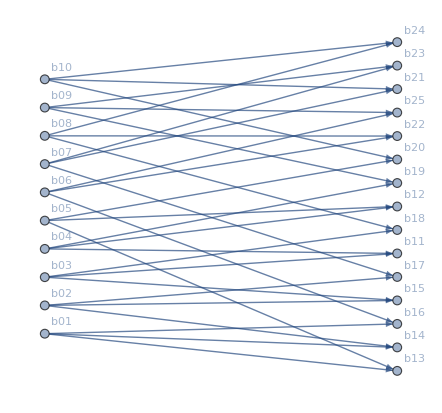

```mathematica
Graph[{b01->b13,b01->b14,b01->b16,b02->b14,b02->b15,b02->b17,b03->b11,b03->b15,b03->b18,b04->b11,b04->b12,b04->b19,b05->b12,b05->b13,b05->b20,b06->b16,b06->b22,b06->b25,b07->b17,b07->b21,b07->b23,b08->b18,b08->b22,b08->b24,b09->b19,b09->b23,b09->b25,b10->b20,b10->b21,b10->b24}, VertexLabels->"Name", GraphLayout->"BipartiteEmbedding"]
```

```mathematica
simplified=Table[Symbol["b"<>StringPadLeft[ToString[i],2,"0"]]->Symbol["q"<>ToString[Floor[Divide[i-1,5]]+1]],{i,50}]
```

{b01→q1,b02→q1,b03→q1,b04→q1,b05→q1,b06→q2,b07→q2,b08→q2,b09→q2,b10→q2,b11→q3,b12→q3,b13→q3,b14→q3,b15→q3,b16→q4,b17→q4,b18→q4,b19→q4,b20→q4,b21→q5,b22→q5,b23→q5,b24→q5,b25→q5,b26→q6,b27→q6,b28→q6,b29→q6,b30→q6,b31→q7,b32→q7,b33→q7,b34→q7,b35→q7,b36→q8,b37→q8,b38→q8,b39→q8,b40→q8,b41→q9,b42→q9,b43→q9,b44→q9,b45→q9,b46→q10,b47→q10,b48→q10,b49→q10,b50→q10}

```mathematica
ddd=ineqs/.simplified//Simplify
```

q2>0&&z>0&&q1>0&&q5>0&&q4>0&&q7>0&&q6>0&&q3>0&&q8>0&&q10>0&&q9>0&&q2<z&&q1<z&&q5<q2&&q4<q2&&q1+q7<2 q2&&q7<q1&&q6<q2&&2 q2<q5+z&&q1+q2<q4+z&&q4<q1&&q1+2 q2<q7+2 z&&2 q1+q2<q6+2 z&&q2+q6<2 q1&&q3<q1&&q4+q8<q1+q7&&q10+5 q4+q6<3 q2+q3+q5+2 q7&&3 q2+q3+q5<3 q1+q10+5 q4+q6+q7&&q10+5 q3+q7<3 q1+q4+q5+2 q6&&q4+q5+2 q6<q10+5 q3+4 q7&&q10+3 q2+q6+q7<3 q1+q3+q4+q5&&q10+5 q5+q6<3 q2+q3+q4+2 q7&&q10+3 q2+5 q3+q6<6 q1+q4+q5+2 q7&&q10+4 q6<q3+q4+q5+2 q7&&2 q1<q3+z&&q1+2 q5+q8<2 q2+q4+q7&&3 q1+q3+q5<q10+3 q2+5 q4+q6+q7&&3 q1+q10+q6+q7<3 q2+q3+q4+q5&&3 q1+q10+5 q5+q7<6 q2+q3+q4+2 q6&&q3+q4+2 q6<q10+5 q5+4 q7&&q8<q7&&q10+2 q4+q6<q3+q5+2 q7&&q3+q5<q10+2 q4+q6+q7&&2 q10+3 q2+4 q3<3 q1+2 q4+2 q5+q6+q7&&3 q1+2 q4+2 q5+q6<2 q10+3 q2+4 q3+5 q7&&3 q1+2 q10+4 q5<3 q2+2 q3+2 q4+q6+q7&&3 q2+2 q3+2 q4+q6<3 q1+2 q10+4 q5+5 q7&&q4+q7<q1+q8&&q8<q4&&q3+q5+2 (q6+q7)<q10+5 q4&&q10+5 q4+q7<3 q1+q3+q5+2 q6&&q3+q4+q5+2 q6<3 q1+q10+q7&&q10+4 q7<q3+q4+q5+2 q6&&6 q2+q3+q4+2 q6+2 q7<6 q1+q10+5 q5&&q3+q4+q5+2 q7<q10+3 q2+q6&&q1+2 q5+q7<2 q2+q4+q8&&q4+q8<2 q5&&6 q1+q4+q5+2 q6+2 q7<q10+6 q2+5 q3&&q1+4 q2+q8<q4+2 q5+q7+2 z&&q4+2 q5<2 q2+q8&&6 q1+q10+6 q2<q3+q4+q5+2 q6+2 q7+6 z&&q4+q9<q2+q6&&q3+q4+2 q7<q10+5 q5+4 q6&&q4+q5+2 q7<q10+5 q3+4 q6&&q2+2 q3+q9<2 q1+q4+q6&&3 q10+2 q3+14 q4+2 q5+7 q8<6 q1+6 q2+6 q6+6 q7+5 q9&&6 q2+2 q3+2 q5+2 q7+5 q9<6 q1+7 q10+10 q4+10 q6+7 q8&&3 q10+2 q3+14 q4+2 q5+7 q9<6 q1+6 q2+6 q6+6 q7+5 q8&&6 q2+2 q3+2 q5+2 q7+5 q8<6 q1+7 q10+10 q4+10 q6+7 q9&&3 q10+6 q2+26 q3+2 q5+6 q7+7 q9<18 q1+10 q4+18 q6+5 q8&&6 q1+14 q4+2 q5+2 q6+5 q8<7 q10+6 q2+22 q3+10 q7+7 q9&&7 q10+6 q2+10 q7<6 q1+2 q3+2 q4+2 q5+2 q6+5 q8+5 q9&&6 q3+6 q4+6 q5+5 q8+5 q9<6 q1+11 q10+6 q2+14 q6+14 q7&&3 q2+2 q3+2 q4+q7<3 q1+2 q10+4 q5+5 q6&&3 q1+2 q4+2 q5+q7<2 q10+3 q2+4 q3+5 q6&&q9<q4&&6 q1+6 q3+6 q5+2 q6+19 q8<q10+6 q2+18 q4+10 q7+5 q9&&18 q1+6 q4+6 q5+2 q7+19 q9<q10+18 q2+18 q3+10 q6+5 q8&&6 q2+22 q3+6 q6+5 q8<6 q1+3 q10+26 q4+2 q5+6 q7+19 q9&&6 q1+3 q10+2 q3+2 q5+6 q7+7 q9<6 q2+10 q4+6 q6+5 q8&&6 q1+2 q3+2 q5+2 q6+5 q8<7 q10+6 q2+10 q4+10 q7+7 q9&&6 q1+3 q10+2 q3+2 q5+6 q7+7 q8<6 q2+10 q4+6 q6+5 q9&&6 q1+2 q3+2 q5+2 q6+5 q9<7 q10+6 q2+10 q4+10 q7+7 q8&&q3<q10+q4+q5&&18 q2+6 q3+6 q4+2 q6+19 q8<18 q1+q10+18 q5+10 q7+5 q9&&6 q1+22 q5+6 q7+5 q9<3 q10+6 q2+2 q3+26 q4+6 q6+19 q8&&3 q10+6 q2+2 q3+2 q5+6 q6+7 q9<6 q1+10 q4+6 q7+5 q8&&6 q2+6 q3+6 q5+2 q7+19 q9<6 q1+q10+18 q4+10 q6+5 q8&&3 q10+6 q2+2 q3+2 q5+6 q6+7 q8<6 q1+10 q4+6 q7+5 q9&&q5<q10+q3+q4&&6 q2+6 q3+2 q6+13 q8<6 q1+q10+6 q5+10 q7+5 q9&&6 q1+q10+4 q4+4 q5+7 q9<6 q2+8 q3+2 q6+2 q7+5 q8&&6 q2+12 q3+5 q8<6 q1+5 q10+12 q4+2 q6+2 q7+7 q9&&q10+4 q3+4 q5+4 q7+7 q9<8 q4+8 q6+5 q8&&3 q10+2 q3+2 q5+q8<4 q4+5 q9&&2 q3+2 q5+5 q9<7 q10+4 q4+4 q6+4 q7+q8&&2 q3+q4<2 q1+q9&&q4+q9<2 q3&&6 q1+5 q10+14 q4+14 q5+14 q7+5 q9<18 q2+10 q3+10 q6+19 q8&&q10+6 q2+18 q3+6 q4+5 q8<18 q1+6 q5+2 q6+2 q7+7 q9&&6 q1+3 q10+14 q4+2 q5+6 q7+7 q9<6 q2+22 q3+6 q6+5 q8&&q10+6 q2+6 q4+10 q7+5 q9<6 q1+6 q3+6 q5+2 q6+7 q8&&q10+2 q4+q7<q3+q5+2 q6&&q4+q6<q2+q9&&4 q1+q2+q9<2 q3+q4+q6+2 z&&q2+2 q3+q6<2 q1+q4+q9&&6 q1+6 q4+6 q5+2 q6+7 q8+7 q9<q10+6 q2+18 q3+10 q7&&q4<q10+q3+q5&&6 q1+3 q10+2 q3+26 q5+6 q6+7 q8<18 q2+10 q4+18 q7+5 q9&&6 q2+2 q3+14 q4+2 q7+5 q9<6 q1+7 q10+22 q5+10 q6+7 q8&&6 q1+7 q10+10 q6<6 q2+2 q3+2 q4+2 q5+2 q7+5 q8+5 q9&&6 q1+6 q5+2 q6+7 q8+q9<q10+6 q2+6 q3+10 q7&&3 q10+2 q3+2 q5+q9<4 q4+5 q8&&6 q1+8 q4+2 q5+2 q6+5 q8<7 q10+6 q2+10 q3+10 q7+q9&&6 q1+q10+4 q4+4 q5+q8+q9<2 (3 q2+4 q3+q6+q7)&&4 q6<5 q10+8 q7+q8+q9&&5 q10+2 (7 q3+7 q5+q6+q7)<6 q1+6 q2+10 q4+7 q8+7 q9&&6 q2+6 q3+6 q4+2 q7+7 q8+7 q9<6 q1+q10+18 q5+10 q6&&6 q1+q10+6 q4+10 q6+5 q8<6 q2+6 q3+6 q5+2 q7+7 q9&&q9<q6&&6 q1+22 q4+6 q7+5 q8≤3 q10+6 q2+26 q3+2 q5+6 q6+19 q9&&4 q7<5 q10+8 q6+q8+q9&&6 q1+6 q5+2 q7+13 q9<q10+6 q2+6 q3+10 q6+5 q8&&4 q4+5 q8<3 q10+2 q3+2 q5+13 q9&&6 q1+12 q4+5 q8≤5 q10+6 q2+12 q3+2 q6+2 q7+7 q9&&6 q1+3 q10+8 q4+2 q5+6 q7+q9<6 q2+10 q3+6 q6+5 q8&&2 q3+2 q5+5 q8<7 q10+4 q4+4 q6+4 q7+q9&&q10+4 q3+4 q5+4 q6+7 q8<8 q4+8 q7+5 q9&&q10+6 q2+4 q3+4 q4+7 q8<6 q1+8 q5+2 q6+2 q7+5 q9&&6 q1+12 q5+5 q9<5 q10+6 q2+12 q4+2 q6+2 q7+7 q8&&2 q2+2 q4+2 q6+3 q8<2 q1+q10+2 q3+2 q5+2 q7+q9&&2 q1+6 q5+2 q7+q9<3 q10+2 q2+2 q3+6 q4+2 q6+3 q8&&2 q1+6 q5+2 q7+7 q9<q10+2 q2+2 q3+6 q4+2 q6+5 q8&&2 q2+2 q4+2 q6+5 q8≤2 q1+3 q10+2 q3+2 q5+2 q7+7 q9&&2 q6+4 q8<q10+4 q7+2 q9&&3 q1+4 q5+3 q7+2 q9<3 q10+3 q2+2 q3+2 q4+3 q6+4 q8&&6 q1+6 q5+2 q7+7 q9<q10+6 q2+6 q3+4 q6+5 q8&&3 q2+4 q3+3 q6+5 q8≤3 q1+3 q10+2 q4+2 q5+3 q7+7 q9&&3 q1+5 q5+3 q7+4 q9<3 q2+q3+4 q4+3 q6+5 q8&&2 q4+2 q6+5 q8≤4 q10+q3+q5+4 q7+4 q9&&2 q4+q8<q3+q5+2 q9&&3 q1+5 q5+2 q9<4 q10+3 q2+q3+4 q4+q6+q7+q8&&q10+18 q2+18 q3+10 q6+5 q8<18 q1+18 q4+6 q5+2 q7+7 q9&&6 q2+6 q6+5 (q8+q9)<6 q1+3 q10+2 (q3+q4+q5+3 q7)&&6 q1+q10+6 q4+18 q5+5 q9<18 q2+6 q3+2 q6+2 q7+7 q8&&3 q10+6 q2+2 q3+14 q4+6 q6+7 q8<6 q1+22 q5+6 q7+5 q9&&5 q10+6 q2+14 q3+14 q4+14 q6+5 q8<18 q1+10 q5+10 q7+19 q9&&6 q2+22 q4+6 q6+5 q9<6 q1+3 q10+2 q3+26 q5+6 q7+19 q8&&4 q4+5 q9<3 q10+2 q3+2 q5+13 q8&&3 q10+6 q2+2 q3+8 q4+6 q6+q8<6 q1+10 q5+6 q7+5 q9&&q10+6 q2+4 q3+4 q4+q8+q9<2 (3 q1+4 q5+q6+q7)&&6 q2+12 q4+5 q9<6 q1+5 q10+12 q5+2 q6+2 q7+7 q8&&18 q1+q10+18 q5+10 q7+5 q9<18 q2+6 q3+18 q4+2 q6+7 q8&&6 q2+6 q3+2 q7+q8+7 q9<6 q1+q10+6 q5+10 q6&&6 q2+2 q3+8 q4+2 q7+5 q9<6 q1+7 q10+10 q5+10 q6+q8&&2 q2+6 q3+2 q6+7 q8<2 q1+q10+6 q4+2 q5+2 q7+5 q9&&2 q1+2 q4+2 q7+5 q9<3 q10+2 q2+2 q3+2 q5+2 q6+7 q8&&2 q1+2 q4+2 q7+3 q9<q10+2 q2+2 q3+2 q5+2 q6+q8&&2 q2+6 q3+2 q6+q8<2 q1+3 q10+6 q4+2 q5+2 q7+3 q9&&6 q2+6 q3+2 q6+7 q8<6 q1+q10+6 q5+4 q7+5 q9&&3 q1+4 q5+3 q7+5 q9<3 q10+3 q2+2 q3+2 q4+3 q6+7 q8&&2 q4+q9<q3+q5+2 q8&&3 q2+5 q3+2 q8<3 q1+4 q10+4 q4+q5+q6+q7+q9&&2 q7+4 q9<q10+4 q6+2 q8&&3 q2+4 q3+3 q6+2 q8<3 q1+3 q10+2 q4+2 q5+3 q7+4 q9&&3 q2+5 q3+3 q6+4 q8<3 q1+4 q4+q5+3 q7+5 q9&&2 q4+2 q7+5 q9<4 q10+q3+q5+4 q6+4 q8&&6 q1+6 q7+5 (q8+q9)<3 q10+2 (3 q2+q3+q4+q5+3 q6)&&2 (q4+q6+q8)<4 q10+q3+q5+4 q7+q9&&2 (q4+q7+q9)<4 q10+q3+q5+4 q6+q8&&2 q2+2 q3+2 q6+3 q8<2 q1+q10+2 q5+2 q7+3 q9&&2 q1+2 q5+2 q7+3 q9<q10+2 q2+2 q3+2 q6+3 q8&&6 q1+3 q10+4 q4+4 q5+6 q7+5 q9<6 q2+8 q3+6 q6+7 q8&&3 q10+4 (q3+q5)<8 q4+q8+q9&&6 q1+q10+6 q5+5 q9<6 q2+6 q3+2 q6+2 q7+q8&&q10+6 q2+6 q3+5 q8<6 q1+6 q5+2 q6+2 q7+q9&&3 q10+6 q2+4 q3+4 q4+6 q6+5 q8<6 q1+8 q5+6 q7+7 q9&&18 q2+10 q3+10 q6+7 q8<18 q1+5 q10+2 q4+14 q5+2 q7+5 q9&&2 (3 q3+3 q4+3 q5+q6+q7)<6 q1+q10+6 q2+5 q8+5 q9&&18 q1+10 q5+10 q7+7 q9<5 q10+18 q2+14 q3+2 q4+2 q6+5 q8&&5 (6 q1+q10+6 q2+q8+q9)<2 (5 q3+5 q4+5 q5+5 q6+5 q7+12 z)&&q9<q10+3 q8&&2 q2+4 q3+2 q6+q8<2 q1+q10+4 q4+2 q7+3 q9&&2 q1+4 q5+2 q7+q9<q10+2 q2+4 q4+2 q6+3 q8&&q8≤q10+3 q9&&6 q2+6 q6+11 q8≤6 q1+9 q10+2 q3+2 q4+2 q5+6 q7+13 q9&&2 q1+4 q4+2 q7+5 q9<q10+2 q2+4 q3+2 q6+7 q8&&4 q4<3 q10+2 q3+2 q5+q8+q9&&6 q1+6 q7+11 q9<9 q10+6 q2+2 q3+2 q4+2 q5+6 q6+13 q8&&6 q1+2 q4+5 q5+6 q7+10 q9<3 q10+6 q2+7 q3+6 q6+11 q8&&6 q1+8 q4+2 q5+6 q7+13 q9<3 q10+6 q2+10 q3+6 q6+17 q8&&2 q2+4 q4+2 q6+5 q8≤2 q1+q10+4 q5+2 q7+7 q9&&6 q2+5 q3+2 q4+6 q6+10 q8≤6 q1+3 q10+7 q5+6 q7+11 q9&&6 q2+2 q3+8 q4+6 q6+13 q8≤6 q1+3 q10+10 q5+6 q7+17 q9&&6 q1+4 q4+4 q5+6 q7+11 q9<3 q10+6 q2+8 q3+6 q6+13 q8&&6 q2+4 q3+4 q4+6 q6+11 q8≤6 q1+3 q10+8 q5+6 q7+13 q9

```mathematica
dde=Fold[And,ddd]//Simplify
```

q2>0&&z>0&&q1>0&&q5>0&&q4>0&&q7>0&&q6>0&&q3>0&&q8>0&&q10>0&&q9>0&&q2<z&&q1<z&&q5<q2&&q4<q2&&q1+q7<2 q2&&q7<q1&&q6<q2&&2 q2<q5+z&&q1+q2<q4+z&&q4<q1&&q1+2 q2<q7+2 z&&2 q1+q2<q6+2 z&&q2+q6<2 q1&&q3<q1&&q4+q8<q1+q7&&q10+5 q4+q6<3 q2+q3+q5+2 q7&&3 q2+q3+q5<3 q1+q10+5 q4+q6+q7&&q10+5 q3+q7<3 q1+q4+q5+2 q6&&q4+q5+2 q6<q10+5 q3+4 q7&&q10+3 q2+q6+q7<3 q1+q3+q4+q5&&q10+5 q5+q6<3 q2+q3+q4+2 q7&&q10+3 q2+5 q3+q6<6 q1+q4+q5+2 q7&&q10+4 q6<q3+q4+q5+2 q7&&2 q1<q3+z&&q1+2 q5+q8<2 q2+q4+q7&&3 q1+q3+q5<q10+3 q2+5 q4+q6+q7&&3 q1+q10+q6+q7<3 q2+q3+q4+q5&&3 q1+q10+5 q5+q7<6 q2+q3+q4+2 q6&&q3+q4+2 q6<q10+5 q5+4 q7&&q8<q7&&q10+2 q4+q6<q3+q5+2 q7&&q3+q5<q10+2 q4+q6+q7&&2 q10+3 q2+4 q3<3 q1+2 q4+2 q5+q6+q7&&3 q1+2 q4+2 q5+q6<2 q10+3 q2+4 q3+5 q7&&3 q1+2 q10+4 q5<3 q2+2 q3+2 q4+q6+q7&&3 q2+2 q3+2 q4+q6<3 q1+2 q10+4 q5+5 q7&&q4+q7<q1+q8&&q8<q4&&q3+q5+2 (q6+q7)<q10+5 q4&&q10+5 q4+q7<3 q1+q3+q5+2 q6&&q3+q4+q5+2 q6<3 q1+q10+q7&&q10+4 q7<q3+q4+q5+2 q6&&6 q2+q3+q4+2 q6+2 q7<6 q1+q10+5 q5&&q3+q4+q5+2 q7<q10+3 q2+q6&&q1+2 q5+q7<2 q2+q4+q8&&q4+q8<2 q5&&6 q1+q4+q5+2 q6+2 q7<q10+6 q2+5 q3&&q1+4 q2+q8<q4+2 q5+q7+2 z&&q4+2 q5<2 q2+q8&&6 q1+q10+6 q2<q3+q4+q5+2 q6+2 q7+6 z&&q4+q9<q2+q6&&q3+q4+2 q7<q10+5 q5+4 q6&&q4+q5+2 q7<q10+5 q3+4 q6&&q2+2 q3+q9<2 q1+q4+q6&&3 q10+2 q3+14 q4+2 q5+7 q8<6 q1+6 q2+6 q6+6 q7+5 q9&&6 q2+2 q3+2 q5+2 q7+5 q9<6 q1+7 q10+10 q4+10 q6+7 q8&&3 q10+2 q3+14 q4+2 q5+7 q9<6 q1+6 q2+6 q6+6 q7+5 q8&&6 q2+2 q3+2 q5+2 q7+5 q8<6 q1+7 q10+10 q4+10 q6+7 q9&&3 q10+6 q2+26 q3+2 q5+6 q7+7 q9<18 q1+10 q4+18 q6+5 q8&&6 q1+14 q4+2 q5+2 q6+5 q8<7 q10+6 q2+22 q3+10 q7+7 q9&&7 q10+6 q2+10 q7<6 q1+2 q3+2 q4+2 q5+2 q6+5 q8+5 q9&&6 q3+6 q4+6 q5+5 q8+5 q9<6 q1+11 q10+6 q2+14 q6+14 q7&&3 q2+2 q3+2 q4+q7<3 q1+2 q10+4 q5+5 q6&&3 q1+2 q4+2 q5+q7<2 q10+3 q2+4 q3+5 q6&&q9<q4&&6 q1+6 q3+6 q5+2 q6+19 q8<q10+6 q2+18 q4+10 q7+5 q9&&18 q1+6 q4+6 q5+2 q7+19 q9<q10+18 q2+18 q3+10 q6+5 q8&&6 q2+22 q3+6 q6+5 q8<6 q1+3 q10+26 q4+2 q5+6 q7+19 q9&&6 q1+3 q10+2 q3+2 q5+6 q7+7 q9<6 q2+10 q4+6 q6+5 q8&&6 q1+2 q3+2 q5+2 q6+5 q8<7 q10+6 q2+10 q4+10 q7+7 q9&&6 q1+3 q10+2 q3+2 q5+6 q7+7 q8<6 q2+10 q4+6 q6+5 q9&&6 q1+2 q3+2 q5+2 q6+5 q9<7 q10+6 q2+10 q4+10 q7+7 q8&&q3<q10+q4+q5&&18 q2+6 q3+6 q4+2 q6+19 q8<18 q1+q10+18 q5+10 q7+5 q9&&6 q1+22 q5+6 q7+5 q9<3 q10+6 q2+2 q3+26 q4+6 q6+19 q8&&3 q10+6 q2+2 q3+2 q5+6 q6+7 q9<6 q1+10 q4+6 q7+5 q8&&6 q2+6 q3+6 q5+2 q7+19 q9<6 q1+q10+18 q4+10 q6+5 q8&&3 q10+6 q2+2 q3+2 q5+6 q6+7 q8<6 q1+10 q4+6 q7+5 q9&&q5<q10+q3+q4&&6 q2+6 q3+2 q6+13 q8<6 q1+q10+6 q5+10 q7+5 q9&&6 q1+q10+4 q4+4 q5+7 q9<6 q2+8 q3+2 q6+2 q7+5 q8&&6 q2+12 q3+5 q8<6 q1+5 q10+12 q4+2 q6+2 q7+7 q9&&q10+4 q3+4 q5+4 q7+7 q9<8 q4+8 q6+5 q8&&3 q10+2 q3+2 q5+q8<4 q4+5 q9&&2 q3+2 q5+5 q9<7 q10+4 q4+4 q6+4 q7+q8&&2 q3+q4<2 q1+q9&&q4+q9<2 q3&&6 q1+5 q10+14 q4+14 q5+14 q7+5 q9<18 q2+10 q3+10 q6+19 q8&&q10+6 q2+18 q3+6 q4+5 q8<18 q1+6 q5+2 q6+2 q7+7 q9&&6 q1+3 q10+14 q4+2 q5+6 q7+7 q9<6 q2+22 q3+6 q6+5 q8&&q10+6 q2+6 q4+10 q7+5 q9<6 q1+6 q3+6 q5+2 q6+7 q8&&q10+2 q4+q7<q3+q5+2 q6&&q4+q6<q2+q9&&4 q1+q2+q9<2 q3+q4+q6+2 z&&q2+2 q3+q6<2 q1+q4+q9&&6 q1+6 q4+6 q5+2 q6+7 q8+7 q9<q10+6 q2+18 q3+10 q7&&q4<q10+q3+q5&&6 q1+3 q10+2 q3+26 q5+6 q6+7 q8<18 q2+10 q4+18 q7+5 q9&&6 q2+2 q3+14 q4+2 q7+5 q9<6 q1+7 q10+22 q5+10 q6+7 q8&&6 q1+7 q10+10 q6<6 q2+2 q3+2 q4+2 q5+2 q7+5 q8+5 q9&&6 q1+6 q5+2 q6+7 q8+q9<q10+6 q2+6 q3+10 q7&&3 q10+2 q3+2 q5+q9<4 q4+5 q8&&6 q1+8 q4+2 q5+2 q6+5 q8<7 q10+6 q2+10 q3+10 q7+q9&&6 q1+q10+4 q4+4 q5+q8+q9<2 (3 q2+4 q3+q6+q7)&&4 q6<5 q10+8 q7+q8+q9&&5 q10+2 (7 q3+7 q5+q6+q7)<6 q1+6 q2+10 q4+7 q8+7 q9&&6 q2+6 q3+6 q4+2 q7+7 q8+7 q9<6 q1+q10+18 q5+10 q6&&6 q1+q10+6 q4+10 q6+5 q8<6 q2+6 q3+6 q5+2 q7+7 q9&&q9<q6&&6 q1+22 q4+6 q7+5 q8≤3 q10+6 q2+26 q3+2 q5+6 q6+19 q9&&4 q7<5 q10+8 q6+q8+q9&&6 q1+6 q5+2 q7+13 q9<q10+6 q2+6 q3+10 q6+5 q8&&4 q4+5 q8<3 q10+2 q3+2 q5+13 q9&&6 q1+12 q4+5 q8≤5 q10+6 q2+12 q3+2 q6+2 q7+7 q9&&6 q1+3 q10+8 q4+2 q5+6 q7+q9<6 q2+10 q3+6 q6+5 q8&&2 q3+2 q5+5 q8<7 q10+4 q4+4 q6+4 q7+q9&&q10+4 q3+4 q5+4 q6+7 q8<8 q4+8 q7+5 q9&&q10+6 q2+4 q3+4 q4+7 q8<6 q1+8 q5+2 q6+2 q7+5 q9&&6 q1+12 q5+5 q9<5 q10+6 q2+12 q4+2 q6+2 q7+7 q8&&2 q2+2 q4+2 q6+3 q8<2 q1+q10+2 q3+2 q5+2 q7+q9&&2 q1+6 q5+2 q7+q9<3 q10+2 q2+2 q3+6 q4+2 q6+3 q8&&2 q1+6 q5+2 q7+7 q9<q10+2 q2+2 q3+6 q4+2 q6+5 q8&&2 q2+2 q4+2 q6+5 q8≤2 q1+3 q10+2 q3+2 q5+2 q7+7 q9&&2 q6+4 q8<q10+4 q7+2 q9&&3 q1+4 q5+3 q7+2 q9<3 q10+3 q2+2 q3+2 q4+3 q6+4 q8&&6 q1+6 q5+2 q7+7 q9<q10+6 q2+6 q3+4 q6+5 q8&&3 q2+4 q3+3 q6+5 q8≤3 q1+3 q10+2 q4+2 q5+3 q7+7 q9&&3 q1+5 q5+3 q7+4 q9<3 q2+q3+4 q4+3 q6+5 q8&&2 q4+2 q6+5 q8≤4 q10+q3+q5+4 q7+4 q9&&2 q4+q8<q3+q5+2 q9&&3 q1+5 q5+2 q9<4 q10+3 q2+q3+4 q4+q6+q7+q8&&q10+18 q2+18 q3+10 q6+5 q8<18 q1+18 q4+6 q5+2 q7+7 q9&&6 q2+6 q6+5 (q8+q9)<6 q1+3 q10+2 (q3+q4+q5+3 q7)&&6 q1+q10+6 q4+18 q5+5 q9<18 q2+6 q3+2 q6+2 q7+7 q8&&3 q10+6 q2+2 q3+14 q4+6 q6+7 q8<6 q1+22 q5+6 q7+5 q9&&5 q10+6 q2+14 q3+14 q4+14 q6+5 q8<18 q1+10 q5+10 q7+19 q9&&6 q2+22 q4+6 q6+5 q9<6 q1+3 q10+2 q3+26 q5+6 q7+19 q8&&4 q4+5 q9<3 q10+2 q3+2 q5+13 q8&&3 q10+6 q2+2 q3+8 q4+6 q6+q8<6 q1+10 q5+6 q7+5 q9&&q10+6 q2+4 q3+4 q4+q8+q9<2 (3 q1+4 q5+q6+q7)&&6 q2+12 q4+5 q9<6 q1+5 q10+12 q5+2 q6+2 q7+7 q8&&18 q1+q10+18 q5+10 q7+5 q9<18 q2+6 q3+18 q4+2 q6+7 q8&&6 q2+6 q3+2 q7+q8+7 q9<6 q1+q10+6 q5+10 q6&&6 q2+2 q3+8 q4+2 q7+5 q9<6 q1+7 q10+10 q5+10 q6+q8&&2 q2+6 q3+2 q6+7 q8<2 q1+q10+6 q4+2 q5+2 q7+5 q9&&2 q1+2 q4+2 q7+5 q9<3 q10+2 q2+2 q3+2 q5+2 q6+7 q8&&2 q1+2 q4+2 q7+3 q9<q10+2 q2+2 q3+2 q5+2 q6+q8&&2 q2+6 q3+2 q6+q8<2 q1+3 q10+6 q4+2 q5+2 q7+3 q9&&6 q2+6 q3+2 q6+7 q8<6 q1+q10+6 q5+4 q7+5 q9&&3 q1+4 q5+3 q7+5 q9<3 q10+3 q2+2 q3+2 q4+3 q6+7 q8&&2 q4+q9<q3+q5+2 q8&&3 q2+5 q3+2 q8<3 q1+4 q10+4 q4+q5+q6+q7+q9&&2 q7+4 q9<q10+4 q6+2 q8&&3 q2+4 q3+3 q6+2 q8<3 q1+3 q10+2 q4+2 q5+3 q7+4 q9&&3 q2+5 q3+3 q6+4 q8<3 q1+4 q4+q5+3 q7+5 q9&&2 q4+2 q7+5 q9<4 q10+q3+q5+4 q6+4 q8&&6 q1+6 q7+5 (q8+q9)<3 q10+2 (3 q2+q3+q4+q5+3 q6)&&2 (q4+q6+q8)<4 q10+q3+q5+4 q7+q9&&2 (q4+q7+q9)<4 q10+q3+q5+4 q6+q8&&2 q2+2 q3+2 q6+3 q8<2 q1+q10+2 q5+2 q7+3 q9&&2 q1+2 q5+2 q7+3 q9<q10+2 q2+2 q3+2 q6+3 q8&&6 q1+3 q10+4 q4+4 q5+6 q7+5 q9<6 q2+8 q3+6 q6+7 q8&&3 q10+4 (q3+q5)<8 q4+q8+q9&&6 q1+q10+6 q5+5 q9<6 q2+6 q3+2 q6+2 q7+q8&&q10+6 q2+6 q3+5 q8<6 q1+6 q5+2 q6+2 q7+q9&&3 q10+6 q2+4 q3+4 q4+6 q6+5 q8<6 q1+8 q5+6 q7+7 q9&&18 q2+10 q3+10 q6+7 q8<18 q1+5 q10+2 q4+14 q5+2 q7+5 q9&&2 (3 q3+3 q4+3 q5+q6+q7)<6 q1+q10+6 q2+5 q8+5 q9&&18 q1+10 q5+10 q7+7 q9<5 q10+18 q2+14 q3+2 q4+2 q6+5 q8&&5 (6 q1+q10+6 q2+q8+q9)<2 (5 q3+5 q4+5 q5+5 q6+5 q7+12 z)&&q9<q10+3 q8&&2 q2+4 q3+2 q6+q8<2 q1+q10+4 q4+2 q7+3 q9&&2 q1+4 q5+2 q7+q9<q10+2 q2+4 q4+2 q6+3 q8&&q8≤q10+3 q9&&6 q2+6 q6+11 q8≤6 q1+9 q10+2 q3+2 q4+2 q5+6 q7+13 q9&&2 q1+4 q4+2 q7+5 q9<q10+2 q2+4 q3+2 q6+7 q8&&4 q4<3 q10+2 q3+2 q5+q8+q9&&6 q1+6 q7+11 q9<9 q10+6 q2+2 q3+2 q4+2 q5+6 q6+13 q8&&6 q1+2 q4+5 q5+6 q7+10 q9<3 q10+6 q2+7 q3+6 q6+11 q8&&6 q1+8 q4+2 q5+6 q7+13 q9<3 q10+6 q2+10 q3+6 q6+17 q8&&2 q2+4 q4+2 q6+5 q8≤2 q1+q10+4 q5+2 q7+7 q9&&6 q2+5 q3+2 q4+6 q6+10 q8≤6 q1+3 q10+7 q5+6 q7+11 q9&&6 q2+2 q3+8 q4+6 q6+13 q8≤6 q1+3 q10+10 q5+6 q7+17 q9&&6 q1+4 q4+4 q5+6 q7+11 q9<3 q10+6 q2+8 q3+6 q6+13 q8&&6 q2+4 q3+4 q4+6 q6+11 q8≤6 q1+3 q10+8 q5+6 q7+13 q9

```mathematica
Map[Reduce[#,z,Integers]&,dde]
```

$Aborted

```mathematica
Fold[And,ddd]//Simplify//ExpressionToTable2
```

q1>0
q2>0
q3>0
q4>0
q5>0
q6>0
q7>0
q8>0
q9>0
q10>0
z>0
q3<q1
q4<q1
q7<q1
q4<q2
q5<q2
q6<q2
q8<q4
q9<q4
q9<q6
q8<q7
q1<z
q2<z
q2+q6<2 q1
q1+q7<2 q2
q4+q9<2 q3
q4+q8<2 q5
q8≤q10+3 q9
q9<q10+3 q8
2 q1<q3+z
2 q2<q5+z
2 q3+q4<2 q1+q9
q4+q8<q1+q7
q4+q7<q1+q8
q4+2 q5<2 q2+q8
q4+q9<q2+q6
q4+q6<q2+q9
q5<q10+q3+q4
q4<q10+q3+q5
q3<q10+q4+q5
q1+q2<q4+z
2 q1+q2<q6+2 z
q1+2 q2<q7+2 z
2 q4+q9<q3+q5+2 q8
2 q4+q8<q3+q5+2 q9
2 q7+4 q9<q10+4 q6+2 q8
2 q6+4 q8<q10+4 q7+2 q9
4 q7<5 q10+8 q6+q8+q9
4 q6<5 q10+8 q7+q8+q9
q2+2 q3+q9<2 q1+q4+q6
q2+2 q3+q6<2 q1+q4+q9
q1+2 q5+q8<2 q2+q4+q7
q1+2 q5+q7<2 q2+q4+q8
q3+q5+2 (q6+q7)<q10+5 q4
q10+4 q7<q3+q4+q5+2 q6
q4+q5+2 q7<q10+5 q3+4 q6
q3+q4+2 q7<q10+5 q5+4 q6
q10+2 q4+q7<q3+q5+2 q6
q10+4 q6<q3+q4+q5+2 q7
q4+q5+2 q6<q10+5 q3+4 q7
q3+q4+2 q6<q10+5 q5+4 q7
q10+2 q4+q6<q3+q5+2 q7
q3+q5<q10+2 q4+q6+q7
4 q4+5 q9<3 q10+2 q3+2 q5+13 q8
3 q10+2 q3+2 q5+q9<4 q4+5 q8
4 q4+5 q8<3 q10+2 q3+2 q5+13 q9
3 q10+2 q3+2 q5+q8<4 q4+5 q9
3 q10+4 (q3+q5)<8 q4+q8+q9
4 q4<3 q10+2 q3+2 q5+q8+q9
q10+5 q4+q7<3 q1+q3+q5+2 q6
q10+5 q3+q7<3 q1+q4+q5+2 q6
q3+q4+q5+2 q6<3 q1+q10+q7
q3+q4+q5+2 q7<q10+3 q2+q6
q10+5 q5+q6<3 q2+q3+q4+2 q7
q10+5 q4+q6<3 q2+q3+q5+2 q7
4 q1+q2+q9<2 q3+q4+q6+2 z
q1+4 q2+q8<q4+2 q5+q7+2 z
6 q1+q4+q5+2 q6+2 q7<q10+6 q2+5 q3
6 q2+q3+q4+2 q6+2 q7<6 q1+q10+5 q5
q10+3 q2+q6+q7<3 q1+q3+q4+q5
3 q1+q10+q6+q7<3 q2+q3+q4+q5
3 q1+q10+5 q5+q7<6 q2+q3+q4+2 q6
3 q1+2 q4+2 q5+q7<2 q10+3 q2+4 q3+5 q6
3 q2+2 q3+2 q4+q7<3 q1+2 q10+4 q5+5 q6
3 q1+2 q4+2 q5+q6<2 q10+3 q2+4 q3+5 q7
3 q2+2 q3+2 q4+q6<3 q1+2 q10+4 q5+5 q7
q10+3 q2+5 q3+q6<6 q1+q4+q5+2 q7
3 q1+2 q10+4 q5<3 q2+2 q3+2 q4+q6+q7
3 q2+q3+q5<3 q1+q10+5 q4+q6+q7
3 q1+q3+q5<q10+3 q2+5 q4+q6+q7
2 q10+3 q2+4 q3<3 q1+2 q4+2 q5+q6+q7
2 q4+2 q6+5 q8≤4 q10+q3+q5+4 q7+4 q9
q10+4 q3+4 q5+4 q7+7 q9<8 q4+8 q6+5 q8
2 q4+2 q7+5 q9<4 q10+q3+q5+4 q6+4 q8
2 q3+2 q5+5 q9<7 q10+4 q4+4 q6+4 q7+q8
2 (q4+q7+q9)<4 q10+q3+q5+4 q6+q8
q10+4 q3+4 q5+4 q6+7 q8<8 q4+8 q7+5 q9
2 q3+2 q5+5 q8<7 q10+4 q4+4 q6+4 q7+q9
2 (q4+q6+q8)<4 q10+q3+q5+4 q7+q9
3 q1+5 q5+3 q7+4 q9<3 q2+q3+4 q4+3 q6+5 q8
3 q2+5 q3+3 q6+4 q8<3 q1+4 q4+q5+3 q7+5 q9
6 q1+12 q4+5 q8≤5 q10+6 q2+12 q3+2 q6+2 q7+7 q9
2 q1+4 q4+2 q7+5 q9<q10+2 q2+4 q3+2 q6+7 q8
6 q2+12 q3+5 q8<6 q1+5 q10+12 q4+2 q6+2 q7+7 q9
2 q2+4 q3+2 q6+q8<2 q1+q10+4 q4+2 q7+3 q9
6 q1+6 q5+2 q7+13 q9<q10+6 q2+6 q3+10 q6+5 q8
6 q2+6 q3+2 q7+q8+7 q9<6 q1+q10+6 q5+10 q6
6 q1+6 q5+2 q7+7 q9<q10+6 q2+6 q3+4 q6+5 q8
6 q1+q10+6 q5+5 q9<6 q2+6 q3+2 q6+2 q7+q8
2 q1+2 q5+2 q7+3 q9<q10+2 q2+2 q3+2 q6+3 q8
6 q1+6 q5+2 q6+7 q8+q9<q10+6 q2+6 q3+10 q7
6 q2+6 q3+2 q6+13 q8<6 q1+q10+6 q5+10 q7+5 q9
6 q2+6 q3+2 q6+7 q8<6 q1+q10+6 q5+4 q7+5 q9
q10+6 q2+6 q3+5 q8<6 q1+6 q5+2 q6+2 q7+q9
2 q2+2 q3+2 q6+3 q8<2 q1+q10+2 q5+2 q7+3 q9
2 q2+4 q4+2 q6+5 q8≤2 q1+q10+4 q5+2 q7+7 q9
6 q1+12 q5+5 q9<5 q10+6 q2+12 q4+2 q6+2 q7+7 q8
6 q2+12 q4+5 q9<6 q1+5 q10+12 q5+2 q6+2 q7+7 q8
2 q1+4 q5+2 q7+q9<q10+2 q2+4 q4+2 q6+3 q8
6 q1+q10+6 q2<q3+q4+q5+2 q6+2 q7+6 z
6 q2+2 q3+8 q4+6 q6+13 q8≤6 q1+3 q10+10 q5+6 q7+17 q9
6 q2+4 q3+4 q4+6 q6+11 q8≤6 q1+3 q10+8 q5+6 q7+13 q9
6 q2+6 q6+11 q8≤6 q1+9 q10+2 q3+2 q4+2 q5+6 q7+13 q9
6 q2+5 q3+2 q4+6 q6+10 q8≤6 q1+3 q10+7 q5+6 q7+11 q9
6 q1+22 q4+6 q7+5 q8≤3 q10+6 q2+26 q3+2 q5+6 q6+19 q9
3 q2+4 q3+3 q6+5 q8≤3 q1+3 q10+2 q4+2 q5+3 q7+7 q9
2 q2+2 q4+2 q6+5 q8≤2 q1+3 q10+2 q3+2 q5+2 q7+7 q9
6 q1+6 q7+5 (q8+q9)<3 q10+2 (3 q2+q3+q4+q5+3 q6)
6 q2+6 q6+5 (q8+q9)<6 q1+3 q10+2 (q3+q4+q5+3 q7)
18 q1+6 q4+6 q5+2 q7+19 q9<q10+18 q2+18 q3+10 q6+5 q8
6 q2+6 q3+6 q5+2 q7+19 q9<6 q1+q10+18 q4+10 q6+5 q8
6 q1+8 q4+2 q5+6 q7+13 q9<3 q10+6 q2+10 q3+6 q6+17 q8
6 q1+4 q4+4 q5+6 q7+11 q9<3 q10+6 q2+8 q3+6 q6+13 q8
6 q1+6 q7+11 q9<9 q10+6 q2+2 q3+2 q4+2 q5+6 q6+13 q8
6 q1+2 q4+5 q5+6 q7+10 q9<3 q10+6 q2+7 q3+6 q6+11 q8
6 q2+6 q3+6 q4+2 q7+7 q8+7 q9<6 q1+q10+18 q5+10 q6
6 q1+6 q4+6 q5+2 q6+7 q8+7 q9<q10+6 q2+18 q3+10 q7
18 q1+10 q5+10 q7+7 q9<5 q10+18 q2+14 q3+2 q4+2 q6+5 q8
6 q1+3 q10+14 q4+2 q5+6 q7+7 q9<6 q2+22 q3+6 q6+5 q8
3 q10+6 q2+26 q3+2 q5+6 q7+7 q9<18 q1+10 q4+18 q6+5 q8
6 q1+3 q10+2 q3+2 q5+6 q7+7 q9<6 q2+10 q4+6 q6+5 q8
2 q1+6 q5+2 q7+7 q9<q10+2 q2+2 q3+6 q4+2 q6+5 q8
3 q10+6 q2+2 q3+2 q5+6 q6+7 q9<6 q1+10 q4+6 q7+5 q8
6 q1+q10+4 q4+4 q5+7 q9<6 q2+8 q3+2 q6+2 q7+5 q8
3 q10+2 q3+14 q4+2 q5+7 q9<6 q1+6 q2+6 q6+6 q7+5 q8
6 q3+6 q4+6 q5+5 q8+5 q9<6 q1+11 q10+6 q2+14 q6+14 q7
6 q1+5 q10+14 q4+14 q5+14 q7+5 q9<18 q2+10 q3+10 q6+19 q8
18 q1+q10+18 q5+10 q7+5 q9<18 q2+6 q3+18 q4+2 q6+7 q8
q10+6 q2+6 q4+10 q7+5 q9<6 q1+6 q3+6 q5+2 q6+7 q8
6 q1+22 q5+6 q7+5 q9<3 q10+6 q2+2 q3+26 q4+6 q6+19 q8
6 q1+3 q10+4 q4+4 q5+6 q7+5 q9<6 q2+8 q3+6 q6+7 q8
3 q1+4 q5+3 q7+5 q9<3 q10+3 q2+2 q3+2 q4+3 q6+7 q8
6 q2+2 q3+2 q5+2 q7+5 q9<6 q1+7 q10+10 q4+10 q6+7 q8
6 q2+2 q3+14 q4+2 q7+5 q9<6 q1+7 q10+22 q5+10 q6+7 q8
6 q2+2 q3+8 q4+2 q7+5 q9<6 q1+7 q10+10 q5+10 q6+q8
2 q1+2 q4+2 q7+5 q9<3 q10+2 q2+2 q3+2 q5+2 q6+7 q8
6 q2+22 q4+6 q6+5 q9<6 q1+3 q10+2 q3+26 q5+6 q7+19 q8
6 q1+2 q3+2 q5+2 q6+5 q9<7 q10+6 q2+10 q4+10 q7+7 q8
6 q1+q10+6 q4+18 q5+5 q9<18 q2+6 q3+2 q6+2 q7+7 q8
2 q1+2 q4+2 q7+3 q9<q10+2 q2+2 q3+2 q5+2 q6+q8
3 q1+4 q5+3 q7+2 q9<3 q10+3 q2+2 q3+2 q4+3 q6+4 q8
3 q1+5 q5+2 q9<4 q10+3 q2+q3+4 q4+q6+q7+q8
6 q1+q10+4 q4+4 q5+q8+q9<2 (3 q2+4 q3+q6+q7)
q10+6 q2+4 q3+4 q4+q8+q9<2 (3 q1+4 q5+q6+q7)
6 q1+3 q10+8 q4+2 q5+6 q7+q9<6 q2+10 q3+6 q6+5 q8
2 q1+6 q5+2 q7+q9<3 q10+2 q2+2 q3+6 q4+2 q6+3 q8
6 q1+6 q3+6 q5+2 q6+19 q8<q10+6 q2+18 q4+10 q7+5 q9
18 q2+6 q3+6 q4+2 q6+19 q8<18 q1+q10+18 q5+10 q7+5 q9
6 q1+3 q10+2 q3+2 q5+6 q7+7 q8<6 q2+10 q4+6 q6+5 q9
18 q2+10 q3+10 q6+7 q8<18 q1+5 q10+2 q4+14 q5+2 q7+5 q9
6 q1+3 q10+2 q3+26 q5+6 q6+7 q8<18 q2+10 q4+18 q7+5 q9
3 q10+6 q2+2 q3+2 q5+6 q6+7 q8<6 q1+10 q4+6 q7+5 q9
3 q10+6 q2+2 q3+14 q4+6 q6+7 q8<6 q1+22 q5+6 q7+5 q9
2 q2+6 q3+2 q6+7 q8<2 q1+q10+6 q4+2 q5+2 q7+5 q9
3 q10+2 q3+14 q4+2 q5+7 q8<6 q1+6 q2+6 q6+6 q7+5 q9
q10+6 q2+4 q3+4 q4+7 q8<6 q1+8 q5+2 q6+2 q7+5 q9
6 q2+2 q3+2 q5+2 q7+5 q8<6 q1+7 q10+10 q4+10 q6+7 q9
5 q10+6 q2+14 q3+14 q4+14 q6+5 q8<18 q1+10 q5+10 q7+19 q9
6 q1+q10+6 q4+10 q6+5 q8<6 q2+6 q3+6 q5+2 q7+7 q9
q10+18 q2+18 q3+10 q6+5 q8<18 q1+18 q4+6 q5+2 q7+7 q9
3 q10+6 q2+4 q3+4 q4+6 q6+5 q8<6 q1+8 q5+6 q7+7 q9
6 q2+22 q3+6 q6+5 q8<6 q1+3 q10+26 q4+2 q5+6 q7+19 q9
6 q1+14 q4+2 q5+2 q6+5 q8<7 q10+6 q2+22 q3+10 q7+7 q9
6 q1+8 q4+2 q5+2 q6+5 q8<7 q10+6 q2+10 q3+10 q7+q9
6 q1+2 q3+2 q5+2 q6+5 q8<7 q10+6 q2+10 q4+10 q7+7 q9
q10+6 q2+18 q3+6 q4+5 q8<18 q1+6 q5+2 q6+2 q7+7 q9
2 q2+2 q4+2 q6+3 q8<2 q1+q10+2 q3+2 q5+2 q7+q9
3 q2+4 q3+3 q6+2 q8<3 q1+3 q10+2 q4+2 q5+3 q7+4 q9
3 q2+5 q3+2 q8<3 q1+4 q10+4 q4+q5+q6+q7+q9
3 q10+6 q2+2 q3+8 q4+6 q6+q8<6 q1+10 q5+6 q7+5 q9
2 q2+6 q3+2 q6+q8<2 q1+3 q10+6 q4+2 q5+2 q7+3 q9
5 q10+2 (7 q3+7 q5+q6+q7)<6 q1+6 q2+10 q4+7 q8+7 q9
7 q10+6 q2+10 q7<6 q1+2 q3+2 q4+2 q5+2 q6+5 q8+5 q9
2 (3 q3+3 q4+3 q5+q6+q7)<6 q1+q10+6 q2+5 q8+5 q9
6 q1+7 q10+10 q6<6 q2+2 q3+2 q4+2 q5+2 q7+5 q8+5 q9
5 (6 q1+q10+6 q2+q8+q9)<2 (5 q3+5 q4+5 q5+5 q6+5 q7+12 z)

```mathematica
Reduce[Fold[And,ddd]//Simplify,q1]
```

$Aborted